# Mechanisms package and sub-packages

version 1.72
Christian Santangelo, Physics Department, Syracuse University
Copyright 2020

#### Package organization

mechanisms: The mechanisms main package contains functions for manipulating and using mechanisms.

geometry : Mechanism geometry subpackage.

rigidity: This subpackage contains functions for basic rigidity of mechanisms and some functions for linkages

origami: this sub package contains functions for handling origami specifically.

These packages also use the Mathematica Developer package to take advantage of packed arrays when possible. A C compiler is recommended but not necessary.

#### To do list and known bug list

Is there a better way to do minimization with compiled functions and specified constraints? The algorithms are slow and that means fixed joints are poorly handled with compiled functions. Unrestrained minimization is still faster with compiled functions.

The function overlappingVertices[] may sometimes fail if two vertices have exactly the same distance apart and those distances are within tolerance.

## mechanisms: internal code for handling structures

```mathematica
BeginPackage["mechanisms`",{"Developer`"}];
$mechanismsVersion=1.72;
$mechanismsVersionText="mechanisms version 1.72";
```

## Usage

```mathematica
$mechanismsVersion::usage = "$mechanismsVersion returns the version number of the package.";
$mechanismsVersionText::usage = "$mechanismsVersionText returns the version number of the package as a string.";
```

```mathematica
rigidBar::usage="rigidBar[ {v1, v2} ] is a rigid bar. Use defaultData[ rigidBar ] to see its associated data.";
spring::usage="spring[ {v1, v2} ] is a spring allowing you to set an arbitrary force. Use defaultData[ spring ] to see its associated data.";
face::usage="face[ {v1,v2,...} ] is a face. Use defaultData[ face ] to see its associated data.";
fold::usage="fold[ {v1,v2} ] is a fold with torsional spring controlling its angle. Use defaultData[ fold ] to see its associated data.";
joint::usage="joint[v1] is a joint. Use defaultData[ joint ] to see its associated data.";
angleJoint::usage="angleJoint[v1] is a torsional joint. Use defaultData[ angleJoint ] to see its associated data.";

defaultData::usage="defaultData[ component ] returns the default data associated with a component.";
```

```mathematica
mechanism::usage = "Keyword used to report some errors.";

framework::usage = "framework[ { {x1, y1}, ...}, {cell1[ {i1, i2, ..} ], ... } ] returns a linkage in 2D with vertices at {{x1, y1}, ..} and made from the specified cells.
framework[ { {x1, y1, z1}, ...}, {cell1[ {i1, i2, ..} ], ... } ] returns a linkage in 3D with vertices at {{x1, y1}, ..} and made from the specified cells.\n
Properties:\n
Cell properties can be specified by Property[ cell1[ {i1, ...} ], {property1 -> value1, ... } ].
Properties that can be specified include MeshCellStyle, MeshCellLabel, MeshCellShapeFunction. Options[cell] will list additional properties that can be specified.\n
Options:\n
framework[] takes the same options as MeshRegion[] as well as an option \"overlapPrecision\" which determines how close vertices need to be in order to be mapped onto each other.";

origami::usage=
"origami[ { {x1, y1}, ...}, {cell1[ {i1, i2, ..} ], ... } ] returns an origami in 3D (displayed in 2D) with vertices at {{x1, y1}, ..} and made from the specified cells.
origami[ { {x1, y1, z1}, ...}, {cell1[ {i1, i2, ..} ], ... } ] returns an origami in 3D with vertices at {{x1, y1}, ..} and made from the specified cells.

Properties:

Cell properties can be specified by Property[ cell1[ {i1, ...} ], {property1 -> value1, ... } ].
Properties that can be specified include MeshCellStyle, MeshCellLabel, MeshCellShapeFunction. Options[cell] will list additional properties that can be specified.

Options:

origami[] takes the same options as MeshRegion[] as well as an option \"overlapPrecision\" which determines how close vertices need to be in order to be mapped onto each other.";

mechanismQ::usage="mechanismQ[ m ] returns True if m is a mechanism.";
```

```mathematica
vertexPosition::usage="vertexPosition[v, c] represents the position of vertex v along a particular component d, which is one of \"x\", \"y\", or \"z\" or All[d] where d is the dimension.";
SetAttributes[vertexPosition,{NHoldAll,Constant}]

vertexDisplacement::usage="vertexDisplacement[v, c] represents the displacement of vertex v along a particular component d, which is one of \"x\", \"y\", or \"z\" or All[d] where d is the dimension.";
SetAttributes[vertexDisplacement,{NHoldAll,Constant}]
```

```mathematica
(*cell modifiers*)
selectCells::usage=
"selectCells[ m, pattern ] selects a sub-mechanism with cell specification matching pattern.
selectCells[m, pattern, data, f] selects a sub-mechanism with cells matching pattern and f evaluating True when applied to the data. Use dataForm[] to find data that is available for a given component.";

deleteCells::usage="deleteCells[ m, pattern ] deletes a sub-mechanism with cell specification matching pattern.";

addCells::usage="addCells[ m, {cell1, cell2, ... } ] adds cells to a mechanism.";

highlightCells::usage="highlightCells[m, pattern, display properties] changes the display properties of cells that match a pattern.";

changeCellData::usage="changeCellData[m, pattern, {data1 -> newData,...}] changes the specified data on any cells that match a pattern.";

splitEdge::usage="splitEdge[ m, edge, label -> position ] adds a vertex to an edge and places the vertex at position with a label.";

(*vertex modifiers*)
placeVertices::usage="placeVertices[m, {v1 -> new position 1, ...} ] moves vertices to new positions.
placeVertices[m, { pos1, pos2, ... } ] replaces all vertex positions by a list of new positions.";

displaceVertices::usage="displaceVertices[m, {v1 -> displacement 1, ...} ] displaces vertices by a displacement.
displaceVertices[m, { disp1, disp2, ... } ] displaces all vertices by a list of displacements.";

deleteVertices::usage="deleteVertices[ m, {v1, ...} ] deletes a list of vertices and all cells associated with those vertices.";

mapCells::usage="mapCells[m, f] applies a map f to a mechanism.";

(*mechanism modifiers*)
joinMechanism::usage="joinMechanism[ m1, m2, ... ] joins a list of mechanisms of the same type together.";
```

```mathematica
constrainedComponents::usage="constrainedComponents[m] returns the constrained components of a mechanism.";

componentData::usage = "componentData[ m, data, pattern ]";
matchFromData::usage = "matchFromData[ m, data -> patt ] returns all components whose data matches the pattern.";
selectFromData::usage = "selectFromData[ m, data, f ] returns all components such that f applied to specified data returns True.";

mechanismPositions::usage=
"mechanismPositions[ StyleBox[\"mechanism\",FontSlant->\"Italic\"] ] returns the coordinates of the vertices of StyleBox[\"mechanism\",FontSlant->\"Italic\"].
mechanismPositions[ StyleBox[\"mechanism\",FontSlant->\"Italic\"] -> StyleBox[\"positions\",FontSlant->\"Italic\"] ] returns a new mechanism with coordinates given by StyleBox[\"positions\",FontSlant->\"Italic\"].";

mechanismComponents::usage="mechanismComponents[ m ] lists all mechanism components in a mechanism m.
mechanismComponents[ m, pattern ] lists mechanism components in a mechanism m that match a pattern.
mechanismComponents[ m, pattern -> { dataType1 -> data1, ...} ] returns a mechanism in which components matching pattern have had their data replaced.";
```

```mathematica
tesselateMechanism::usage=
"tesselateMechanism[mechanism, primitive vector, n1 ], tesselateMechanism[mechanism, {vector 1, vector 2}, {n1, n2}],  tesselateMechanism[mechanism, {vector 1, vector 2, vector 3}, {n1, n2, n3}] tesselates a mechanism using a set of 2D or 3D primitive vectors as an n1, n1 x n2 or n1 x n2 x n3 celled mechanism.";
```

```mathematica
plotMechanism::usage=
"plotMechanism[ mechanism, positions ] plots a mechanism using positions.
plotMechanism[mechanism, {positions 1, positions 2,...}] creates a list of plotted mechanisms with uniform size.";

meshCells::usage="meshCells[ m ] returns the mesh cells producing a particular mechanism.";

toGraphics::usage="toGraphics[ m ] returns graphics complex representing the mechanism.
toGraphics[m, dim ] returns a graphics complex using only objects of the dimension dim";
```

```mathematica
listFaces::usage="listFaces[ m ] returns a list of faces in the mechanism.";
listEdges::usage="listEdges[ m ] returns a list of edges in the mechanism.";
listVertices::usage="listVertices[ m ] returns a list of vertices in the mechanism.";
```

## global data and patterns

```mathematica
Begin["`Private`"];
```

```mathematica
$meshRegionProperties={MeshCellStyle,MeshCellLabel,MeshCellShapeFunction};
$mechanismComponents={rigidBar,spring,fold,face,joint};

mechanismPattern = _framework|_origami;

coordinatePattern2D = {{_, _}..};
coordinatePattern3D = {{_, _, _}..};
coordinatePattern = coordinatePattern2D | coordinatePattern3D;

mechanismQ[ mechanismPattern ]:=True
mechanismQ[_]:=False
```

## functions to manipulate cells

### defaultData[], dataForm[], compressCells[]

```mathematica
defaultData[rigidBar] = {"length" -> Automatic, "stiffness" -> Infinity};
defaultData[spring] = {"length" -> Automatic, "stiffness" -> Infinity, "strain" -> "linear"};
defaultData[face] = { "faceStiffness" -> Infinity };
defaultData[fold] = { "torsionalStiffness" -> Infinity, "angle" -> Automatic};
defaultData[joint] = { "pinningStiffness" -> Infinity, "constraint" -> Automatic };
defaultData[angleJoint] = {"angleStiffness" -> Infinity, "angle" -> Automatic };
defaultData[_] = {};
```

```mathematica
(*data that will be stored for each of these components and in what order*)
dataForm[rigidBar]:={"length","stiffness"}
dataForm[spring]:={"length","stiffness","strain"}
dataForm[face]:={"faceStiffness"}
dataForm[fold]:={"torsionalStiffness","angle"}
dataForm[joint]:={ "pinningStiffness", "constraint" }
dataForm[angleJoint] := {"angleStiffness", "angle" }
dataForm[_]:={}
```

```mathematica
compressCells[ h_[ indices_, data_, display_ ] ] := h[ ToPackedArray[ indices ], compressCellData[ h, indices, data ], display ]

(* how to store data in a mechanism in a compact way *)
compressCellData[ rigidBar, indices_, {length_, stiffness_} ] :=
	{
		SparseArray[ length /. Automatic -> "Automatic", Length[indices], "Automatic" ],
		SparseArray[ stiffness, Length[indices], Infinity ]
	}

compressCellData[ spring, indices_, {length_, stiffness_, strain_} ] :=
	{
	SparseArray[ length /. Automatic -> "Automatic", Length[indices], "Automatic" ],
	SparseArray[ stiffness, Length[indices], Infinity ],
	SparseArray[ strain, Length[indices], "linear" ]
	}

compressCellData[ fold, indices_, {torsionalStiffness_, angle_} ] :=
	{
		SparseArray[ torsionalStiffness, Length[indices], Infinity ],
		SparseArray[ angle /. Automatic -> "Automatic", Length[indices], "Automatic" ]
	}

compressCellData[ face , indices_, {stiffness_} ] :=
	{
	SparseArray[ stiffness , Length[indices], Infinity ]
	}

compressCellData[ joint , indices_, {stiffness_, constraint_} ] :=
	{
	SparseArray[ stiffness , Length[indices], Infinity ],
	SparseArray[ constraint /. Automatic -> "Automatic", Length[indices], "Automatic" ]
	}

compressCellData[ angleJoint , indices_, {stiffness_, angle_} ] :=
	{
	SparseArray[ stiffness , Length[indices], Infinity ],
	SparseArray[ angle /. Automatic -> "Automatic", Length[indices], "Automatic" ]
	}

compressCellData[ _, _, data_ ] := data
```

### deleteDuplicateCells[], deleteDegenerateCells[]

```mathematica
deleteDuplicateCells[ head_[ indices_, data_, display_ ] ] := Module[
{
indexList = DeleteDuplicatesBy[ Transpose[ { Range[ Length[indices] ], indices } ], Sort[Flatten[{Last[#]}]]& ][[All,1]] 
},
	head[ indices[[ indexList ]], #[[ indexList ]]& /@ data, display[[ indexList ]] ]
]
```

```mathematica
deleteDegenerateCells[ cells : {{_Symbol, _, _, _}...} ] := Select[
		DeleteDuplicatesBy[cells, {#[[1]],Sort[Flatten[{#[[2]]}]]}& ],
		DuplicateFreeQ[Flatten[{#[[2]]}]]&
	]

deleteDegenerateCells[ cells : {_Symbol[ _, _, _ ]...} ] := deleteDegenerateCellIndices /@ cells
deleteDegenerateCellIndices[ head_[ indices_, data_, display_ ] ] :=
With[ { id = Pick[Range[Length[indices]],DuplicateFreeQ[Flatten[{#}]]& /@ indices] },
	head[ indices[[id]], #[[id]]&/@data, display[[ id ]] ]
]
```

### packComponentCells[], unpackComponentCells[]

#### packComponentCells[]

```mathematica
packComponentCells[ data : {{_Symbol, _, _, _}...} ] := deleteDuplicateCells[packGroupedComponentCells[#]]& /@ GatherBy[ data, First ]

packGroupedComponentCells[ data : {{_Symbol, _, _, _}...} ] :=
Module[ { heads, indices, groupedData, unpackedData, displayData },
	{heads, indices, groupedData, displayData} = Transpose[ data ];
	heads = First[heads];
	unpackedData = ReplaceAll[ ReplaceAll[ dataForm[heads] ,  groupedData ] , defaultData[heads] ];

	compressCells[ heads[
		ToPackedArray[ indices ],
		ToPackedArray /@ Transpose[ unpackedData ],
		displayData
	]]
]
```

#### unpackComponentCells[]

```mathematica
unpackComponentCells[ {} ] := {}
unpackComponentCells[ cells : {_Symbol[_,_,_]..} ] := Flatten[ unpackComponentCells /@ cells, 1 ]

unpackComponentCells[ head_Symbol[ indices_, data_, display_ ] ] :=
	Transpose[ {ConstantArray[ head, Length[indices] ], indices , Thread /@ Thread[ ConstantArray[dataForm[head], Length[indices] ] -> Transpose[data] ], display} ]
```

### componentPattern[], cellPattern[]

```mathematica
componentPattern[x_Blank] := {x, _, _ } /; Length[x] == 0
componentPattern[x_Blank] := {x[[1]],_,_}

componentPattern[r_Alternatives] := Map[ componentPattern ,  r ]
componentPattern[h_[r_Alternatives]] := componentPattern[ Map[ h , r ] ]
componentPattern[h_[n_List]]:= With[ { numbers=Range[Length[n]] } , {h , Alternatives @@ Map[RotateRight[n,#]& , numbers ], _ } ]
componentPattern[h_[n : Except[_Alternatives|_List]]] := {h, n, _}
```

```mathematica
cellPattern[ r_Alternatives ] := 
With[ { groupedByHead = GatherBy[ List@@r, Head ] },
	Head[#[[1]]][ indexPattern /@ Alternatives @@ #[[All,1]] ]& /@ groupedByHead
]
cellPattern[ x_Blank ] := {_[_]} /; Length[x]==0
cellPattern[ x_Blank ] := {x[[1]][ _ ]}
cellPattern[ head_[ ind_ ] ] := {head[ indexPattern[ind] ]}

indexPattern[ x_Blank ] := x
indexPattern[ r_Alternatives ] := indexPattern /@ r
indexPattern[ n_List ] := With[ { numbers = Range[Length[n]] }, Alternatives @@ Map[ RotateRight[n,#]&, numbers ] ]
indexPattern[ n : Except[_Alternatives|_List] ] := n
```

### replaceCellIndices[], replaceRepeatedCellIndices[], replaceCellData[]

```mathematica
replaceCellIndices[ {}, rules_ ] := {}

replaceCellIndices[ cells : {{_Symbol, _, _, _ }..}, rules_ ] := 
With[{flipCells = Transpose[ cells ]},
	Transpose[ { flipCells[[1]], ReplaceAll[ flipCells[[2]], rules ], flipCells[[3]], flipCells[[4]] } ]
]

replaceCellIndices[ cells : {_Symbol[ _, _, _ ]..}, rules_ ] := Map[ replaceCellIndices[#, rules]&, cells ]
replaceCellIndices[ head_[indices_, data_, display_ ], rules_ ] := head[ ReplaceAll[indices, rules], data, display ]

replaceRepeatedCellIndices[ {}, rules_ ] := {}

replaceRepeatedCellIndices[ cells : {{_Symbol, _, _, _ }..}, rules_ ] := 
With[{flipCells = Transpose[ cells ]},
	Transpose[ { flipCells[[1]], ReplaceRepeated[ flipCells[[2]], rules ], flipCells[[3]], flipCells[[4]] } ]
]

replaceRepeatedCellIndices[ cells : {_Symbol[ _, _, _ ]..}, rules_ ] := Map[ replaceCellIndices[#, rules]&, cells ]
replaceRepeatedCellIndices[ head_[indices_, data_, display_ ], rules_ ] := head[ ReplaceRepeated[indices, rules], data, display ]
```

```mathematica
replaceCellData[ {}, rules_ ] := {}

replaceCellData[ cells : {{_Symbol, _, _, _}..}, rules_ ] :=
With[{flipCells = Transpose[ cells ]},
	Transpose[ { flipCells[[1]], flipCells[[2]], ReplaceAll[ flipCells[[3]], rules ], flippedCells[[4]] } ]
]

replaceCellData[ cells : {_Symbol[_,_,_]..}, rules_ ] := replaceCellData[#,rules]& /@ cells

replaceCellData[ head_[indices_, data_, display_], rule_ ] := head[indices, replaceElement[# , rule]& /@ data, display ]
(*
from: https://mathematica.stackexchange.com/questions/13790/using-replaceall-on-sparsearray
*)
replaceElement[s_SparseArray, rule_] := With[
    {
    elem = ReplaceAll[s["NonzeroValues"], rule],
    def = ReplaceAll[s["Background"], rule]
    },

    Replace[
        s,
        Verbatim[SparseArray][a__, _, {b__, _}] :> SparseArray[a, def, {b, elem}]
    ]
]
(*
if the data isn't a SparseArray
*)
replaceElement[ s_, rule_ ] := ReplaceAll[ s, rule ]
```

### identifyComponents[], selectComponents[], matchComponents[]

```mathematica
identifyComponents[ pattern_, head_[ indices_, data_, display_ ] ] :=
With[ { validPatterns = matchingPattern[ pattern, head ] },
	If[Length[validPatterns] == 0,
		{},
		Cases[ Transpose[ {Range[Length[indices]], indices} ], { _ , validPatterns[[1,1]] } ][[All,1]]
	]
]

matchingPattern[ patternList_, head_ ] := Pick[ patternList, MatchQ[ head, Head[#] ]& /@ patternList ]
```

```mathematica
selectComponents[ headSpec_, dataSpec_, dataSelector_, head_[indices_,data_,display_] ] :=
If[ MatchQ[ head, headSpec ],
	With[ { dataLocation = FirstPosition[ dataForm[head], dataSpec ] },
		If[ MissingQ[dataLocation],
			{},
			selectIndices[ dataSelector, indices, data[[ dataLocation[[1]] ]] ]
		]
	],
	{}
]

selectIndices[ dataSelector_, indices_, data_List ] :=
	Select[
		Transpose[ Range[Length[indices]], data /. "Automatic" -> Automatic ], 
		dataSelector[#[[2]]]& 
	][[All,1]]

selectIndices[ dataSelector_, indices_, data_SparseArray ] :=
With[ {specifiedIndices = Flatten[ data["NonzeroPositions"] ]},
	Join[
		Select[ Transpose[ {specifiedIndices, data["NonzeroValues"] /. "Automatic" -> Automatic } ], dataSelector[ #[[2]] ]& ][[All,1]],
		If[ TrueQ[dataSelector[ data["Background"] /. "Automatic" -> Automatic ]], Complement[ Range[Length[indices]], specifiedIndices ], {}]
	]
] /; Length[Dimensions[data]]==1
```

```mathematica
matchComponents[ headSpec_, dataSpec_, dataSelector_, head_[indices_,data_,display_] ] :=
If[ MatchQ[ head, headSpec ],
	With[ { dataLocation = FirstPosition[ dataForm[head], dataSpec ] },
		If[ MissingQ[dataLocation],
			{},
			matchIndices[ dataSelector, indices, data[[ First[dataLocation] ]] ]
		]
	],
	{}
]

matchIndices[ dataSelector_, indices_, data_List ] := Cases[ Transpose[ Range[Length[indices]], data /. "Automatic" -> Automatic ], {_, dataSelector} ][[All,1]]
matchIndices[ dataSelector_, indices_, data_SparseArray ] :=
With[ {specifiedIndices = Flatten[ data["NonzeroPositions"] ]},
	Join[
		Cases[ Transpose[ {specifiedIndices, data["NonzeroValues"] /. "Automatic" -> Automatic} ], {_,dataSelector} ][[All,1]],
		If[MatchQ[ data["Background"] /. "Automatic" -> Automatic, dataSelector ], Complement[ Range[Length[indices]], specifiedIndices ], {}]
	]
] /; Length[Dimensions[data]]==1
```

### removeCells[], takeCells[]

```mathematica
removeCells[ deletedCells : {___Integer}, head_[indices_, data_, display_] ] :=
With[
{
	remainingCells = Complement[ Range[ Length[indices] ] , deletedCells ]
},
	If[ Length[remainingCells] == 0,
		{},
		head[
			indices[[remainingCells]],
			data[[All, remainingCells]],
			display[[remainingCells]]
		]
	]
]
```

```mathematica
takeCells[ remainingCells : {___Integer}, head_[indices_, data_, display_] ] :=
	If[ Length[remainingCells] == 0,
		{},
		head[
			indices[[remainingCells]],
			data[[All, remainingCells]],
			display[[remainingCells]]
		]
	]
```

### mergeCells[]

```mathematica
mergeCellGroup[ cells : {_Symbol[ _,_,_]..} ] := 
Module[ {indices, data, display},
	{indices, data, display} = Transpose[ List @@@ cells ];
	Head[cells[[1]]][
		Flatten[ indices, 1 ],
		MapThread[ Join, data ],
		Flatten[ display, 1 ]
	]
]

mergeCells[ cells : {_Symbol[_,_,_]...}.. ] :=
With[ {combined = GatherBy[ Flatten[{cells},1], Head ] },
	mergeCellGroup /@ combined
]
```

### changeCellDisplay[], changeCellData[]

```mathematica
changeCellDisplay[ cells : {___Integer}, head_[ indices_, data_, display_ ], ruleSpec : {___Rule}|_Rule ] :=
With[
{
everythingElse = Complement[ Range[Length[indices]], cells ],
rules = Flatten[{ruleSpec}]
},
	head[
		Join[ indices[[ everythingElse]], indices[[ cells ]] ],
		Join[ #[[everythingElse]], #[[cells]] ]& /@ data,
		Join[ 
			display[[everythingElse]],
			mergeDisplayRules[ rules, # ]& /@ display[[cells]]
		]
	]
]

mergeDisplayRules[ newRules_, oldRules_ ] := Normal[ Merge[ {newRules, oldRules}, First ]]
```

```mathematica
changeDataInCell[ cells : {___Integer}, head_[ indices_, data_, display_ ], ruleSpec_ : {___Rule}|_Rule ] :=
With[
{
	newData = Replace[ Replace[ dataForm[head], ruleSpec, {1} ], Thread[dataForm[head] -> "nothing" ] , {1} ],
	everythingElse = Complement[ Range[Length[indices]], cells ]
},
	compressCells @ head[
		Join[ indices[[everythingElse]], indices[[cells]] ],
		MapThread[ changeData[ everythingElse, cells, #1, #2 ]&, { newData, data } ],
		Join[ display[[everythingElse]], display[[cells]] ]
	]
]

changeData[ everythingElse_, cells_, func_, data_ ] := Join[ data[[ everythingElse ]], ConstantArray[ func, Length[data[[cells]]] ]  ]
changeData[ everythingElse_, cells_, "nothing" , data_ ] := Join[ data[[ everythingElse ]] , data[[cells]] ]
```

### mapComponents[]

```mathematica
mapComponents[ f_, cells : head_Symbol[ _, _, _ ] ] := packComponentCells[ f /@ unpackComponentCells[ cells ] ]
mapComponents[ f_, cells : {_Symbol[_,_,_]...} ] := packComponentCells[ f /@ unpackComponentCells[ cells ] ]
```

## functions for creating mechanisms

### some useful patterns

```mathematica
packedCellPattern = {_Symbol[ _ , _List, _List ]...};
labelPattern = {Rule[_, _Integer]...};
```

### framework[]

```mathematica
Format[f : framework[ _?(MatrixQ[#,NumericQ]&), mr_, packedCellPattern, labelPattern ] , StandardForm ] := 
	If[ MeshRegionQ[mr], mr, toMeshRegion[f, Automatic ] ]
```

```mathematica
Options[framework] = Flatten[{"overlapPrecision" -> 10^(-12) , Options[MeshRegion]}];

framework[ coordinates : {__?VectorQ}, cells : Except[ packedCellPattern ] , opt : OptionsPattern[] ] :=
Module[
{
meshOptions = FilterRules[ {opt}, Options[MeshRegion] ],
newCoordinates = PadRight[coordinates],
parsedCoordinates, parsedCells, parsedLabels
},
	{parsedCoordinates, parsedCells, parsedLabels} = parseCells[ {newCoordinates, {}, {} }, {cells} ];

	addMeshRegion[
		deleteDegenerateCellsFromMechanism[
			removeOverlappingCoordinates[
				framework[ parsedCoordinates, {}, parsedCells, parsedLabels ],
				OptionValue["overlapPrecision"]
			]
		],
		Automatic,
		meshOptions
	]
] /; frameworkPrecisionQ[ OptionValue[ "overlapPrecision" ] ]

framework[ f : framework[ _?MatrixQ, _, packedCellPattern, labelPattern ] , opt : OptionsPattern[] ] :=
With[ {meshOptions = FilterRules[{opt}, Options[MeshRegion] ]},
	addMeshRegion[
		deleteDegenerateCellsFromMechanism[ removeOverlappingCoordinates[ f, OptionValue["overlapPrecision"] ] ],
		Automatic,
		meshOptions
	]
]

mechanism::precision = "Precision `1` must be a positive, nonzero number.";
frameworkPrecisionQ[ prec_?(NumericQ[#]&&#>0 &) ] := True
frameworkPrecisionQ[ prec_ ] := (Message[mechanism::precision, prec]; False)
```

```mathematica
framework[coordinates_?MatrixQ, mr : _MeshRegion|{} , packedCellPattern, labelPattern ]["Methods"] := 
	{
	"type",
	"positions", 
	"mesh", 
	"components", 
	"labels", 
	"EmbeddingDimension", 
	"DisplayDimension",
	"VertexNumber",
	"edges",
	"faces"
	}

framework[ coordinates_?MatrixQ, _, packedCellPattern, labelPattern ]["type"] := framework

framework[ coordinates_?MatrixQ, _, packedCellPattern, labelPattern ]["positions"] := coordinates

framework[ coordinates_?MatrixQ, mr_MeshRegion, packedCellPattern, labelPattern ]["mesh"] := mr
framework[ coordinates_?MatrixQ, {}, cells : packedCellPattern, labels : labelPattern ]["mesh"] := toMeshRegion[ framework[ coordinates, {}, cells, labels ], Automatic ]

framework[ coordinates_?MatrixQ, _, cells : packedCellPattern, labelPattern ]["components"] := cells

framework[ coordinates_?MatrixQ, _, packedCellPattern, labels : labelPattern ]["labels"] := labels

framework[ coordinates_?MatrixQ, _, packedCellPattern, labelPattern ]["EmbeddingDimension"] := Last[Dimensions[coordinates]]

framework[ coordinates_?MatrixQ, mr_MeshRegion, packedCellPattern, labelPattern ]["DisplayDimension"] := Last[Dimensions[MeshCoordinates[mr]]]
framework[ coordinates_?MatrixQ, {}, cells : packedCellPattern, labels : labelPattern ]["DisplayDimension"] := Last[Dimensions[MeshCoordinates[coordinates]]]

framework[ coordinates_?MatrixQ, _, packedCellPattern, labelPattern ]["VertexNumber"] := Length[coordinates]

framework[ coordinates_?MatrixQ, {}, cells : packedCellPattern, labelPattern ]["edges"] := DeleteDuplicatesBy[ Flatten[Select[ cells[[All,1]], MatrixQ[#] && Last[Dimensions[#]]==2 & ],1], Sort ]
framework[ coordinates_?MatrixQ, m_MeshRegion, packedCellPattern, labelPattern ]["edges"] := MeshCells[m,1][[All,1]]

framework[ coordinates_?MatrixQ, {}, cells : packedCellPattern, labels : labelPattern ]["faces"] := MeshCells[ toMeshRegion[ framework[ coordinates, {}, cells, labels ], Automatic ] ,2][[All,1]]
framework[ coordinates_?MatrixQ, m_MeshRegion, packedCellPattern, labelPattern ]["faces"] := MeshCells[m,2][[All,1]]
```

### origami[]

```mathematica
Format[f : origami[ _?(MatrixQ[#,NumericQ]&), mr_, packedCellPattern, labelPattern ] , StandardForm ] :=
	If[ MeshRegionQ[mr], mr, toMeshRegion[f, Automatic ] ]
```

```mathematica
Options[origami] = Flatten[{"overlapPrecision" -> 10^(-12) , Options[MeshRegion]}];

(***
This is a kludge to fix ?origami which returns an error from PadRight otherwise for reasons that are not entirely clear.
***)
mypad[ c_, {n1_?(#>0&), n2_} ] := PadRight[c, {n1,n2}]
mypad[ c_, _ ] := c
(******)

origami[ coordinates : {__?VectorQ}, cells : Except[ packedCellPattern ] , opt : OptionsPattern[] ] :=
Module[
{
meshOptions = FilterRules[ {opt}, Options[MeshRegion] ],
newCoordinates = PadRight[coordinates],
parsedCoordinates, parsedCells, parsedLabels
},
	{parsedCoordinates, parsedCells, parsedLabels} = parseCells[ {newCoordinates, {}, {} }, {cells} ];

	addMeshRegion[
		deleteDegenerateCellsFromMechanism[
			removeOverlappingCoordinates[
				origami[ mypad[ parsedCoordinates , {Length[parsedCoordinates] , 3} ], {}, parsedCells, parsedLabels ],
				OptionValue["overlapPrecision"]
			]
		],
		Automatic,
		meshOptions
	]
] /; frameworkPrecisionQ[ OptionValue[ "overlapPrecision" ] ]

origami[ f : origami[_?MatrixQ, _, packedCellPattern, labelPattern ] , opt : OptionsPattern[] ] :=
With[ {meshOptions = FilterRules[{opt}, Options[MeshRegion] ]},
	addMeshRegion[
		deleteDegenerateCellsFromMechanism[ removeOverlappingCoordinates[ f, OptionValue["overlapPrecision"] ] ],
		Automatic,
		meshOptions
	]
]
```

```mathematica
origami[coordinates_?MatrixQ, mr : _MeshRegion|{}, packedCellPattern, labelPattern ]["Methods"] := 
	{
	"type",
	"positions", 
	"mesh", 
	"components", 
	"labels", 
	"EmbeddingDimension", 
	"DisplayDimension",
	"VertexNumber",
	"edges",
	"faces"
	}

origami[ coordinates_?MatrixQ, _, packedCellPattern, labelPattern ]["type"] := origami

origami[ coordinates_?MatrixQ, _, packedCellPattern, labelPattern ]["positions"] := coordinates

origami[ coordinates_?MatrixQ, mr_MeshRegion, packedCellPattern, labelPattern ]["mesh"] := mr
origami[ coordinates_?MatrixQ, {}, cells : packedCellPattern, labels : labelPattern ]["mesh"] := toMeshRegion[ origami[ coordinates, {}, cells, labels ], Automatic ]

origami[ coordinates_?MatrixQ, _, cells : packedCellPattern, labelPattern ]["components"] := cells

origami[ coordinates_?MatrixQ, _, packedCellPattern, labels : labelPattern ]["labels"] := labels

origami[ coordinates_?MatrixQ, _, packedCellPattern, labelPattern ]["EmbeddingDimension"] := Last[Dimensions[coordinates]]

origami[ coordinates_?MatrixQ, mr_MeshRegion, packedCellPattern, labelPattern ]["DisplayDimension"] := Last[Dimensions[MeshCoordinates[mr]]]
origami[ coordinates_?MatrixQ, {}, cells : packedCellPattern, labels : labelPattern ]["DisplayDimension"] := Last[Dimensions[ MeshCoordinates[ toMeshRegion[ origami[coordinates,{},cells,labels], Automatic ] ] ] ]

origami[ coordinates_?MatrixQ, _, packedCellPattern, labelPattern ]["VertexNumber"] := Length[coordinates]

origami[ coordinates_?MatrixQ, {}, cells : packedCellPattern, labelPattern ]["edges"] := DeleteDuplicatesBy[ Flatten[Select[ cells[[All,1]], MatrixQ[#] && Last[Dimensions[#]]==2 & ],1], Sort ]
origami[ coordinates_?MatrixQ, m_MeshRegion, packedCellPattern, labelPattern ]["edges"] := MeshCells[m,1][[All,1]]

origami[ coordinates_?MatrixQ, {}, cells : packedCellPattern, labels : labelPattern ]["faces"] := MeshCells[ toMeshRegion[ origami[ coordinates, {}, cells, labels ], Automatic ] ,2][[All,1]]
origami[ coordinates_?MatrixQ, m_MeshRegion, packedCellPattern, labelPattern ]["faces"] := MeshCells[m,2][[All,1]]
```

### removeOverlappingCoordinates[]

```mathematica
removeOverlappingCoordinates[ head_[coordinateList_, mr_, cells_, labels_], precision : _?(NumericQ[N[#]] && N[#]>0 &) : 10^(-12)]:=
Module[
{
	numberedVertices=Transpose[{ Range @ Length @ coordinateList, coordinateList }],
	gatheredVertices,rules
},
	gatheredVertices=GatherBy[
		numberedVertices,
		(*they are the same if they are the same within the specified precision.*)
		Rationalize[N[#[[2]]], precision]&
	];
	rules=Dispatch @ Flatten[ (*two levels to thread through*)
		Thread /@ Thread[gatheredVertices[[All,All,1]] -> Range[Length[gatheredVertices]] ]
	];

	head[
		#[[1,2]]& /@ gatheredVertices,
		mr,
		deleteDuplicateCells /@ replaceCellIndices[cells,rules],
		replaceRules[ labels, rules, 2 ]
	]
]
```

### deleteDegenerateCellsFromMechanism[]

```mathematica
deleteDegenerateCellsFromMechanism[ head_[coordinates_, mr_, cells_, labels_] ] :=
	head[ coordinates, mr, deleteDegenerateCells[cells], DeleteDuplicates[Reverse[labels]] ]
```

### parseCells[]

```mathematica
distributePropertyRules = {
	Property[ h_List , properties_ ] :> (Property[#, properties]& /@ h),
	Property[ Property[ h_Symbol[i_], properties1_ ], properties2_ ] :> Property[ h[i], Flatten[{{properties1},{properties2}}] ]
} ;

expansionRules = {
	Property[ face[ i_ ], properties_ ] :> {
		Property[ face[i], properties ],
		Property[ rigidBar[#], properties ] & /@ Partition[ i, 2, 1, 1 ]
	},
	
	Property[ fold[ i_ ], properties_ ] :> {
		Property[ fold[i], properties ],
		Property[ rigidBar[i], properties ]
	}
};

interpretComponentCellsRule = {
	Property[ Point[ label_ -> pos_ ], properties_ ] :> {Point, label -> pos, {}, FilterRules[ Flatten[{properties}], $meshRegionProperties] },
	Property[ h_[ i : Except[_Rule] ], properties_ ] :> {h, i, FilterRules[ Flatten[{properties}], Except[$meshRegionProperties]], FilterRules[ Flatten[{properties}], $meshRegionProperties]}
};
```

```mathematica
parseCells[ {coordinates_, componentCells_, labels_}, cellList_ ] :=
Module[{
	expandedCells = Flatten[ReplaceAll[ Flatten[ ReplaceRepeated[ Property[ {cellList}, {} ], distributePropertyRules] ], expansionRules ]],
	newComponentCells, newDisplayCells, newVertices, newCoordinates, newLabels
},
	newComponentCells = Replace[ expandedCells, interpretComponentCellsRule, {1} ];

	newVertices = Cases[ newComponentCells, { Point, _Rule, _, _ } ];
	newCoordinates = Join[ coordinates, If[ Length[newVertices] > 0, Last /@ Transpose[ newVertices ][[2]], {} ] ];
	newLabels = If[ Length[newVertices] > 0, Rule @@@ Transpose[ {newVertices[[All,2,1]], Range[ Length[coordinates]+1, Length[coordinates]+Length[newVertices] ]} ], {}];

	{
		PadRight[ newCoordinates ],
		packComponentCells[ replaceCellIndices[ Join[ componentCells, Join[ {#[[1]], #[[2,1]], #[[3]], #[[4]] }& /@ newVertices, DeleteCases[ newComponentCells, {Point,_Rule,_,_} ] ] ], Join[ labels, newLabels ] ]  ],
		Join[labels, newLabels]
	}
]
```

### replaceRules[]

```mathematica
replaceRules[ {}, appliedRules__ ] := {}

replaceRules[ rules_, appliedRules_ ] := replaceRules[ rules, appliedRules, 1 ]

replaceRules[ rules : {__Rule}, appliedRules_, 1 ] := 
With[ { flippedRules = Transpose[ List @@@ rules ] },
	Rule @@@ Transpose[ { Replace[ flippedRules[[1]] , appliedRules, {1} ], flippedRules[[2]] } ]
]

replaceRules[ rules : {__Rule}, appliedRules_, 2 ] := 
With[ { flippedRules = Transpose[ List @@@ rules ] },
	Rule @@@ Transpose[ { flippedRules[[1]], Replace[ flippedRules[[2]] , appliedRules, {1} ] } ]
]
```

## functions to manipulate mechanisms

### selectCells[]

```mathematica
selectCells[ patt_ ][ m : mechanismPattern ] := 
With[ { pattern = cellPattern[ patt ]},
	Head[m][
		m[[1]],
		{},
		Flatten[takeCells[ identifyComponents[ pattern, #], # ]& /@ m[[3]]],
		m[[4]]
	]
]

selectCells[ patt_, dataSpec_, f_ ][m : mechanismPattern ] :=
With[ { pattern = cellPattern[ patt ] },
	With[ { cells = Flatten[ takeCells[ identifyComponents[ pattern , # ], # ]& /@ m[[3]] ] },
		With[ {remainingCells = Flatten[ takeCells[ selectComponents[ Head[#], dataSpec, f, # ] , # ]& /@ cells ]},
			Head[m][ m[[1]], {}, remainingCells, m[[4]] ]
		]
	]
]
```

```mathematica
selectCells[m : mechanismPattern, patt_ ] := addMeshRegion[ selectCells[patt][m], Automatic ]
selectCells[m : mechanismPattern, patt_, dataSpec_, f_ ] := addMeshRegion[ selectCells[patt, dataSpec, f][m], Automatic ]
```

### changeCellData[], highlightCells[]

```mathematica
changeCellData[ patt_ , dataSpec : {___Rule}|_Rule ][ m : mechanismPattern ] :=
With[ {pattern = cellPattern[patt], data = Flatten[{dataSpec}] },
	Head[m][
		m[[1]],
		m[[2]],
		changeDataInCell[ identifyComponents[ pattern, # ], # , data]& /@ m[[3]],
		m[[4]]
	]
]

highlightCells[ patt_, displaySpec : {___Rule}|_Rule ][ m : mechanismPattern ] :=
With[ {pattern = cellPattern[patt], display = Flatten[{displaySpec}] },
	Head[m][ #[[1]], toMeshRegion[#, Automatic],#[[3]],#[[4]] ]& @ Head[m][
		m[[1]],
		{},
		changeCellDisplay[ identifyComponents[ pattern, # ], #, display ]& /@ m[[3]],
		m[[4]]
	]
]
```

```mathematica
changeCellData[ m : mechanismPattern, patt_, dataSpec_ ] := changeCellData[patt,dataSpec][m]
highlightCells[m : mechanismPattern, patt_, displaySpec_ ] := addMeshRegion[ highlightCells[ patt, displaySpec ][m], Automatic ]
```

### spitEdge[]

```mathematica
existingEdgeQ[ m_, edgeSpec_ ] := MemberQ[ m["edges"], edgeSpec|Reverse[edgeSpec] ]

splitEdge[ edgeSpec : {_,_}, label_ -> pos_?(VectorQ[#,NumericQ]&) ][ m : mechanismPattern ] := With[
{ edge = edgeSpec /. m[[4]] },
	addCells[ {
			Point[ label -> pos ],
			rigidBar[ {edge[[1]], label} ],
			rigidBar[ {label, edge[[2]]} ]
		} ] @ deleteCells[ _[edge] ] @ m  /; existingEdgeQ[m, edge ]
] /; Length[pos] == m["EmbeddingDimension"]

splitEdge[ m : mechanismPattern, edgeSpec_, label_ -> pos_ ] := addMeshRegion[ splitEdge[ edgeSpec, label -> pos ][m] , Automatic ]
```

### deleteCells[]

```mathematica
deleteCells[ patt_ ][ m : mechanismPattern ] := With[
{ pattern = cellPattern[ patt ]},
	Head[m][
		m[[1]],
		{},
		Flatten[removeCells[ identifyComponents[ pattern, #], # ]& /@ m[[3]]],
		m[[4]]
	]
]
```

```mathematica
deleteCells[ m : mechanismPattern, patt_ ] := addMeshRegion[ deleteCells[patt][m], Automatic ]
```

### addCells[]

```mathematica
Options[addCells] = {"overlapPrecision" -> 10^(-12)};

addCells[ cells_, OptionsPattern[] ][ m : mechanismPattern ] :=
With[ { newMech = parseCells[ {m[[1]], {}, m[[4]]}, cells ] },
		deleteDegenerateCellsFromMechanism[ removeOverlappingCoordinates[
			Head[m][
				newMech[[1]] /. makePositionsIntoRules[ m[[1]] /. m[[4]] ],
				{},
				mergeCells[ newMech[[2]], m[[3]] ],
				newMech[[3]]
			],
			OptionValue[ "overlapPrecision" ]
		]
	]
] /; frameworkPrecisionQ[ OptionValue["overlapPrecision"] ]
```

```mathematica
addCells[ m : mechanismPattern, cells_, opt : OptionsPattern[] ] := addMeshRegion[ addCells[cells, opt ][m], Automatic ]
```

```mathematica
makePositionsIntoRules[coordinates_] := { 
	vertexPosition[n_Integer,"x"] :> coordinates[[n,1]], 
	vertexPosition[n_Integer,"y"] :> coordinates[[n,2]], 
	vertexPosition[n_Integer,"z"] :> coordinates[[n,3]]
	}
```

### placeVertices[], displaceVertices[]

```mathematica
placeVertices[ moveSpec : {___Rule}|_Rule ][ m : mechanismPattern ] :=
With[ { vertexMoves = Transpose[ List @@@ Flatten[{moveSpec}] ] },
	Head[m][
		newVertexPositions[ m[[1]], vertexMoves[[1]] /. m[[4]], vertexMoves[[2]] ],
		{},
		m[[3]],
		m[[4]]
	]
]

placeVertices[ vertices_?(MatrixQ[#,NumericQ]&) ][m : mechanismPattern ] := Head[m][ vertices, {}, m[[3]], m[[4]] ] /; Dimensions[vertices] == Dimensions[m["positions"]]
placeVertices[ vertices_?(MatrixQ[#,NumericQ]&) ][m : mechanismPattern ] := (
	If[ Length[vertices] ≠ m["VertexNumber"], Message[placeVertices::num] ];
	If[ Last[Dimensions[vertices]] ≠ Last[Dimensions[m["positions"]]], Message[ placeVertices::pos ] ];
	m
)

placeVertices::num = "Number of vertices is incorrect.";
placeVertices::vert = "Some vertices are not valid.";
placeVertices::pos = "All positions are not of the same dimension as coordinates.";

newVertexPositions[ coordinates_, vertices_?(VectorQ[#,IntegerQ]&), pos_?(MatrixQ[#, NumericQ]&) ] :=
	ReplacePart[ coordinates, Thread[ vertices -> pos ] ] /; Dimensions[coordinates] == Dimensions[pos]
newVertexPositions[ coordinates_, _, pos_?(MatrixQ[#, NumericQ]&)] := (Message[placeVertices::vert]; coordinates )
newVertexPositions[ coordinates_, _ , _ ] := (Message[placeVertices::pos]; coordinates )
```

```mathematica
displaceVertices[ moveSpec : {___Rule}|_Rule ][ m : mechanismPattern ] :=
With[ { vertexMoves = Transpose[ List @@@ Flatten[{moveSpec}] ] },
	Head[m][
		moveVertexPositions[ m[[1]], vertexMoves[[1]] /. m[[4]], vertexMoves[[2]] ],
		{},
		m[[3]],
		m[[4]]
	]
]

displaceVertices[ vertices_?(MatrixQ[#,NumericQ]&) ][m : mechanismPattern ] := 
	Head[m][ m["positions"] + vertices, {}, m[[3]], m[[4]] ] /; Dimensions[vertices] == Dimensions[m["positions"]]
displaceVertices[ vertices_?(MatrixQ[#,NumericQ]&) ][m : mechanismPattern ] := (
	If[ Length[vertices] ≠ m["VertexNumber"], Message[displaceVertices::num] ];
	If[ Last[Dimensions[vertices]] ≠ Last[Dimensions[m["positions"]]], Message[ displaceVertices::pos ] ];
	m
)

displaceVertices::num = "Number of vertices is incorrect.";
displaceVertices::vert = "Some vertices are not valid.";
displaceVertices::pos = "All positions are not of the same dimension as coordinates.";

moveVertexPositions[ coordinates_, vertices_?( VectorQ[ #, IntegerQ ] & ) , pos_?( MatrixQ[ #, NumericQ ] & ) ] :=
	ReplacePart[ coordinates, Thread[ vertices -> (coordinates[[vertices]] + pos) ] ] /; Last[Dimensions[coordinates]] == Last[Dimensions[pos]]
moveVertexPositions[ coordinates_, vertices_, pos_ ] := (
	If[ Not[VectorQ[vertices, IntegerQ ]], Message[ displaceVertices::vert ] ];
	If[ Not[ MatrixQ[pos, NumericQ] && Last[Dimensions[coordinates]] == Last[Dimensions[pos]] ], Message[ displaceVertices::pos ] ];
	coordinates
)
```

```mathematica
placeVertices[m : mechanismPattern, moveSpec_ ] := addMeshRegion[ placeVertices[moveSpec][m], Automatic ]
displaceVertices[m : mechanismPattern, moveSpec_ ] := addMeshRegion[ displaceVertices[moveSpec][m], Automatic ]
```

### deleteVertices[]

```mathematica
deleteVertices[ vertices_?VectorQ ][m : mechanismPattern] :=
With[ { pattern = Alternatives @@ ( {___,#,___}|#& /@ vertices ) },
With[ { remainingCells = Flatten[ removeCells[ identifyComponents[ {Head[#][pattern]} , # ], # ]& /@ m[[3]] ] },
With[ { remainingVertices = Complement[ Range[Length[m[[1]]]], vertices /. m[[4]] ] },
With[ { remappingRules = Thread[ remainingVertices -> Range[Length[remainingVertices]]] },
	Head[m][
		m[[1, remainingVertices]],
		{},
		replaceCellIndices[ remainingCells, remappingRules ],
		replaceRules[ m[[4]], remappingRules, 2 ]
	]
]]]]
```

```mathematica
deleteVertices[ m : mechanismPattern, vertices_ ] := addMeshRegion[ deleteVertices[vertices][m], Automatic ]
```

### mapCells[]

```mathematica
mapCells::err="Mapping function did not produce a viable mechanism.";

mapCells[ f_ ][m : mechanismPattern] :=
With[{
	newComponents = mapComponents[ f, m[[3]] ]
},
	If[ Head[newComponents] =!= List ,
		Message[mapCells::err]; m,
		Head[m][ m[[1]], {}, DeleteCases[ newComponents, _packComponentCells ], m[[4]] ]
	]
]

mapCells[ f_, m : mechanismPattern ] := addMeshRegion[ mapCells[f][m], Automatic ]
```

### joinMechanism[]

```mathematica
Options[joinMechanism] = Flatten[{"overlapPrecision" -> 10^(-12), Options[MeshRegion]}];

joinMechanism[ meshes : __?mechanismQ|{__?mechanismQ}, opt : OptionsPattern[] ] :=
Module[{n, m = Flatten[{meshes}], meshOptions = FilterRules[{opt}, Options[MeshRegion]] },
	With[{ num = Drop[ Flatten[{{1}, #+1& /@ Accumulate[ Length /@ m[[All,1]] ] }, 1 ], -1] },
		addMeshRegion[
			deleteDegenerateCellsFromMechanism[
				removeOverlappingCoordinates[
					Head[m[[1]]][
						Flatten[m[[All,1]],1],
						{},
						mergeCells @@ MapThread[ replaceCellIndices[#1, n_Integer -> n + #2 - 1]&, { m[[All,3]], num }],
						Flatten @ MapThread[ replaceRules[ #1, n_Integer -> n + #2 - 1, 2 ]&, { m[[All,4]], num } ]
					],
					OptionValue["overlapPrecision"]
				]
			],
			Automatic,
			meshOptions
		]
	] /; frameworkPrecisionQ[ OptionValue["overlapPrecision"] ] && sameHeadsQ[ m ]
]

mechanism::comb = "Cannot combine mechanisms of different types.";
sameHeadsQ[ expr_List ] := If[ SameQ[ Head /@ expr ], True, Message[mechanism::comb]; False ]
```

### Map[]

```mathematica
framework /: Map[ f_, m : framework[ coordinates_, _, cells : {_Symbol[_,_,_]...}, labels_ ] ] := With[ { newCoordinates = f /@ coordinates},
	framework[ newCoordinates, {}, cells, labels ] /; mapTestCoordinatesQ[ newCoordinates, coordinates ]
]

origami /: Map[ f_, m : origami[ coordinates_, _, cells : {_Symbol[_,_,_]...}, labels_ ] ] := With[ { newCoordinates = f /@ coordinates},
	origami[ newCoordinates, {}, cells, labels ] /; mapTestCoordinatesQ[ newCoordinates, coordinates ]
]

mechanism::match ="New coordinates are not numeric and of the same dimension as old coordinates.";
mapTestCoordinatesQ[ new_, old_ ] := If[ MatrixQ[ new, NumericQ ] && Dimensions[new] == Dimensions[old], True, Message[mechanism::match]; False ]
```

### tesselateMechanism[]

```mathematica
Options[tesselateMechanism]={"overlapPrecision"->10^(-6)};
```

```mathematica
tesselateMechanism::counter="Number of cells must be positive integers corresponding to the number of basis elements.";
tesselateMechanism::dim="Basis must be `1` dimensional to match mechanism.";
tesselateMechanism::num="Basis must be numerical with vectors of the same dimension.";
tesselateMechanism::basis="Basis must be a list of `1` numerical vectors.";

tesselationBasisQ[ m_, d_, basis_ ] := Which[
	Not[MatrixQ[basis,NumericQ]], Message[ tesselateMechanism::num]; False,
	Length[basis] ≠ d, Message[ tesselateMechanism::basis, d ]; False,
	Last[Dimensions[basis]] ≠ m["EmbeddingDimension"], Message[ tesselateMechanism::dim, m["EmbeddingDimension"] ]; False,
	True, True
]

tesselationCellCountsQ[ n1__Integer?(#>0&) ] := True
tesselationCellCountsQ[ __ ] := (Message[tesselateMechanism::counter]; False)
```

```mathematica
tesselateMechanism[m : mechanismPattern, basis_ , n1 : Except[_List], opt : OptionsPattern[]]:=
	tesselateMechanism[ m, { basis, ConstantArray[0, Length[basis]] }, {n1,1}, opt] /; tesselationCellCountsQ[ n1 ] && tesselationBasisQ[m, 1, {basis} ]
```

```mathematica
tesselateMechanism[m : mechanismPattern, basis_, {n1_,n2_}, opt : OptionsPattern[] ]:=
With[
{
	newIndices=Flatten[ Array[1+ m["VertexNumber"] (#2-1+n2 (#1-1))&,{n1,n2}] ],
	newCoordinates=Flatten[ Array[ConstantArray[#1 basis[[1]]+#2 basis[[2]], m["VertexNumber"] ]&,{n1,n2}],1]+ConstantArray[m["positions"], n1 n2 ]
},
	joinMechanism[
		Map[ Head[m][ #, {},m[[3]],m[[4]]] &, newCoordinates ],
		opt	
	]
] /; tesselationBasisQ[m, 2, basis] && tesselationCellCountsQ[n1,n2]
```

```mathematica
tesselateMechanism[ m : mechanismPattern, basis_, { n1_, n2_, n3_ }, opt : OptionsPattern[]]:=
With[
{
	newIndices = Flatten[ Array[ 1 + m["VertexNumber"] ( (#3 - 1 + n2 ( #2 - 1 ) )+ n2 n3 (#1 - 1) ) & , {n1,n2,n3} ] ],
	newCoordinates = Flatten[Array[ConstantArray[#1 basis[[1]] + #2 basis[[2]] + #3 basis[[3]] , m["VertexNumber"]]&, {n1,n2,n3} ], 2 ] +
		ConstantArray[ PadRight[m["positions"], {Length["positions"],3}], n1 n2 n3]
},
	joinMechanism[
		Map[ Head[m][ #, {},m[[3]],m[[4]]] &, newCoordinates ],
		opt	
	]
] /; tesselationBasisQ[m, 3, basis] && tesselationCellCountsQ[n1,n2,n3]
```

### ReplaceAll[]

```mathematica
replaceElement[ f : mechanismPattern, rule_ ] := Head[f][f[[1]],f[[2]], replaceCellData[ #, rule ]& /@ f[[3]],f[[4]]]

ReplaceAll[ f_framework, rule_ ] ^:= replaceElement[ f, rule ]
ReplaceAll[ o_origami, rule_] ^:= replaceElement[o, rule]
```

### Precision[], Rationalize[], N[]

```mathematica
Precision[ f_framework ] ^:= Precision[ f["positions"] ]
Precision[ o_origami ] ^:= Precision[ o["positions"] ]
```

```mathematica
Rationalize[ f_framework, dx___ ] ^:= ReplacePart[ f[[1]], 1 -> Rationalize[ f[[1]], dx ] ]
Rationalize[ o_origami, dx___ ] ^:= ReplacePart[ o[[1]], 1 -> Rationalize[ o[[1]], dx ] ]
```

```mathematica
N[ f_framework, dx___ ] ^:= ReplacePart[ f[[1]], 1 -> N[ f[[1]], dx ] ]
N[ o_origami, dx___ ] ^:= ReplacePart[ o[[1]], 1 -> N[ o[[1]], dx ] ]
```

## functions to extract information from mechanisms

### matchFromData[], selectFromData[]

```mathematica
matchFromData[ m : mechanismPattern, data_ -> patt_ ] := Flatten[ takeCells[ matchComponents[ Head[#], data, patt, # ], # ]& /@ m[[3]] ]
selectFromData[ m : mechanismPattern, data_, f_ ] := Flatten[ takeCells[ selectComponents[ Head[#], data, f, # ], #] & /@ m[[3]] ]
```

### componentData[]

```mathematica
componentData["length", rigidBar[ _ , {length_?VectorQ, stiffness_?VectorQ}, _ ] ] := length
componentData["stiffness", rigidBar[ _ , {length_?VectorQ, stiffness_?VectorQ}, _  ] ] := stiffness
```

```mathematica
componentData["length", spring[ _, {length_?VectorQ, stiffness_?VectorQ, strain_?VectorQ}, display_ ] ] := length
componentData["stiffness", spring[ _, {length_?VectorQ, stiffness_?VectorQ, strain_?VectorQ}, display_ ] ] := stiffness
componentData["strain", spring[ _, {length_?VectorQ, stiffness_?VectorQ, strain_?VectorQ}, display_ ] ] := strain
```

```mathematica
componentData[s_, _] := Missing[s]
```

```mathematica
componentData[ m : mechanismPattern, s_, patt_ ] := Module[
{ pattern = cellPattern[patt], cells },
	cells = Flatten[ takeCells[ identifyComponents[ pattern, # ] , # ]& /@ m[[3]] ];
	
	With[{ data = componentData[ s, # ]},
		If[MissingQ[data],
			Nothing,
			Head[#][ First[#] ] -> data
		]	
	]& /@ cells
]
```

### mechanismPositions[]

```mathematica
mechanismPositions[ m : mechanismPattern ] := m[[1]]
mechanismPositions[ Rule[ m : mechanismPattern, coords_?(MatrixQ[#,NumericQ]&) ] ] :=
	addMeshRegion[ Head[m][coords, m[[2]],m[[3]],m[[4]]] , Automatic ] /; Dimensions[ coords ] == Dimensions[ m[[1]] ]

mechanismPositions::coords = "Coordinates must be numerical and of the same dimension as mechanism.";
mechanismPositions[ Rule[ m : mechanismPattern, _ ] ] := "nothing" /; Message[ mechanismPositions::coords ]
```

### mechanismComponents[], constrainedComponents[]

```mathematica
constrainedComponents[ m : mechanismPattern, patt_ ] :=
With[ {cellBase = Flatten[takeCells[ identifyComponents[ cellPattern[patt], # ], # ]& /@ m[[3]]] },
	mechanismComponentsCell /@ Flatten[{
		takeCells[ matchComponents[ rigidBar, "stiffness", Infinity, # ], # ]& /@ cellBase,
		takeCells[ matchComponents[ spring, "stiffness", Infinity, # ], # ]& /@ cellBase,
		takeCells[ matchComponents[ joint, "pinningStiffness", Infinity, # ], #]& /@ cellBase,
		takeCells[ matchComponents[ fold, "torsionalStiffness", Infinity, # ], #]& /@ cellBase
	}]
]
```

```mathematica
mechanismComponents[ m : mechanismPattern ] := mechanismComponentsCell /@ m[[3]]

mechanismComponentsCell[ head_[ indices_, data_, display_ ]] := head[indices, Association @@ Thread[dataForm[head] -> data] ]

mechanismComponents[ m : mechanismPattern, patt_] := 
With[ {pattern = cellPattern[patt]},
With[ {cells = Flatten[takeCells[ identifyComponents[ pattern, # ], # ]& /@ m[[3]]]},
	mechanismComponentsCell /@ cells
]]

mechanismComponents[ m : mechanismPattern, Rule[ patt_, data_ ] ] := changeCells[ patt, data ][m]
```

### listEdges[], listFaces[], listVertices[]

```mathematica
listEdges[ m : mechanismPattern ] := m["edges"]
listFaces[ m : mechanismPattern ] := m["faces"]
listVertices[ m : mechanismPattern ] := Range[ m["VertexNumber"] ]
```

## graphics

### plotMechanism[]

```mathematica
(*clip the bounding box to a minimum size*)
$minsize=0.1;
minSize[{x_,y_}] := { x, x+$minsize } /; Abs[y-x] < $minsize
minSize[x_] := x

(*reformat bounding box appropriately*)
cleanBoundingBox[x : _[_?MatrixQ]] := x
cleanBoundingBox[x : _[__?VectorQ]] := List @@ x

(*figure out plot range and ratios*)
plotSizes[positions_] :=
Module[{
	boundingRegion, boundingBoxRatios
},
	boundingRegion = 
		minSize /@ (Transpose @  cleanBoundingBox @ Quiet[ BoundingRegion[positions, If[Last[Dimensions[positions]] == 2, "MinRectangle", "MinCuboid" ]], BoundingRegion::degbr ]);
	boundingBoxRatios = (#[[2]] - #[[1]] &) /@ boundingRegion;

	{boundingRegion, boundingBoxRatios}
]
```

```mathematica
Options[plotMechanism]=Options[ MeshRegion ];

plotMechanism[ m : mechanismPattern, opt : OptionsPattern[] ] := MeshRegion[ m["mesh"], opt ]

plotMechanism[ m : mechanismPattern, positions : _?MatrixQ, opt : OptionsPattern[] ] :=
Module[{ boundingRegion, boundingRatios },
	(
	{ boundingRegion, boundingRatios } = plotSizes[positions];

	Show[
		toMeshRegion[ m , positions, Automatic, opt ],
		Join[ {opt}, {PlotRange -> #[[1]], BoxRatios -> #[[2]]} ]&[ plotSizes[ positions] ]
	]
	) /; Dimensions[positions] == Dimensions[m["positions"]] && MatrixQ[positions, NumericQ]
]

plotMechanism::vert="Not valid numeric vertex positions corresponding to mechanism.";
plotMechanism[ m : mechanismPattern, pos : _?MatrixQ ] := "nothing" /; Message[plotMechanism::vert]

plotMechanism[ m : mechanismPattern, pos : _?(ArrayQ[ #, _, NumericQ ]&), opt : OptionsPattern[] ] :=
Module[{boundingRegion, boundingRatios},
	{boundingRegion, boundingRatios} = plotSizes[Flatten[ pos, 1 ]];
	
	Show[
		toMeshRegion[ m , #, Automatic, opt ],
		Join[ {opt}, {PlotRange -> boundingRegion, BoxRatios -> boundingRatios} ]
	] & /@ pos
] /; Dimensions[pos][[2;;]] == Dimensions[m["positions"]]

plotMechanism[ m : mechanismPattern, pos : _?ArrayQ ] := "nothing" /; Message[plotMechanism::vert]

plotMechanism::verlistt="Not valid numeric vertex positions or a list of numeric vertex positions corresponding to mechanism.";
plotMechanism[ m : mechanismPattern, _ ] := "nothing" /; Message[plotMechanism::vertlist]
```

### meshCells[]

```mathematica
meshCells[ m : mechanismPattern ] := Module[{i},With[ {mr = m["mesh"]},
	Table[
		Property[ MeshCells[ mr, {i, #} ], getProperties[ mr, i, # ] ]& /@ Range[ MeshCellCount[ mr, i ] ],
		{i,0,2}
	]
]]

meshCells[ mr_MeshRegion ] := Module[{i},
	Table[
		Property[ MeshCells[ mr, {i, #} ], getProperties[ mr, i, # ] ]& /@ Range[ MeshCellCount[ mr, i ] ],
		{i,0,2}
	]
]

getProperties[ mr_MeshRegion, d_, cell_ ] := # -> PropertyValue[ {mr, {d, cell}}, # ] & /@ $meshRegionProperties
```

### toMeshRegion[], addMeshRegion[]

```mathematica
Options[addMeshRegion] = Options[MeshRegion];
addMeshRegion[ head_[ coordinates_, oldMesh_, cells : {_Symbol[_,_,_]...}, labels_ ], dim : _?dimSpecQ, opt : OptionsPattern[] ]:=
	head[
		coordinates,
		If[ coordinateQ[ coordinates ] && MatrixQ[ coordinates, NumericQ ],
			toMeshRegion[ head[ coordinates, {}, cells, labels ] , dim, opt ],
			oldMesh
		],
		cells,
		labels
	]
```

```mathematica
Options[toMeshRegion] = Options[MeshRegion];

meshRegionCells[ coordinates_, cells_ ] := Join[ Flatten[toDisplayCells /@ cells], Point /@ Range[ Length[coordinates] ] ]

toMeshRegion[ o : mechanismPattern, pos_?MatrixQ, d__] := toMeshRegion[ ReplacePart[o, 1->pos], d ]

toMeshRegion[ framework[ coordinates_, _, cells : {_Symbol[_,_,_]...}, labels_ ], dim : _?dimSpecQ, opt : OptionsPattern[] ] :=
With[ { d = If[dim===Automatic, Last[Dimensions[coordinates]], dim ] },
	Quiet[ MeshRegion[
		PadRight[ coordinates, { Length[coordinates], d } ],
		meshRegionCells[ coordinates, cells ],
		Flatten[{Method->{"CoplanarityTolerance"->100}, opt}]
	], MeshRegion::dupcell]
] /; coordinateQ[ coordinates ] && MatrixQ[ coordinates, NumericQ ]

toMeshRegion[ origami[ coordinates_, _, cells : {_Symbol[_,_,_]...}, labels_ ], dim : _?dimSpecQ, opt : OptionsPattern[] ] :=
With[ { 
	d = Which[ 
		dim === Automatic,
			If[ coordinates[[All,3]] . coordinates[[All,3]] < 10^(-12), 2, 3 ],
		True, dim
	]
},
	Quiet[ MeshRegion[
		PadRight[ coordinates, {Length[coordinates], d } ],
		meshRegionCells[ coordinates, cells ],
		Flatten[{Method->{"CoplanarityTolerance"->100}, opt}]
	], MeshRegion::dupcell ]
] /; coordinateQ[ coordinates ] && MatrixQ[ coordinates, NumericQ ]

mechanism::coord = "Coordinates are not valid 2D or 3D coordinates.";
coordinateQ[ coord : coordinatePattern ] := True
coordinateQ[ _ ] := (Message[mechanism::coord]; False)

mechanism::dim = "Dimension specification `1` is not 2 or 3 or Automatic.";
dimSpecQ[ 2|3|Automatic ] := True
dimSpecQ[ dim_ ] := (Message[ mechanism::dim, dim ]; False)
```

```mathematica
toDisplayCells[ rigidBar[ indices_, data_, display_ ] ] := MapThread[
	Property[ Line[#1], Normal @ Merge[ Flatten[{ #2, MeshCellStyle -> { Thickness[0.0025], Black } }], mergeDisplayProperties ] ]&,
	{indices, display}
]
toDisplayCells[ spring[ indices_, data_, display_ ] ] := MapThread[ 
	Property[ Line[#1], Normal @ Merge[ Flatten[{ #2, MeshCellStyle -> { Thickness[0.0025], Black } }], mergeDisplayProperties ] ]&, 
	{indices, display} 
]
toDisplayCells[ face[ indices_, data_, display_ ] ] :=  MapThread[ Property[ Polygon[#1], #2 ]&, {indices, display} ]

toDisplayCells[ joint[ indices_, data_, display_ ] ] := MapThread[ Property[ Point[#1], Normal @ Merge[ Flatten[ {#2 , MeshCellStyle -> { PointSize[0.02], Gray } }], mergeDisplayProperties ] ]&, {indices, display} ]

toDisplayCells[ Point[ indices_, _, display_ ] ] := MapThread[ Property[ Point[#1], #2 ]&, {indices, display} ]
toDisplayCells[ Line[ indices_, _, display_ ] ] := MapThread[ Property[ Line[#1], #2 ]&, {indices, display} ]
toDisplayCells[ Polygon[ indices_, _, display_ ] ] := MapThread[ Property[ Polygon[#1], #2 ]&, {indices, display} ]
toDisplayCells[ _ ] := {}
```

```mathematica
mergeDisplayProperties[ propSpec_ ] := With[
{
	combinedProperties = Flatten[ propSpec /. Directive -> List ]
},
	DeleteDuplicatesBy[ combinedProperties, idProperty ]
]

idProperty[ r_?ColorQ ] := "color"
idProperty[ r_ ] := Head[r]
```

### toGraphics[]

```mathematica
Options[toGraphics] = Options[ GraphicsComplex ];

toGraphics[ m : mechanismPattern, x : All|0|1|2 : All, opt : OptionsPattern[] ] := toGraphics[ m, m["positions"], x, opt ]

toGraphics[ m : mechanismPattern, positions_?(MatrixQ[#,NumericQ]&), x : All|0|1|2 : All , opt : OptionsPattern[]] := 
With[ {mr = m["mesh"]},
With[ { cells = Flatten[MeshCells[mr, x ]] },
	GraphicsComplex[ positions , cells , opt] /; Head[cells] =!= MeshCells
]] /; m["VertexNumber"] == Length[positions]
```

## post

```mathematica
End[];

EndPackage[];
```

## mechanisms`geometry: extracting mechanism geometry

```mathematica
BeginPackage["mechanisms`geometry`"];
```

#### code snippet to check for C compiler and Mathematica version

```mathematica
(* 
	We need MeshRegion to work for this package to work so make sure we are using at least version 10 of Mathematica
*)
If[ $VersionNumber<10, Print["Mathematica version may be too low."]];

(* 
	A snippet of code to test or a working C compiler, modified from
	https://mathematica.stackexchange.com/questions/39837/check-whether-a-working-ccompiler-is-installed
*)
If[Quiet[Check[TrueQ[Compile[{}, 0, CompilationTarget -> "C"][] == 0], False]],
  $compilationTarget = "C",
  Print["C compilation failed. Using MVM code instead."];
  $compilationTarget = "MVM"
];
```

## usage

```mathematica
$compilationTarget::usage = "Returns \"C\" if a C compiler was detected.";
```

```mathematica
infinitesimal::usage="infinitesimal[ name, order ] represents an infinitesimal of name and at a particular order.";
```

```mathematica
displacementRules::usage = "displacementRules[displacements] returns a list of rules to assign vertex displacements to their values.";
positionRules::usage = "positionRules[positions] returns a list of rules assigning vertex positions to their values.";

orthogonalizeDisplacements::usage=
"orthogonalizeDisplacements[ {StyleBox[\"displacement\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"1\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"displacement\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"2\",FontSlant->\"Italic\"], ...}(, StyleBox[\"tolerance\",FontSlant->\"Italic\"]) ] returns an orthogonalized set of vertex displacements using optional tolerance.";

randomDisplacements::usage="randomDisplacements[ m, n ] returns n random displacements of a mechanism m starting from positions.
randomDisplacements[ positions, n ] returns n random displacements starting from positions.
n defaults to 1 if it is omitted.";

vertexCoordinatesQ::usage= "vertexCoordinatesQ[ m, pos ] returns True if pos are valid coordinates for mechanism m." ;
numericCoordinatesQ::usage= "numericCoordinatesQ[ m, pos ] returns True if pos are valid numerical coordinates for mechanism m." ;
numericMachinePrecisionCoordinatesQ::usage= "numericMachinePrecisionCoordinatesQ[ m, pos ] returns True if pos are valid numerical, machine precision coordinates for mechanism m.";
```

```mathematica
connectivity::usage = "connectivity[ m, s1 -> s2 ] returns a list of type s2 for each s1. Use connectivity[\"Methods\"] to possible values for s1 or s2.";
orientedQ::usage = "orientedQ[ m ] returns True if all faces in a mechanism are oriented with their neighbors.";

boundaryVertices::usage="boundaryVertices[ mechanism ] returns a list of oriented boundary vertices { component 1, ...} where each boundary component is a list of vertex indices. A boundary is defined as the boundary of a set of 2D faces.";
boundaryEdges::usage="boundaryEdges[ mechanism ] returns a list of oriented boundary edges {{v11, v12},{v21,v22},...}. A boundary is defined as the boundary of a set of 2D faces.";
boundaryFaces::usage="boundaryFaces[ mechanism ] returns a list of oriented boundary components {face 1, face 2, ...}, ...}. A boundary is defined as the boundary of a set of 2D faces.";
interiorVertices::usage="interiorVertices[ mechanism ] returns a list of interior vertices.";
interiorEdges::usage="interiorEdges[ mechanism ] returns a list of interior edges.";

displayDimension::usage=
"displayDimension[ m ] returns the display dimension of a mechanism m.
displayDimension[ d ][ m ], displayDimension[m -> d] changes the display dimension of a mechanism m to d.";

embeddingDimension::usage=
"embeddingDimension[ m ] returns the embedding dimension of a mechanism m.
embeddingDimension[ d ][ m ], embeddingDimension[m -> d] changes the embedding dimension of a mechanism m to d.";

deleteDanglingVertices::usage="deleteDanglingVertices[StyleBox[\"m\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\"type\",FontSlant->\"Italic\"]] deletes all vertices of StyleBox[\"m\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]not adjacent to a cell of a specific type, either \"faces\" or \"edges\".
If omitted, the argument StyleBox[\"type\",FontSlant->\"Italic\"] defaults to \"faces\" for origami or \"edges\" for frameworks. See: deleteVertices[]";

saveToFOLD::usage="saveToFOLD[StyleBox[\"mechanism\",FontSlant->\"Italic\"], StyleBox[\"filename\",FontSlant->\"Italic\"]] saves a FOLD file from a mechanism.";
loadFromFOLD::usage=
"loadFromFOLD[StyleBox[\"filename\",FontSlant->\"Italic\"]] loads a mechanism from a FOLD. Use option \"face\" to choose how to treat a polygon.";
```

```mathematica
periodicIdentification::usage=
"periodicIdentification[m, {f1, func1},..] applies transformation functions func1, func2, ... and creates a list of vertices identified via those transformations.
periodicIdentification[m, {z1,z2,...}, {vector1, vector2, ...}] identifies vertices under translation vectors {vector1, vector2,...} and returns rules identifying vertexDisplacement objects up to corresponding factors of {z1, z2,...}.";

minimalMechanism::usage=
"minimalMechanism[m, {vector1, vector2, ...}] reduces a mechanism to the smallest unit cell that can be tesselated periodically according to the basis of vectors provided.
It relies on periodicIdentification[] but unfortunately renumbers vertices.";
```

```mathematica
displacementVector::usage=
"displacementVector[ positions, edge ] returns the vector pointing along an oriented edge.
displacementVector[ positions, { edge 1, edge 2, ...} ] returns list of displacement vectors.
Edges can be specified as Line[{v1,v2}] or {v1,v2}.";

displacementLength::usage=
"displacementLength[ positions, edge 1 ] returns the length of an edge.
displacementLength[ positions, { edge 1, edge 2, ...} ] returns lengths of a list of edges.
Edges can be specified as Line[{v1,v2}] or {v1,v2}.";

displacementLengthSquared::usage=
"displacementLengthSquared[ positions, edge 1 ] returns the squared length of an edge.
displacementLengthSquared[ positions, { edge 1, edge 2, ...} ] returns squared lengths of a list of edges.
Edges can be specified as Line[{v1,v2}] or {v1,v2}.";

vectorAngle::usage=
"vectorAngle[ positions, {vertex 1, vertex 2, vertex 3}] returns the angle at vertex 2 spanned by the other two points.
vectorAngle[ positions, { triple 1, triple 2, ...} ] returns the vertex angles anong a list of vertex triples.";

turningAngle::usage=
"turningAngle[ positions, {vertex 1, vertex 2, vertex 3}] returns the turning angle at vertex 2 spanned by the other two points.
turningAngle[ positions, { triple 1, triple 2, ...} ] returns the turning angles anong a list of vertex triples.";

normalVector::usage=
"normalVector[ positions, {vertex 1, vertex 2, vertex 3} ] returns the vector normal to the plane spanned by the three points.
normalVector[ positions, { triple 1, triple 2, ...} ] returns vectors normal to the plane spanned by the list of triples.
normalVector[ positions, polygon ] returns the vector normal to a polygon.
normalVector[ positions, {polygon 1, polygon 2, ...} ] returns the vectors normal to a list of polygons.";

planarAngle::usage=
"planarAngle[positions, {v1, v2, v3}] returns the oriented angle at vertex v2 spanned by the other two vertices.
planarAngle[positions, {triple 1, triple 2, ...}] returns the oriented angles at for each triple of verticles.";

foldAngle::usage=
"foldAngle[ mesh, positions, edge ] returns the fold angle along an edge.
foldAngle[ mesh, positions,{edge 1, edge 2,...} ] returns the fold angle of a list of edges.";

gaussianCurvature::usage=
"gaussianCurvature[ mesh, positions,vertex ] returns the discrete Gaussian curvature of vertex.
gaussianCurvature[ mesh, positions,{vertex 1, vertex 2, ...} ] returns the discrete Gaussian curvature of a list of vertices.
gaussianCurvature[ mesh, metric,{vertex 1, vertex 2, ...} uses a metric to explicitly compute the Gaussian curvature at each vertex.";

alignMechanism::usage="alignMechanism[StyleBox[\"point\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"list\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"1\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"point\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"list\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"2\",FontSlant->\"Italic\"]] aligns StyleBox[\"point\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"list\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"2\",FontSlant->\"Italic\"] with StyleBox[\"point\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"list\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"1\",FontSlant->\"Italic\"] using only Euclidean motions.
alignMechanism[StyleBox[\"point\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"list\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"1\",FontSlant->\"Italic\"], StyleBox[\"mechanism\",FontSlant->\"Italic\"]] aligns a mechanical with StyleBox[\"point\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"list\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"1\",FontSlant->\"Italic\"] using Euclidean motions.
alignMechanism[StyleBox[\"mechanism\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"1\",FontSlant->\"Italic\"], StyleBox[\"mechanism\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"2\",FontSlant->\"Italic\"]] aligns StyleBox[\"mechanism\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"2\",FontSlant->\"Italic\"] to StyleBox[\"mechanism\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"1\",FontSlant->\"Italic\"] using Euclidean motions.";

congruentQ::usage="congruentQ[p1,p2] tests whether the two vectorPositions are related by a rigid transformation.
congruentQ[p1,p2,tolerance] tests whether the two vectorPositions are related by a rigid transformation.
congruentQ[tolerance] is a function that can check the positions between two vertexPosition configurations.";
```

```mathematica
plotDisplacement::usage=
"plotDisplacement[ mechanism, vertex displacements ] plots mechanism with arrows correspond to vertex displacements overlayed.";

angleMarker::usage="angleMarker[m, {v1,v2,v3}, (radius) ] creates an arc around an angle spanning (v1,v2) to (v3,v2).";
angleText::usage="angleTest[m, {v1,v2,v3}, (distance) ] adds a text label to the angle spanning (v1,v2) to (v3,v2).";
```

## global data and patterns

```mathematica
Begin["`Private`"];

Needs["mechanisms`"];
```

## topology

### connectivity[]

#### orderPairs[]

orderPairs[{{n1, n2}, {n3, n4}, ...}]
 When provided a list of pairs, {1, b}, sort them in order such that {{1, 2}, {2, 3}, {3, 4}, ...}
 
 orderPairs[list 1, list 2] orders pairs in which elements of each list are paired with
 the corresponding element.

```mathematica
orderPairs[{}]:={}
orderPairs[pairList_?(MatrixQ[#,IntegerQ]&)]:=
	orderPairsTopologicalSort[Graph[UndirectedEdge@@@pairList]]/; Dimensions[pairList][[2]]==2

orderPairs[pairList_,correspondingList_]:=
With[
{
association=Dispatch@Thread[pairList->correspondingList]
},
	orderPairs[pairList]/.association
]/; Length[pairList]==Length[correspondingList]
```

```mathematica
(* this does a topological sort on a graph *)
orderPairsTopologicalSort[g_?AcyclicGraphQ]:=Partition[TopologicalSort[DirectedEdge@@@EdgeList[g]],2,1]
orderPairsTopologicalSort[g_Graph]:=List@@@(First@FindCycle[g,Infinity,1])
```

#### rotateTo[]

```mathematica
rotateTo[s_List,v_]:=With[{pos=FirstPosition[s,v]},If[MissingQ[pos],s,RotateLeft[s,pos[[1]]-1]]]
rotateTo[h_[s_List],v_]:=h[rotateTo[s,v]]
```

#### orderFaces[]

```mathematica
orderFaces[faceList_,v_Integer]:=orderPairs[{#[[2]],Last[#]}&/@faceList,faceList]
```

#### connectivity[]

```mathematica
connectivity["Methods"]:={{"vertices","edges","faces"}->{"vertices","edges","faces","ordered faces","ordered edges"}};
```

```mathematica
connectivity[ m_?mechanismQ, "faces" -> "vertices" ] := m["faces"]
connectivity[ m_?mechanismQ, "edges" -> "vertices" ] := m["edges"]
```

```mathematica
connectivity[ m_?mechanismQ, "vertices" -> "faces" ] := With[
{ faces = rotateThroughFaces[ connectivity[m, "faces" -> "vertices" ] ] },
	GatherBy[
		Join[
			Transpose[{Range[Length[ m["positions"] ] ]}], (*make a list of vertices in order of the form {{1},{2},...}*)
			faces
		],
	First][[All,2;;]]
]

rotateThroughFaces[{}]:={}
rotateThroughFaces[faces_]:=Flatten[NestList[RotateLeft[#,{0,1}]&,faces,Last[Dimensions[faces]]-1],1]
```

```mathematica
connectivity[ m_?mechanismQ, "faces" -> "edges" ] :=
With[{cells=Transpose[ connectivity[ m, "faces" -> "vertices" ] ]},
	Flatten[Partition[Transpose[Join[cells,{cells[[1]]}]],{1,2},1],{3}][[1]]
]
```

```mathematica
connectivity[m_?mechanismQ, "edges" -> "faces" ]:=With[
{ edges = connectivity[ m, "edges" -> "vertices" ], faces = connectivity[ m, "faces" -> "vertices" ] },
	GatherBy[Flatten[{edges,rotateCells[faces]},1],Sort[#[[1;;2]]]&][[All,2;;]]
]

Options[rotateCells]={"Flatten"->True};
rotateCells[cells_ , OptionsPattern[]]:=With[
{sortedCells=GatherBy[cells,Length]},
	Flatten[NestList[RotateLeft[#,{0,1}]&,#,Length[#[[1]]]-1]&/@sortedCells,2]
] /; OptionValue["Flatten"]

rotateCells[cells_ , OptionsPattern[]]:=With[
{sortedCells=GatherBy[cells,Length]},
	First[NestList[RotateLeft[#,{0,1}]&,#,Length[#[[1]]]-1]&/@sortedCells]
]
```

```mathematica
connectivity[ m_?mechanismQ, "vertices" -> "edges" ] :=
With[ {edges = connectivity[ m, "edges" -> "vertices" ]},
	SortBy[GatherBy[Flatten[{edges,Reverse[edges,{2}]},1],First],First]
]
```

```mathematica
connectivity[m_?mechanismQ, "edges" -> "ordered faces" ]:=
With[
{
test1=connectivity[m,"vertices"->"faces"],
edges=Transpose[ connectivity[m, "edges" -> "vertices" ] ]
},
	ToPackedArray@MapThread[
		Join[#1,#2]&,
		{
		MapThread[Cases[#1,{__,#2}]&,{test1[[edges[[1]]]],edges[[2]]}],
		MapThread[Cases[#1,{_,#2,__}]&,{test1[[edges[[1]]]],edges[[2]]}]
		}
	]
]
```

```mathematica
(*
Unpacks lists.
*)
connectivity[m_?mechanismQ, "vertices" -> "ordered faces"]:=With[
{unorderedFace=connectivity[m,"vertices"->"faces"]},
	MapThread[orderFaces,{unorderedFace,Range[Length[unorderedFace]]}]
]
```

```mathematica
connectivity[m_?mechanismQ, "vertices" -> "ordered edges"]:= connectivity[m,"vertices"->"ordered faces"][[All,All,1;;2]]
```

```mathematica
connectivity::badcombo="Methods are not recognized in this combination.";
connectivity[m_?mechanismQ , Rule[_,_]]:="nothing" /; Message[connectivity::badcombo]
```

### boundaryVertices[], boundaryEdges[], boundaryFaces[]

```mathematica
boundaryEdges[m_?mechanismQ] :=
Module[
{
	facePairs=connectivity[m,"edges" -> "faces"],
	edges=connectivity[m, "edges" -> "vertices"],
	boundary
},
	boundary=Pick[ edges, Length /@ facePairs, 1 ];
	If[ Length[boundary]==0,
		{},
		Map[List@@#&,FindCycle[Graph[boundary],Infinity,All],{2}]
	]
]
```

```mathematica
boundaryVertices[m_?mechanismQ] := Map[ First@@#& , boundaryEdges[m] , {2} ]
```

```mathematica
boundaryFaces[m_?mechanismQ]:=
Module[{i},
	With[{
		boundary = boundaryVertices[m],
		faces = connectivity[m, "faces" -> "vertices" ]
		},
		Table[
			Select[ faces, ContainsAny[boundary[[i]],#]& ],
			{i,1,Length[boundary]}
		]
	]
]
```

### interiorEdges[], interiorVertices[]

```mathematica
interiorEdges[mr_?mechanismQ]:=
	Pick[
		connectivity[ mr, "edges" -> "vertices"],
		Length /@ connectivity[mr, "edges" -> "faces"],
		2
	]
```

```mathematica
interiorVertices[mr_?mechanismQ]:=
Complement[
	DeleteDuplicates[ Flatten[interiorEdges[mr]] ],
	Flatten @ boundaryVertices[mr]
]
```

### orientedQ[]

```mathematica
orientedQ[mr_?mechanismQ]:=
	AllTrue[
		DeleteCases[ connectivity[mr,"edges"->"faces"] , {_} ],
		facePairOrientedQ
	]
orientedQ[_]:=False
```

```mathematica
facePairOrientedQ[{v1_,v2_}]:=With[
{
	eg2=Take[RotateLeft[v2,#],2]&/@Range[Length[v2]],
	eg1=Reverse[Take[RotateLeft[v1,#],2]]&/@Range[Length[v1]]
},
	ContainsAny[eg1,eg2]
]
facePairOrientedQ[v1_,v2_]:=With[
{
	eg2=Take[RotateLeft[v2,#],2]&/@Range[Length[v2]],
	eg1=Reverse[Take[RotateLeft[v1,#],2]]&/@Range[Length[v1]]
},
	ContainsAny[eg1,eg2]
]
```

### embeddingDimension[], displayDimension[]

```mathematica
embeddingDimension[ m_?mechanismQ ]:= m["EmbeddingDimension"]
embeddingDimension[ d : 2|3 ][ m_?mechanismQ ] :=
With[ {oldPositions = m["positions"]},
	ReplacePart[m, 1 -> PadRight[ oldPositions, {Length[oldPositions],d} ] ]
]

embeddingDimension::dim = "Dimension `1` should be 2 or 3.";
embeddingDimension[ d_ ][ m_?mechanismQ ] := "nothing" /; Message[ embeddingDimension::dim, d ]

embeddingDimension[ Rule[ m_?mechanismQ, d_] ] := embeddingDimension[d][m]
```

```mathematica
displayDimension[ m_?mechanismQ ] := m["DisplayDimension"]

displayDimension [ d: 2|3 ][m_?mechanismQ] := 
With[ {res = mechanisms`Private`addMeshRegion[m,d]}, res /; mechanismQ[res] ]

displayDimension::dim = "Dimension `1` should be 2 or 3.";
displayDimension[ d_ ][ m_?mechanismQ ] := "nothing" /; Message[ displayDimension::dim, d ]

displayDimension[ Rule[ m_?mechanismQ, d_ ] ] := displayDimension[d][m]
```

### deleteDanglingVertices[]

```mathematica
deleteDanglingVertices[m_origami] := deleteDanglingVertices[m,"faces"]
deleteDanglingVertices[m_framework] := deleteDanglingVertices[m,"edges"]
deleteDanglingVertices[m_?mechanismQ, type: "faces"|"edges" ] := deleteDanglingVertices[m,type]

deleteDanglingVertices[m_?mechanismQ, "faces"]:=With[
{vertexSelector=Transpose[ { Range[m["VertexNumber"]], Length /@ connectivity[m,"vertices"->"faces"]} ]},
	deleteVertices[m, Select[vertexSelector,#[[2]]<1&][[All,1]] ]
]

deleteDanglingVertices[m_?mechanismQ,"edges"]:=With[
{vertexSelector=Complement[Range[m["VertexNumber"]],connectivity[m,"vertices"->"edges"][[All,1,1]]]},
	deleteVertices[m,vertexSelector]
]

deleteDanglingVertices[type_][m_?mechanismQ ] := deleteDanglingVertices[m, type]

deleteDanglingVertices::typ="Second argument should be either \"faces\" or \"edges\" to whether dangling vertices are indicated by a lack of faces or lack of edges.";
deleteDanglingVertices[m_?mechanismQ,_String]:="nothing"/;Message[deleteDanglingVertices::typ]
```

### RegionDimension[], RegionEmbeddingDimension[], MeshCellCount[]

```mathematica
RegionEmbeddingDimension[o_framework] ^:= embeddingDimension[o]
RegionEmbeddingDimension[o_origami] ^:= embeddingDimension[o]

RegionDimension[o_framework] ^:= RegionDimension[ o["mesh"] ]
RegionDimension[o_origami] ^:= RegionDimension[ o["mesh"] ]

MeshCellCount[ o_framework, d___ ] ^:= MeshCellCount[ o["mesh"], d ]
MeshCellCount[ o_origami, d___ ] ^:= MeshCellCount[ o["mesh"], d ]
```

## vertex positions and displacements

### listParameters[],expandExpression[]

```mathematica
listParameters[expr_]:=DeleteDuplicates[(Extract[expr,#]&)/@Position[List@@expr,infinitesimal[_,_]]]
```

```mathematica
(*
	This basically does what Series[] does in a somewhat dumber way.
	It won't handle limits as nicely as Series[] but it typically presents results that look
	more useful for analytic expressions.
*)
expandExpression[expr_,param_]:=Module[
{i,tmp},
	Total[Table[(tmp@@param)^i D[expr,{param,i}]/(i!),{i,0,param[[2]]}]/.param->0]/.tmp->infinitesimal
]
expandExpression[expr_?NumericQ]:=expr
expandExpression[expr_]:=With[{params=listParameters[expr]},
	Fold[expandExpression,expr,Reverse@params]
]
```

### vertexCoordinatesQ[], numericCoordinatesQ[], numericMachinePrecisionCoordinatesQ[]

```mathematica
vertexCoordinatesQ[ coord_?MatrixQ ] := (#==2||#==3 &)[Last[Dimensions[coord]]]
vertexCoordinatesQ[ m_?mechanismQ, coord_?MatrixQ ] := Dimensions[coord] == Dimensions[m["positions"]]
```

```mathematica
numericCoordinatesQ[ coord_?(MatrixQ[#,NumericQ]&) ] := (#==2||#==3 &)[Dimensions[coord]]
numericCoordinatesQ[ m_?mechanismQ, coord_?(MatrixQ[#,NumericQ]&) ] := Dimensions[coord] == Dimensions[m["positions"]]
```

```mathematica
numericMachinePrecisionCoordinatesQ[ coord_?(MatrixQ[#,MachineRealQ]&) ] := (#==2||#==3 &)[Dimensions[coord]]
numericMachinePrecisionCoordinatesQ[ m_?mechanismQ, coord_?(MatrixQ[#,MachineRealQ]&) ] := Dimensions[coord] == Dimensions[m["positions"]]
```

### orthogonalizeDisplacements[]

```mathematica
orthogonalizeDisplacements[ displacements : {__?vertexCoordinatesQ}, tol : _?NumericQ : 10^(-8) ] :=
With[{dim = Dimensions[displacements][[3]], tolsq = tol^2},
	Partition[#, dim]& /@ Select[ Orthogonalize[ Flatten /@ displacements, Tolerance -> tol ], # . # > tolsq & ]
]
```

```mathematica
orthogonalizeDisplacements::notdispl="Not a list of valid vertex displacements of the same dimension.";
orthogonalizeDisplacements::tol="Tolerance must be numeric.";

orthogonalizeDisplacements[displacements_,___]:="nothing"/;Message[orthogonalizeDisplacements::notdispl]
orthogonalizeDisplacements[displacements_,_]:="nothing"/;Message[orthogonalizeDisplacements::tol]
```

### normalizeDisplacement[]

```mathematica
normalizeDisplacement[displacement_?MatrixQ]:=Partition[Normalize[Flatten[displacement]],Last[Dimensions[displacement]]]
```

### vertexPosition[], vertexDisplacement[], to3D, to2D, toDim

```mathematica
$coordinateSymbols[3]={"x","y","z"};
$coordinateSymbols[2]={"x","y"};

vertexPosition[n : {__Integer}, d_] := vertexPosition[#,d]& /@ n
vertexPosition[n_Integer, d : {__String}|{__Integer}] := vertexPosition[n,#]&/@d
vertexPosition[n_Integer, All[ d_Integer ] ] := vertexPosition[n,#]& /@ $coordinateSymbols[d]
vertexPosition[n_Integer, m_Integer] := vertexPosition[n, $coordinateSymbols[3][[m]]]
vertexPosition[m_?mechanismQ, d_] := vertexPosition[#,d]& /@ Range[MeshCellCount[m["mesh"],0]]
vertexPosition[m_?mechanismQ] := vertexPosition[m, All[ m["EmbeddingDimension"] ] ]

vertexDisplacement[n : {__Integer},d_]:=vertexDisplacement[#,d]&/@n
vertexDisplacement[n_Integer,d : {__String}|{__Integer}]:=vertexDisplacement[n,#]&/@d
vertexDisplacement[n_Integer,All[d_Integer]]:=vertexDisplacement[n,#]&/@$coordinateSymbols[d]
vertexDisplacement[n_Integer,m_Integer]:=vertexDisplacement[n,$coordinateSymbols[3][[m]]]
vertexDisplacement[m_?mechanismQ,d_]:=vertexDisplacement[#,d]&/@Range[MeshCellCount[m["mesh"],0]]
vertexDisplacement[m_?mechanismQ]:=vertexDisplacement[m,All[m["EmbeddingDimension"]]]

(*
	Convert vertex positions and displacements in various ways.
*)

to3D=PadRight[#,{Length[#],3}]&;
to2D=PadRight[#,{Length[#],2}]&;

toDim::dim="Number of dimensions is not a positive integer.";
toDim[n_Integer]:=PadRight[#,{Length[#],n}]& /; n>0
toDim[n_]:="nothing"/;Message[toDim::dim]
```

### displacementRules[], positionRules[]

```mathematica
displacementRules[ positions_?vertexCoordinatesQ ] := dataRules[vertexDisplacement, positions ]

displacementRules::disp = "Displacements are not of valid form.";
displacementRules[ _ ] := "nothing" /; Message[displacementRules::disp]

positionRules[ positions_?vertexCoordinatesQ ] := dataRules[vertexPosition, positions ]
positionRules::pos = "Positions are not of valid form.";
positionRules[ _ ] := "nothing" /; Message[positionRules::pos]

dataRules[head : vertexPosition|vertexDisplacement, positions_?vertexCoordinatesQ ] := Module[
{numberOfVertices,dim},
	{numberOfVertices,dim}=Dimensions[positions];
	Thread[ Flatten[ head[Range[numberOfVertices],All[dim]] ] -> Flatten[positions] ]
]
dataRules[ head : vertexPosition|vertexDisplacement, {positions__?vertexCoordinatesQ} ] := dataRules[head,#]& /@ positions

dataRules::head="Invalid head.";
dataRules::coord="Second argument should be valid vertex coordinates.";
dataRules[_,positions_?vertexCoordinatesQ]:="nothing"/;Message[dataRules::head]
dataRules[vertexPosition|vertexDisplacement,positions_]:="nothing"/;Message[dataRules::coord]
```

### randomDisplacements[]

```mathematica
randomDisplacementsInternal[ positions_, distribution_, precision_?(NumericQ[#] && #>0 &), {}, numDisplacements_Integer?(#>0&) ] :=
Module[{
	numberOfVertices, dim, randomNumbers
},
	{numberOfVertices, dim } = Dimensions[positions];
	Check[
		ConstantArray[positions, numDisplacements] + RandomVariate[ distribution, {numDisplacements, numberOfVertices,dim}, WorkingPrecision -> precision ],

		$Failed
	]
]

randomDisplacementsInternal[ positions_, distribution_, precision_?(NumericQ[#] && #>0 &), rules : {Rule[vertexDisplacement[_,_],_]..}, numDisplacements_Integer?(#>0&) ] :=
Module[
{
	numberOfVertices, dim, displacements, arbitraryDisplacements
},
	{numberOfVertices, dim } = Dimensions[positions];
	displacements = Array[vertexDisplacement[#1,#2]&, {numberOfVertices,dim}] //. rules;
	arbitraryDisplacements = Cases[ Flatten[displacements], _vertexDisplacement];

	Check[
		ConstantArray[positions, numDisplacements] + Array[(displacements /. Thread[arbitraryDisplacements->RandomVariate[
			distribution,
			Length[arbitraryDisplacements],
			WorkingPrecision->precision
		]] &), numDisplacements ],

		$Failed
	]
]
```

```mathematica
randomDisplacements::numpos="Not a valid number of displacements.";
randomDisplacements::precision="Working precision should be a real, positive number.";
randomDisplacements::rules="List of rules must be of the form {vertexDisplacements[_,_]->_, ..}";

randomDisplacementsInternal[ positions_, distribution_, precision_, rules_, numDisplacements_ ] := "nothing" /; Which[
	Not[NumericQ[precision] && precision > 0],
		Message[randomDisplacements::precision]; False,
	Not[IntegerQ[numDisplacements] && numDisplacements > 0],
		Message[randomDisplacements::numpos]; False,
	True,
		Message[randomDisplacements::rules]; False
]
```

```mathematica
Options[randomDisplacements]={
	"distribution"->NormalDistribution[0,1/10],
	WorkingPrecision->MachinePrecision,
	"rules"->{}
};

randomDisplacements[m_?mechanismQ , OptionsPattern[] ] :=
Module[ {res = randomDisplacementsInternal[m["positions"], OptionValue["distribution"], OptionValue[WorkingPrecision], OptionValue["rules"], 1]},
	res[[1]] /; Head[res] =!= randomDisplacementsInternal && res =!= $Failed
]
randomDisplacements[m_?mechanismQ , numDisplacements_, OptionsPattern[] ] :=
Module[ {res = randomDisplacementsInternal[m["positions"], OptionValue["distribution"], OptionValue[WorkingPrecision], OptionValue["rules"], numDisplacements]},
	res /; Head[res] =!= randomDisplacementsInternal && res =!= $Failed
]

(*choose your own coordinates*)
randomDisplacements[coordinates_?vertexCoordinatesQ, OptionsPattern[] ] := 
Module[ {res = randomDisplacementsInternal[coordinates, OptionValue["distribution"], OptionValue[WorkingPrecision], OptionValue["rules"], 1]},
	res[[1]] /; Head[res] =!= randomDisplacementsInternal && res =!= $Failed
]
randomDisplacements[coordinates_?vertexCoordinatesQ , numDisplacements_, OptionsPattern[] ] :=
Module[ {res = randomDisplacementsInternal[coordinates, OptionValue["distribution"], OptionValue[WorkingPrecision], OptionValue["rules"], numDisplacements]},
	res /; Head[res] =!= randomDisplacementsInternal && res =!= $Failed
]

(****)
randomDisplacements[numVertices_Integer?(#>0&), All[ dim: 2|3 ] , OptionsPattern[] ] := 
Module[ {res = randomDisplacementsInternal[ ConstantArray[0, {numVertices, dim} ] , OptionValue["distribution"], OptionValue[WorkingPrecision], OptionValue["rules"], 1]},
	res[[1]] /; Head[res] =!= randomDisplacementsInternal && res =!= $Failed
]
randomDisplacements[numVertices_Integer?(#>0&), All[ dim: 2|3 ] , numDisplacements_, OptionsPattern[] ] :=
Module[ {res = randomDisplacementsInternal[ ConstantArray[0, {numVertices, dim} ] , OptionValue["distribution"], OptionValue[WorkingPrecision], OptionValue["rules"], numDisplacements]},
	res /; Head[res] =!= randomDisplacementsInternal && res =!= $Failed
]

randomDisplacements::dim="Dimension must be either 2 or 3.";
randomDisplacements::numvert="Not a valid number of vertices.";

randomDisplacements[numVertices_, dim_ , ___ ] := "nothing" /; Which[
	Not[ IntegerQ[numVertices] && numVertices > 0 ],
		Message[randomDisplacements::numvert]; False,
	dim ≠ 2 && dim ≠ 3,
		Message[randomDisplacements::dim]; False,
	True, False
]
```

## Periodic mechanisms

### periodicIdentification[]

```mathematica
mapQ[{f_, map:_Function}]:=True
maoQ[_]:=False

periodicIdentificationData[m_?mechanismQ, f : {__?mapQ}]:=Module[{x},With[
{
	labels = f[[All,1]],
	maps = f[[All,2]],
	pos = mechanismPositions[m], dim = m["EmbeddingDimension"],
	ruleFunction=Function[{x}, #[[1]]->x[#[[2]]]& ],
	vertices=Range[m["VertexNumber"]]
},
	{
		labels,
		vertices //. Flatten[MapThread[
			ruleFunction[#1] /@ overlappingVertices[pos, #2 /@ pos]&,
			{labels,maps}
		]]
	}
]]
```

```mathematica
periodicIdentification[m_?mechanismQ, transf : {__Function}]:=Module[{x, f=Array[Unique[]&,Length[transf] ]},With[
{
dim=embeddingDimension[m],
data = periodicIdentificationData[m, Transpose[ {f, transf} ] ],
cleanupRule = Thread[f->Identity]
},
	data[[2]] /. x_Integer :> vertexPosition[x,All[dim]] /. cleanupRule
]]

periodicIdentification[m_?mechanismQ, func_List, transf : {__Function}]:=Module[{x, y, f=Array[Unique[]&,Length[transf] ]},With[
{
dim=embeddingDimension[m],
data = periodicIdentificationData[m, Transpose[ {f, transf} ] ],
cleanupRule = Thread[f->func]
},
	DeleteCases[
		Thread[ Flatten[vertexPosition[m]] -> Flatten[ data[[2]] /. x_Integer :> vertexPosition[x,All[dim]] /. cleanupRule ] ],
		y_ -> y_
	]
]] /; Length[func] == Length[transf]
```

```mathematica
periodicIdentification[m_?mechanismQ, vars_?VectorQ, latticeVectors_?MatrixQ] := Module[{x, y, z, f=Array[Unique[]&,Length[vars]]}, With[
{
dim=embeddingDimension[m],
data = periodicIdentificationData[m, Transpose[ {f, Function[{z},z + #]& /@ latticeVectors} ] ],
cleanupRule = Thread[ f -> (Function[{y}, # y]&/@vars) ]
},
	DeleteCases[
		Thread[ Flatten[vertexDisplacement[m]] -> Flatten[ data[[2]] /. x_Integer :> vertexDisplacement[x,All[dim]] /. cleanupRule ] ],
		z_ -> z_
	]
]] /; Length[vars]==Length[latticeVectors] && Last[ Dimensions[latticeVectors] ] == m["EmbeddingDimension"]
```

```mathematica
(* 
	overlappingVertices returns a list of which vertices in the first set of positions can be
	identified in the second set.
	
	overlappingVertices[positions 1, positions 2] returns a list of which vertices listed in 1 can be found in 2.
*)
overlappingVertices[positions1_?MatrixQ, positions2_?MatrixQ, tol : _?NumericQ : 10^(-5)] := 
Module[
{ nearestList, selectorList },
	(*
	get the points in list 1 that are closest to each of the points in list 2
	*)
	nearestList = Nearest[ Thread[positions1 -> Range[ Length[positions1] ]], positions2 ][[All,1]] ;

	(*get the actual overlapping points according to the provided tolerance*)
	selectorList = (#.#<tol^2&) /@ ( positions2-positions1[[ nearestList ]] ) ;

	Pick[ Thread[nearestList -> Range[ Length @ positions1] ], selectorList ]

] /; Dimensions[positions1] == Dimensions[positions2]
```

### minimalMechanism[]

```mathematica
minimalMechanism[m_?mechanismQ, basis_?(MatrixQ[N[#],NumericQ]&)]:=Module[
{
badVertices=Check[DeleteDuplicates[ periodicIdentification[m,ConstantArray[1,Length[basis]],basis][[All,1,1]]],$Failed]
},
	With[{
		badEdges= Select[connectivity[m,"edges"->"vertices"],ContainsAll[badVertices,#]&],
		badFaces = Select[connectivity[m,"faces"->"vertices"],ContainsAll[badVertices,#]&]
	},
		deleteDanglingVertices[
			deleteCells[m, Alternatives @@ Join[_/@badEdges,_/@badFaces] ]
		]
	] /; badVertices =!= $Failed
] /; If[Dimensions[basis]=={embeddingDimension[m],embeddingDimension[m]},True,Message[minimalMechanism::dim]; False]

minimalMechanism[m_?mechanismQ, basis_?MatrixQ]:="nothing" /; Message[minimalMechanism::num]
minimalMechanism[m_?mechanismQ, basis : Except[_?MatrixQ] ]:="nothing" /; Message[minimalMechanism::num]
minimalMechanism[m_?mechanismQ ]:="nothing" /; Message[minimalMechanism::num]
```

```mathematica
minimalMechanism::dim="Dimension of basis must match embedding dimension of mechanism.";
minimalMechanism::num="Second argument should be a numeric basis.";
```

## geometry

### Measuring cell functions

#### displacementVector[]

```mathematica
displacementVector[__, {} ] :={}

displacementVector[positions_?vertexCoordinatesQ, edgeList : {{_Integer,_Integer}..}]:=
	displacementVectorInternal[positions, edgeList] /; Max[edgeList] ≤ Length[positions] && Min[edgeList] ≥ 1

displacementVector[m_?mechanismQ, pos_?vertexCoordinatesQ, edgeList : {{_Integer, _Integer}..}] :=
	displacementVectorInternal[ pos , edgeList] /; Max[edgeList] ≤ Length[pos] && Min[edgeList] ≥ 1

displacementVector[m_?mechanismQ, edgeList : {{_Integer, _Integer}..}] :=
	displacementVectorInternal[ m["positions"] , edgeList] /; Max[edgeList] ≤ MeshCellCount[m,0] && Min[edgeList] ≥ 1
```

```mathematica
displacementVectorInternal[positions_?(MatrixQ[#,MachineRealQ]&),edgeList_]:= displacementVectorCompiled[][positions,edgeList]

displacementVectorInternal[positions_,edgeList_]:=
With[{flippedEdgeList=Transpose[edgeList]},
	positions[[flippedEdgeList[[2]]]]-positions[[flippedEdgeList[[1]]]]
]

displacementVectorCompiled[]:=displacementVectorCompiled[]=Compile[{{positions,_Real,2},{edgeList,_Integer,2}},
	With[{flippedEdgeList=Transpose[edgeList]},
		positions[[flippedEdgeList[[2]]]]-positions[[flippedEdgeList[[1]]]]
	]
]
```

#### displacementLength[]

```mathematica
displacementLength[__, {} ] :={}

displacementLength[positions_?vertexCoordinatesQ, edgeList : {{_Integer, _Integer}..}]:=
	displacementLengthInternal[positions, edgeList] /; Max[edgeList] ≤ Length[positions] && Min[edgeList] ≥ 1

displacementLength[m_?mechanismQ, positions_?vertexCoordinatesQ, edgeList : {{_Integer, _Integer}..}]:=
	displacementLengthInternal[positions, edgeList] /; Max[edgeList] ≤ Length[positions] && Min[edgeList] ≥ 1

displacementLength[m_?mechanismQ, edgeList : {{_Integer, _Integer}..}] :=
	displacementLengthInternal[ m["positions"] , edgeList] /; Max[edgeList] ≤ MeshCellCount[m,0] && Min[edgeList] ≥ 1

displacementLengthInternal[positions_?(MatrixQ[#,MachineRealQ]&), edgelist_]:=displacementLengthCompiled[Length[positions[[1]]]][positions,ToPackedArray[edgelist]]
displacementLengthInternal[positions_,edgelist_]:=displacementLengthAnalytic[positions,ToPackedArray[edgelist]]
```

```mathematica
displacementLengthCompiled[d_Integer]:=displacementLengthCompiled[d]=
Compile[
{{pos,_Real,2},{edges,_Integer,2}},
	Module[{i,j},
		Table[
			With[{
			index1=Compile`GetElement[edges,i,1],
			index2=Compile`GetElement[edges,i,2]
			},
			Sqrt[Sum[(Compile`GetElement[pos,index1,j]-Compile`GetElement[pos,index2,j])^2,{j,1,d}]]
			],
		{i,1,Length[edges]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]

displacementLengthAnalytic[positions_,edgeList_]:=
	expandExpression[Sqrt[(# . #&) /@ displacementVectorInternal[positions,edgeList]]]
```

#### displacementLengthSquared[]

```mathematica
displacementLengthSquared[__, {} ] :={}

displacementLengthSquared[positions_?vertexCoordinatesQ, edgeList : {{_Integer, _Integer}..}]:=
	displacementLengthSquaredInternal[positions, edgeList] /; Max[edgeList] ≤ Length[positions] && Min[edgeList] ≥ 1

displacementLengthSquared[m_?mechanismQ, positions_?vertexCoordinatesQ, edgeList : {{_Integer, _Integer}..}]:=
	displacementLengthSquaredInternal[positions, edgeList] /; Max[edgeList] ≤ Length[positions] && Min[edgeList] ≥ 1

displacementLengthSquared[m_?mechanismQ, edgeList : {{_Integer, _Integer}..}] :=
	displacementLengthSquaredInternal[ m["positions"] , edgeList] /; Max[edgeList] ≤ MeshCellCount[m,0] && Min[edgeList] ≥ 1

displacementLengthSquaredInternal[positions_?(MatrixQ[#,MachineRealQ]&), edgelist_]:=displacementLengthSquaredCompiled[Length[positions[[1]]]][positions,ToPackedArray[edgelist]]
displacementLengthSquaredInternal[positions_,edgelist_]:=displacementLengthSquaredAnalytic[positions,ToPackedArray[edgelist]]
```

```mathematica
displacementLengthSquaredCompiled[d_Integer]:=displacementLengthSquaredCompiled[d]=
Compile[
{{pos,_Real,2},{edges,_Integer,2}},
	Module[{i,j},
		Table[
			With[{
			index1=Compile`GetElement[edges,i,1],
			index2=Compile`GetElement[edges,i,2]
			},
			Sum[(Compile`GetElement[pos,index1,j]-Compile`GetElement[pos,index2,j])^2,{j,1,d}]
			],
		{i,1,Length[edges]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
displacementLengthSquaredAnalytic[positions_,edgeList_]:=
	expandExpression[Map[# . # &,displacementVectorInternal[positions,edgeList]]]
```

#### turningAngle[]

```mathematica
turningAngle[p__, {} ] :={}

turningAngle[positions_?vertexCoordinatesQ, tripleList : {{_Integer, _Integer,_Integer}..}]:=
	turningAngleInternal[positions, tripleList] /; Max[tripleList] ≤ Length[positions] && Min[tripleList] ≥ 1

turningAngle[m_?mechanismQ, positions_?vertexCoordinatesQ, tripleList : {{_Integer, _Integer,_Integer}..}] :=
	turningAngleInternal[positions, tripleList] /; Max[tripleList] ≤ Length[positions] && Min[tripleList] ≥ 1

turningAngle[m_?mechanismQ, tripleList : {{_Integer, _Integer,_Integer}..}] :=
	turningAngleInternal[ m["positions"] , tripleList] /; Max[tripleList] ≤ MeshCellCount[m,0] && Min[tripleList] ≥ 1

turningAngleInternal[positions_?(MatrixQ[#,MachineRealQ]&), tripleList_] :=
	turningAngleCompiled[Length[positions[[1]]]][m["positions"],ToPackedArray[tripleList]]
turningAngleInternal[positions_,tripleList_] :=
	turningAngleAnalytic[Length[positions[[1]]],positions,ToPackedArray[tripleList]]
```

```mathematica
turningAngleCompiled[3]:=turningAngleCompiled[3]=
Compile[
{{pos,_Real,2},{triplets,_Integer,2}},
	Module[{i},
		With[{
			p1x=Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,1],1],
			p1y=Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,1],2],
			p1z=Compile`GetElement[pos,Compile`GetElement[triplets,i,2],3]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],3],
			p2x=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
			p2y=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2],
			p2z=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],3]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],3]
		},
			ArcCos[(p1x p2x+p1y p2y+p1z p2z)/(Sqrt[p1x^2+p1y^2+p1z^2] Sqrt[p2x^2+p2y^2+p2z^2])]
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]

turningAngleCompiled[2]:=turningAngleCompiled[2]=
Compile[
{{pos,_Real,2},{triplets,_Integer,2}},
	Module[{i},
		Table[With[{
			p1x=Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,1],1],
			p1y=Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,1],2],
			p2x=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
			p2y=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2]
		},
			ArcTan[p1x p2x + p1y p2y,p1x p2y - p2x p1y]
		],{i,1,Length[triplets]}]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
```

```mathematica
(*
this funny construction here works better during expansions because of the branch cuts of ArcCos[]

The problem arises in Series[ArcCos[1-xx^2],{xx,0,2}] which requires the choice of a branch. This last part
hasn't been solved but at least the answer comes out faster. The rest of the branch cut issues
are handled automatically in expandExpression[], which does what it can to make imaginary components zero.

There should be a better way to handle this but this seems to work in most cases.
*)
turningAngleAnalytic[3,data_,tripleList_]:=
With[
{
	cosvectorAngle3D=Function[{p1,p2},
		With[
			{x=p1[[1]],y=p1[[2]],z=p1[[3]],xx=p2[[1]],yy=p2[[2]],zz=p2[[3]]},
			(x xx+y yy+z zz)/(Sqrt[x^2+y^2+z^2] Sqrt[xx^2+yy^2+zz^2])
		]
	]
},
	(expandExpression@With[{pts=data[[#]]},ArcCos[expandExpression@cosvectorAngle3D[pts[[2]]-pts[[1]],pts[[3]]-pts[[2]]]]])&/@tripleList
]

turningAngleAnalytic[2,data_,tripleList_]:=
With[
{
	vectorAngle2D=Function[{p1,p2},
		With[
			{x=p1[[1]],y=p1[[2]],xx=p2[[1]],yy=p2[[2]]},
			ArcTan[x xx + y yy,x yy - xx y]	
		]
	]
},
	(expandExpression@With[{pts=data[[#]]},vectorAngle2D[pts[[2]]-pts[[1]],pts[[3]]-pts[[2]]]])&/@tripleList
]
```

#### normalVector[]

```mathematica
Options[normalVector]={"normalize"->True};

normalVector[__, {} ] :={}

normalVector[positions_?vertexCoordinatesQ, faces : {{__Integer}..}, OptionsPattern[]]:=
	normalVectorInternal[positions, faces, OptionValue["normalize"]] /; Max[faces] ≤ Length[positions] && Min[faces] ≥ 1 && BooleanQ[OptionValue["normalize"]]

normalVector[m_?mechanismQ, faces : {{__Integer}..}, OptionsPattern[]]:=
	normalVectorInternal[m["positions"], faces, OptionValue["normalize"]] /; Max[faces] ≤ Length[m["positions"]] && Min[faces] ≥ 1 && BooleanQ[OptionValue["normalize"]]

normalVector[m_?mechanismQ, positions_?vertexCoordinatesQ, faces : {{__Integer}..}, OptionsPattern[]]:=
	normalVectorInternal[positions, faces, OptionValue["normalize"]] /; Max[faces] ≤ Length[positions] && Min[faces] ≥ 1 && BooleanQ[OptionValue["normalize"]]

normalVectorInternal[pos_?(MatrixQ[#,MachineRealQ]&),faces_,normalize_ : True]:=normalVectorCompiled[normalize,Length[pos[[1]]]][pos,ToPackedArray[faces]]
normalVectorInternal[pos_,faces_,normalize_ : True]:=normalVectorAnalytic[normalize,Length[pos[[1]]],pos,faces]
```

```mathematica
normalVectorCompiled[True,3]:=normalVectorCompiled[True,3]=
Compile[
{{pos,_Real,2},{faces,_Integer,2}},
	Module[{i},
		Table[
			With[
			{
				x=Compile`GetElement[pos,Compile`GetElement[faces,i,3],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				y=Compile`GetElement[pos,Compile`GetElement[faces,i,3],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				z=Compile`GetElement[pos,Compile`GetElement[faces,i,3],3]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],3],
				xx=Compile`GetElement[pos,Compile`GetElement[faces,i,1],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				yy=Compile`GetElement[pos,Compile`GetElement[faces,i,1],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				zz=Compile`GetElement[pos,Compile`GetElement[faces,i,1],3]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],3]
			},
			{
				(-yy z+y zz)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2],
				(xx z-x zz)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2],
				(-xx y+x yy)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2]
			}
			],
			{i,1,Length[faces]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
normalVectorCompiled[False,3]:=normalVectorCompiled[False,3]=
Compile[
{{pos,_Real,2},{faces,_Integer,2}},
	Module[{i},
		Table[
			With[
			{
				x=Compile`GetElement[pos,Compile`GetElement[faces,i,3],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				y=Compile`GetElement[pos,Compile`GetElement[faces,i,3],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				z=Compile`GetElement[pos,Compile`GetElement[faces,i,3],3]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],3],
				xx=Compile`GetElement[pos,Compile`GetElement[faces,i,1],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				yy=Compile`GetElement[pos,Compile`GetElement[faces,i,1],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				zz=Compile`GetElement[pos,Compile`GetElement[faces,i,1],3]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],3]
			},
			{
				(-yy z+y zz),
				(xx z-x zz),
				(-xx y+x yy)
			}
			],
			{i,1,Length[faces]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
normalVectorCompiled[True,2]:=normalVectorCompiled[True,2]=
Compile[
{{pos,_Real,2},{faces,_Integer,2}},
	Module[{i},
		Table[
			With[
			{
				x=Compile`GetElement[pos,Compile`GetElement[faces,i,3],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				y=Compile`GetElement[pos,Compile`GetElement[faces,i,3],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				xx=Compile`GetElement[pos,Compile`GetElement[faces,i,1],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				yy=Compile`GetElement[pos,Compile`GetElement[faces,i,1],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2]
			},
				Sign[-xx y+x yy]
			],
			{i,1,Length[faces]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]

normalVectorCompiled[False,2]:=normalVectorCompiled[False,2]=
Compile[
{{pos,_Real,2},{faces,_Integer,2}},
	Module[{i},
		Table[
			With[
			{
				x=Compile`GetElement[pos,Compile`GetElement[faces,i,3],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				y=Compile`GetElement[pos,Compile`GetElement[faces,i,3],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				xx=Compile`GetElement[pos,Compile`GetElement[faces,i,1],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				yy=Compile`GetElement[pos,Compile`GetElement[faces,i,1],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2]
			},
				-xx y+x yy
			],
			{i,1,Length[faces]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]

normalVectorAnalytic[True (* normalized *),3, positions_, triples_]:=
With[
{
	data=positions,
	normalVector3D=Function[
		{p1,p2},
		With[
			{
			x=p1[[1]],y=p1[[2]],z=p1[[3]],xx=p2[[1]],yy=p2[[2]],zz=p2[[3]]
			},
			{
			(-yy z+y zz)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2],
			(xx z-x zz)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2],
			(-xx y+x yy)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2]
			}
		]
	]
},
	With[{p=data[[#]]},expandExpression@normalVector3D[p[[3]]-p[[2]],p[[1]]-p[[2]]]]&/@triples
] 

normalVectorAnalytic[False (* normalized *),3, positions_, triples_]:=
With[
{
	data=positions,
	unnormalVector3D=Function[
		{p1,p2},
		With[
			{
			x=p1[[1]],y=p1[[2]],z=p1[[3]],xx=p2[[1]],yy=p2[[2]],zz=p2[[3]]
			},
			{
			-yy z+y zz,
			xx z-x zz,
			-xx y+x yy
			}
		]
	]
},
	With[{p=data[[#]]},expandExpression@unnormalVector3D[p[[3]]-p[[2]],p[[1]]-p[[2]]]]&/@triples
]
```

#### planarAngle[]

```mathematica
planarAngle[__, {} ] :={}

planarAngle[positions_?vertexCoordinatesQ, tripleList : {{_Integer, _Integer,_Integer}..}]:=
	planarAngleInternal[positions, tripleList] /; Max[tripleList] ≤ Length[positions] && Min[tripleList] ≥ 1

planarAngle[m_?mechanismQ, positions_?vertexCoordinatesQ, tripleList : {{_Integer, _Integer,_Integer}..}]:=
	planarAngleInternal[positions, tripleList] /; Max[tripleList] ≤ Length[positions] && Min[tripleList] ≥ 1

planarAngle[m_?mechanismQ, tripleList : {{_Integer, _Integer, _Integer}..} ]:=
	planarAngleInternal[m["positions"], tripleList] /; Max[tripleList] ≤ Length[m["positions"]] && Min[tripleList] ≥ 1
```

```mathematica
planarAngleInternal[pos_?(MatrixQ[#,MachineRealQ]&),triples_] := planarAngleCompiled[Length[pos[[1]]]][pos,triples]
planarAngleInternal[pos_,triples_] := planarAngleAnalytic[Length[pos[[1]]],pos,triples]
```

```mathematica
planarAngleCompiled[3]:=planarAngleCompiled[3]=
Compile[
{{pos,_Real,2},{triplets,_Integer,2}},Module[{i},
	Table[
		With[{
		x=Compile`GetElement[pos,Compile`GetElement[triplets,i,1],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
		y=Compile`GetElement[pos,Compile`GetElement[triplets,i,1],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2],
		z=Compile`GetElement[pos,Compile`GetElement[triplets,i,1],3]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],3],
		xx=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
		yy=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2],
		zz=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],3]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],3]
		},
		ArcTan[x xx+y yy+z zz,Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2]]
		],
	{i,1,Length[triplets]}
	]],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
planarAngleCompiled[2]:=planarAngleCompiled[2]=Compile[
{{pos,_Real,2},{triplets,_Real,2}},Module[{i},
	Table[With[{
		x=Compile`GetElement[pos,Compile`GetElement[triplets,i,1],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
		y=Compile`GetElement[pos,Compile`GetElement[triplets,i,1],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2],
		xx=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
		yy=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2]
	},
			ArcTan[x xx+y yy,(xx y-x yy)^2]
	],{i,1,Length[triplets]}
	]
],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
```

```mathematica
planarAngleAnalytic[3,positions_,tripleList_]:=
With[
{
	data=positions,
	angleFunc=Function[{p1,p2},
		With[
			{x=p1[[1]],y=p1[[2]],z=p1[[3]],xx=p2[[1]],yy=p2[[2]],zz=p2[[3]]},
			ArcTan[x xx+y yy+z zz,Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2]]
		]
	]
},
	With[{pts=data[[#]]},expandExpression@angleFunc[pts[[1]]-pts[[2]],pts[[3]]-pts[[2]]]]&/@tripleList
]
```

```mathematica
planarAngleAnalytic[2,positions_,tripleList_]:=
With[
{
	data=positions,
	angleFunc=Function[{p1,p2},
		With[
			{x=p1[[1]],y=p1[[2]],xx=p2[[1]],yy=p2[[2]]},
			ArcTan[x xx+y yy,(xx y-x yy)^2]
		]
	]
},
	With[{pts=data[[#]]},expandExpression@angleFunc[pts[[1]]-pts[[2]],pts[[3]]-pts[[2]]]]&/@tripleList
]
```

#### foldAngle[]

```mathematica
foldAngle[m_?mechanismQ, _?vertexCoordinatesQ, {} ] :={}
foldAngle[m_?mechanismQ, {} ] :={}
foldAngle[m_?mechanismQ, edgeList : {{_Integer,_Integer}..} ]:=
	foldAngleInternal[m, m["positions"], listQuadruples[m,edgeList] ] /; Max[edgeList] ≤ Length[m["positions"]] && Min[edgeList] ≥ 1
foldAngle[m_?mechanismQ, positions_?vertexCoordinatesQ, edgeList : {{_Integer,_Integer}..} ]:=
	foldAngleInternal[m, positions, listQuadruples[m, edgeList] ] /; Max[edgeList] ≤ Length[positions] && Min[edgeList] ≥ 1

foldAngle[m_?mechanismQ, positions : {_?vertexCoordinatesQ..}, edgelist : {{_Integer, _Integer}..} ] :=
	With[{quadruples = listQuadruples[m,edgelist]},
		foldAngleInternal[m, #, quadruples]& /@ positions
	] /; Max[edgelist] ≤ Length[m["positions"]] && Min[edgelist] ≥ 1

listQuadruples[m_,edgelist_]:=
With[{
	faces=connectivity[m,"edges"->"ordered faces"][[ MeshCellIndex[m["mesh"],Line /@ edgelist][[All,2]] ]]
},
	ToPackedArray[If[Length[#]==2,{#[[2,1]],#[[2,2]],#[[1,2]],Last@#[[2]]},{#[[1,1]],#[[1,2]],0,0}]&/@faces]
]
```

```mathematica
foldAngleInternal[m_?mechanismQ, positions_?(MatrixQ[#,MachineRealQ]&), quadruples_]:=foldAngleCompiled[][positions,quadruples]
foldAngleInternal[m_?mechanismQ, positions_, quadruples_]:=foldAngleAnalytic[positions,quadruples]

foldAngleCompiled[]:=foldAngleCompiled[]=
Compile[
{{pos,_Real,2},{faces,_Integer,2}},
Table[
	If[Compile`GetElement[faces,i,3]==0,
	0,
	With[
		{
		p1x=Compile`GetElement[pos,Compile`GetElement[faces,i,1],1],
		p1y=Compile`GetElement[pos,Compile`GetElement[faces,i,1],2],
		p1z=Compile`GetElement[pos,Compile`GetElement[faces,i,1],3],
		p2x=Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
		p2y=Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
		p2z=Compile`GetElement[pos,Compile`GetElement[faces,i,2],3],
		p3x=Compile`GetElement[pos,Compile`GetElement[faces,i,3],1],
		p3y=Compile`GetElement[pos,Compile`GetElement[faces,i,3],2],
		p3z=Compile`GetElement[pos,Compile`GetElement[faces,i,3],3],
		p4x=Compile`GetElement[pos,Compile`GetElement[faces,i,4],1],
		p4y=Compile`GetElement[pos,Compile`GetElement[faces,i,4],2],
		p4z=Compile`GetElement[pos,Compile`GetElement[faces,i,4],3]
		},
		ArcTan[(p1y (p2x-p3x)+p2y p3x-p2x p3y+p1x (-p2y+p3y)) (-p2y p4x+p1y (-p2x+p4x)+p1x (p2y-p4y)+p2x p4y)+(p1z (p2x-p3x)+p2z p3x-p2x p3z+p1x (-p2z+p3z)) (-p2z p4x+p1z (-p2x+p4x)+p1x (p2z-p4z)+p2x p4z)+(p1z (p2y-p3y)+p2z p3y-p2y p3z+p1y (-p2z+p3z)) (-p2z p4y+p1z (-p2y+p4y)+p1y (p2z-p4z)+p2y p4z),Sqrt[(p1x-p2x)^2+(p1y-p2y)^2+(p1z-p2z)^2] (-p1x p2z p3y+p1x p2y p3z+p2z p3y p4x-p2y p3z p4x+p1x p2z p4y-p2z p3x p4y-p1x p3z p4y+p2x p3z p4y+p1z (p2x p3y-p3y p4x+p2y (-p3x+p4x)-p2x p4y+p3x p4y)+(-p1x p2y+p2y p3x+p1x p3y-p2x p3y) p4z+p1y (p2z p3x-p2x p3z-p2z p4x+p3z p4x+p2x p4z-p3x p4z))]
	]],
	{i,1,Length[faces]}
],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]

foldAngleAnalytic[positions_,quadrupleList_]:=
	With[
	{
	p1x=positions[[#[[1]],1]],p1y=positions[[#[[1]],2]],p1z=positions[[#[[1]],3]],
	p2x=positions[[#[[2]],1]],p2y=positions[[#[[2]],2]],p2z=positions[[#[[2]],3]],
	p3x=positions[[#[[3]],1]],p3y=positions[[#[[3]],2]],p3z=positions[[#[[3]],3]],
	p4x=positions[[#[[4]],1]],p4y=positions[[#[[4]],2]],p4z=positions[[#[[4]],3]]
	},
	expandExpression@ArcTan[(p1y (p2x-p3x)+p2y p3x-p2x p3y+p1x (-p2y+p3y)) (-p2y p4x+p1y (-p2x+p4x)+p1x (p2y-p4y)+p2x p4y)+(p1z (p2x-p3x)+p2z p3x-p2x p3z+p1x (-p2z+p3z)) (-p2z p4x+p1z (-p2x+p4x)+p1x (p2z-p4z)+p2x p4z)+(p1z (p2y-p3y)+p2z p3y-p2y p3z+p1y (-p2z+p3z)) (-p2z p4y+p1z (-p2y+p4y)+p1y (p2z-p4z)+p2y p4z),Sqrt[(p1x-p2x)^2+(p1y-p2y)^2+(p1z-p2z)^2] (-p1x p2z p3y+p1x p2y p3z+p2z p3y p4x-p2y p3z p4x+p1x p2z p4y-p2z p3x p4y-p1x p3z p4y+p2x p3z p4y+p1z (p2x p3y-p3y p4x+p2y (-p3x+p4x)-p2x p4y+p3x p4y)+(-p1x p2y+p2y p3x+p1x p3y-p2x p3y) p4z+p1y (p2z p3x-p2x p3z-p2z p4x+p3z p4x+p2x p4z-p3x p4z))]
	]&/@quadrupleList
```

#### gaussianCurvature[]

```mathematica
gaussianCurvature[m_?mechanismQ, _?vertexCoordinatesQ, {} ] :={}
gaussianCurvature[m_?mechanismQ, {} ] :={}

gaussianCurvature[m_?mechanismQ, vertexList : {__Integer}]:=
	gaussianCurvatureInternal[m, m["positions"], vertexList] /; Max[vertexList] ≤ Length[m["positions"]] && Min[vertexList] ≥ 1

gaussianCurvature[m_?mechanismQ, positions_?vertexCoordinatesQ, vertexList : {__Integer}]:=
	gaussianCurvatureInternal[m, positions, vertexList] /; Max[vertexList] ≤ Length[positions] && Length[positions] == MeshCellCount[m["mesh"],0] && Min[vertexList] ≥ 1
```

```mathematica
gaussianCurvatureInternal[m_, pos_,vertexlist_]:=ConstantArray[0,Length[vertexlist]] /; embeddingDimension[m]==2

gaussianCurvatureInternal[m_, pos_?(MatrixQ[#,MachineRealQ]&),vertexlist_]:=
		gaussianCurvatureCompiled[][pos,
			ToPackedArray[PadRight[connectivity[m,"vertices"->"ordered faces"]][[vertexlist]][[All,All,1;;3]]]
	]
gaussianCurvatureInternal[m_, pos_,vertexlist_]:=
	gaussianCurvatureAnalytic[
		pos,
		ToPackedArray[
			Map[RotateRight, connectivity[m, "vertices" -> "ordered faces"][[vertexlist]],{2}][[All,All,1;;3]]
		]
	]
```

```mathematica
gaussianCurvatureCompiled[]:=gaussianCurvatureCompiled[]=
Compile[{{pos,_Real,2},{triplets,_Integer,3}},
	Module[{i,j},Table[2 Pi-Sum[
		If[Compile`GetElement[triplets,j,i,1]==0,
			0,
			With[{
			x=Compile`GetElement[pos,Compile`GetElement[triplets,j,i,3],1]-Compile`GetElement[pos,Compile`GetElement[triplets,j,i,1],1],
			y=Compile`GetElement[pos,Compile`GetElement[triplets,j,i,3],2]-Compile`GetElement[pos,Compile`GetElement[triplets,j,i,1],2],
			z=Compile`GetElement[pos,Compile`GetElement[triplets,j,i,3],3]-Compile`GetElement[pos,Compile`GetElement[triplets,j,i,1],3],
			xx=Compile`GetElement[pos,Compile`GetElement[triplets,j,i,2],1]-Compile`GetElement[pos,Compile`GetElement[triplets,j,i,1],1],
			yy=Compile`GetElement[pos,Compile`GetElement[triplets,j,i,2],2]-Compile`GetElement[pos,Compile`GetElement[triplets,j,i,1],2],
			zz=Compile`GetElement[pos,Compile`GetElement[triplets,j,i,2],3]-Compile`GetElement[pos,Compile`GetElement[triplets,j,i,1],3]
			},
			ArcTan[x xx+y yy+z zz,Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2]]
			]
		],
		{i,1,Length[Compile`GetElement[triplets,j]]}(* Sum *)
	],{j,1,Length[triplets]}] (* Table *)
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
```

```mathematica
gaussianCurvatureAnalytic[pos_,{triples__?(MatrixQ[#,IntegerQ]&)}]:=
	(expandExpression@(2 Pi-Total[planarAngle[pos,#]]))&/@{triples}
```

### global geometry functions

#### FindGeometricTransform[], alignMechanism[]

```mathematica
FindGeometricTransform[pts_, m_origami, r___ ] ^:= FindGeometricTransform[ pts, m["positions"], r ]
FindGeometricTransform[m1_origami, m2_origami, r___] ^:= FindGeometricTransform[ m1["positions"], m2["positions"], r]

FindGeometricTransform[pts_, m_framework, r___ ] ^:= FindGeometricTransform[ pts, m["positions"], r ]
FindGeometricTransform[m1_framework, m2_framework, r___] ^:= FindGeometricTransform[ m1["positions"], m2["positions"], r]
```

```mathematica
alignMechanismInternal[ positionsFrom_?vertexCoordinatesQ, positionsTo_?vertexCoordinatesQ, options_ ] := 
With[{transformation = FindGeometricTransform[positionsFrom, positionsTo, Flatten[{options, {TransformationClass -> "Rigid", Method -> "Linear" }}] ]},
	If[Head[transformation] === FindGeometricTransform, $Failed, transformation[[2]] ]
]
```

```mathematica
Options[alignMechanism]=Options[FindGeometricTransform];

alignMechanism[mFrom_?mechanismQ, mTo_?mechanismQ, opt : OptionsPattern[] ] := With[
{res = alignMechanismInternal[ mFrom["positions"], mTo["positions"], {opt} ] },
	mechanismPositions[ mTo -> res[mTo["positions"]] ] /; res =!= $Failed
] /; {mFrom["VertexNumber"],embeddingDimension[mFrom]} == {mTo["VertexNumber"], embeddingDimension[mTo]}

alignMechanism[positionsFrom_?vertexCoordinatesQ, mTo_?mechanismQ, opt : OptionsPattern[] ] := With[
{res = alignMechanismInternal[ positionsFrom, mTo["positions"], {opt} ] },
	mechanismPositions[ mTo -> res[mTo["positions"]] ] /; res =!= $Failed
] /; numericCoordinatesQ[mTo, positionsFrom]

alignMechanism[positionsFrom_?vertexCoordinatesQ, {mTo_?mechanismQ, vertexList : {__Integer} } , opt : OptionsPattern[] ] := With[
{
res = alignMechanismInternal[ positionsFrom, mTo["positions"][[ vertexList ]], {opt} ]
},
	mechanismPositions[ mTo -> res[ mTo["positions"] ] ] /; res =!= $Failed
] /; MatrixQ[positionsFrom, NumericQ] && Dimensions[positionsFrom][[2]] == embeddingDimension[mTo] && Length[positionsFrom] == Length[vertexList] && Max[vertexList] ≤ mTo["VertexNumber"] && Min[vertexList] > 0

alignMechanism[mFrom_?mechanismQ, {positionsTo_?vertexCoordinatesQ, vertexList : {__Integer} } , opt : OptionsPattern[] ] := With[
{
res = alignMechanismInternal[ mFrom["positions"][[ vertexList ]], positionsTo[[ vertexList ]], {opt} ]
},
	res[ positionsTo ] /; res =!= $Failed
] /; MatrixQ[positionsTo, NumericQ] && Dimensions[positionsTo][[2]] == embeddingDimension[mFrom] && Max[vertexList] ≤ mFrom["VertexNumber"] && Min[vertexList] > 0

alignMechanism[mFrom_?mechanismQ, positionsTo_?vertexCoordinatesQ , opt : OptionsPattern[] ] := With[
{
res = alignMechanismInternal[ mFrom["positions"], positionsTo, {opt} ]
},
	res[ positionsTo ] /; res =!= $Failed
] /; MatrixQ[positionsTo, NumericQ] && Dimensions[positionsTo] == { mFrom["VertexNumber"], embeddingDimension[mFrom] }


alignMechanism::match="Mechanisms must have the same number of vertices and embedding dimension and positions must be numeric.";
alignMechanism::vert="Vertices are out of bound";
alignMechanism::number="Number of vertices must match number of points.";
alignMechanism[_?vertexCoordinatesQ, _?mechanismQ, opt : OptionsPattern[] ] := "nothing" /; Message[alignMechanism::match]
alignMechanism[_?mechanismQ, _?mechanismQ, opt : OptionsPattern[] ] := "nothing" /; Message[alignMechanism::match]
alignMechanism[ pos : _?vertexCoordinatesQ, { mTo : _?mechanismQ, vertexList : {__Integer} }, opt : OptionsPattern[] ] := "nothing" /; Which[
	Not[ MatrixQ[pos, NumericQ] && Dimensions[pos][[2]] == embeddingDimension[mTo] ], Message[alignMechanism::match]; False,
	Not[ Max[vertexList] ≤ mTo["VertexNumber"] && Min[vertexList] > 0 ], Message[alignMechanism::vert]; False,
	True, Message[alignMechanism::number]; False
]
```

#### congruentQ[]

```mathematica
congruentQ[m1_?mechanismQ, m2_?mechanismQ, tolerance_ ] := With[{res = congruentQ[m1["positions"], m2["positions"],tolerance]},
	res /; Head[res] =!= congruentQ
]

congruentQ[pos1_?vertexCoordinatesQ, pos2_?vertexCoordinatesQ, tolerance_ ] := False /; Dimensions[pos1] ≠ Dimensions[pos2]
congruentQ[pos1_?vertexCoordinatesQ, pos2_?vertexCoordinatesQ, tolerance : _?(NumericQ[#] && # > 0&) ] := 
With[{res = FindGeometricTransform[ pos1, pos2, TransformationClass -> "Rigid", Method -> "Linear" ]},
	With[{newPos = res[[2]][ pos2 ]},
		(pos1 - newPos) . (pos1 - newPos) < tolerance^2
]] /; Dimensions[pos1] == Dimensions[pos2]

congruentQ[pos1_?vertexCoordinatesQ, pos2_?vertexCoordinatesQ, tolerance_, vertexList : {__Integer} ] := False /; Dimensions[pos1] ≠ Dimensions[pos2]
congruentQ[pos1_?vertexCoordinatesQ, pos2_?vertexCoordinatesQ, tolerance : _?(NumericQ[#] && # > 0&) , vertexList : {__Integer} ] := 
With[{res = FindGeometricTransform[ pos1[[ vertexList ]], pos2[[ vertexList ]], TransformationClass -> "Rigid", Method -> "Linear" ]},
	With[{newPos = res[[2]][ pos2 ]},
		(pos1 - newPos) . (pos1 - newPos) < tolerance^2
]] /; Dimensions[pos1] == Dimensions[pos2] && Min[vertexList] > 0 && Max[vertexList] ≤ Length[pos1]

congruentQ[tolerance__][a_,b_] := congruentQ[a,b,tolerance]
```

#### BoundingRegion[]

```mathematica
BoundingRegion[o_origami, r___] ^:= BoundingRegion[ o["positions"], r ]
BoundingRegion[o_framework, r___] ^:= BoundingRegion[ o["positions"], r ]
```

#### RegionNearest[]

```mathematica
RegionNearest[ f_framework, pt_ ] ^:= RegionNearest[ f["mesh"], pt ]
RegionNearest[ f_framework ] ^:= RegionNearest[ f["mesh"] ]

RegionNearest[ f_origami, pt_ ] ^:= RegionNearest[ f["mesh"], pt ]
RegionNearest[ f_origami ] ^:= RegionNearest[ f["mesh"] ]
```

#### RegionMember[]

```mathematica
RegionMember[ f_framework, pt_ ] ^:= RegionMember[ f["mesh"], pt ]
RegionMember[ f_framework ] ^:= RegionMember[ f["mesh"] ]

RegionMember[ f_origami, pt_ ] ^:= RegionMember[ f["mesh"], pt ]
RegionMember[ f_origami ] ^:= RegionMember[ f["mesh"] ]
```

#### RegionBounds[]

```mathematica
RegionBounds[ f_framework, type___ ] ^:= RegionBounds[ f["mesh"], type ]
RegionBounds[ f_origami, type___ ] ^:= RegionBounds[ f["mesh"], type ]
```

#### RandomPoint[]

```mathematica
RandomPoint[ f_framework, reg___ ] ^:= RandomPoint[ f["mesh"], reg ]
RandomPoint[ f_origami, reg___ ] ^:= RandomPoint[ f["mesh"], reg ]
```

#### RegionCentroid[]

```mathematica
RegionCentroid[ f_framework ] ^:= RegionCentroid[ f["mesh"] ]
RegionCentroid[ f_origami ] ^:= RegionCentroid[ f["mesh"] ]
```

#### RegionDistance[], SignedRegionDistance[]

```mathematica
RegionDistance[ f_framework, p___ ] ^:= RegionDistance[ f["mesh"], p ]
RegionDistance[ f_origami, p___ ] ^:= RegionDistance[ f["mesh"], p ]
```

```mathematica
SignedRegionDistance[ f_framework, p___ ] ^:= SignedRegionDistance[ f["mesh"], p ]
SignedRegionDistance[ f_origami, p___ ] ^:= SignedRegionDistance[ f["mesh"], p ]
```

## graphics/output

### plotDisplacement[]

```mathematica
Options[plotDisplacement]=Join[ {"scale"->1, "arrowFunction" -> (Arrow[{#1, #2}]&), "arrowStyle"->Red }, Options[MeshRegion] ];
```

```mathematica
plotDisplacement[m_?mechanismQ , positionInput : _?(MatrixQ[N[#],NumericQ]&) : Automatic, displacement_?(MatrixQ[N[#],NumericQ]&), opt:OptionsPattern[]]:=
With[{
	globalScale=Last @ BoundingRegion[ m["positions"], If[ embeddingDimension[m] == 2,"MinDisk","MinBall"] ],
	graphics=If[ embeddingDimension[m] == 2, Graphics, Graphics3D ],
	positions = If[ positionInput === Automatic, m["positions"], positionInput ],
	userScale = If[ NumericQ[OptionValue["scale"]] && OptionValue["scale"]>0, 
		OptionValue["scale"], 
		Message[plotDisplacement::scale]; 1
	],
	arrowFunction = OptionValue["arrowFunction"]
},
	Show[
		plotMechanism[m, positions, FilterRules[{opt},Options[MeshRegion]] ],

		MapThread[
			graphics[Flatten @ {OptionValue["arrowStyle"], arrowFunction[#1, #1 + userScale globalScale #2]}]&,
			{positions,displacement}
		],

		PlotRange->All

	] /; Dimensions[displacement] == {MeshCellCount[m,0],embeddingDimension[m]} == Dimensions[positions]
]

plotDisplacement::scale = "Option \"scale\" is not a positive numeric value. Defaulting to 1.";
plotDisplacement::match="Displacement does not have correct number of vertices or is not of the correct dimension.";
plotDisplacement::matchpos="Positions do not have correct number of vertices or are not of the correct dimension.";
plotDisplacement::displ="Displacement is not numeric and cannot be plotted.";
plotDisplacement::displ="Positions are not numeric and cannot be plotted.";
plotDisplacement[m_?mechanismQ, positions_, displacement_, opt:OptionsPattern[]]:="nothing" /; Which[
	Not[MatrixQ[N[positions],NumericQ] || positions === Automatic],
		Message[plotDisplacement::pos]; False,
	Not[MatrixQ[N[displacement],NumericQ]],
		Message[plotDisplacement::displ]; False,
	Dimensions[displacement]≠{MeshCellCount[m,0],embeddingDimension[m]},
		Message[plotDisplacement::match]; False,
	Dimensions[positions]≠{MeshCellCount[m,0],embeddingDimension[m]},
		Message[plotDisplacement::matchpos]; False,
	True, False
]
```

### angleMarker[], angleText[]

```mathematica
angleText[m_?mechanismQ, {v1_Integer,v2_Integer,v3_Integer}, label_ : "",distance : _?NumericQ : 0]:=With[
{
	angleLocation=m["positions"][[v2,1;;displayDimension[m]]],
	vectors=-displacementVector[m["positions"],{{v3,v2},{v1,v2}}][[All,1;;displayDimension[m]]]
},
	Text[label,angleLocation + (distance+0.12) Mean[vectors]]
]
```

```mathematica
angleMarker[m_?mechanismQ, {v1_Integer,v2_Integer,v3_Integer}, radius : _?NumericQ : 1/10]:=With[
{
	(*project the vectors making this angle to the xy-plane*)
	angleLocation=m["positions"][[v2,1;;2]],
	vectors=displacementVector[m["positions"],{{v2,v1},{v2,v3}}][[All,1;;2]]
},
	Circle[angleLocation,
		Abs[radius] Sqrt[Min[vectors[[1]] . vectors[[1]],vectors[[2]] . vectors[[2]]]],
		(If[Pi+#[[2]]<Pi+#[[1]],{0,2Pi}+#,#]&)[ArcTan@@@vectors]
	]
] /; displayDimension[m]==2 && Max[{v1,v2,v3}]≤MeshCellCount[m,0] && Min[{v1,v2,v3}]>0
```

```mathematica
(*Code borrowed from https://mathematica.stackexchange.com/questions/10957/an-efficient-circular-arc-primitive-for-graphics3d*)
ClearAll[splineCircle2];
splineCircle[m_List, r_, angles_List: {0., 2. π}] := 
 Module[{seg, ϕ, start, end, pts, w, k, pihalf},
   pihalf = 0.5 π;
   {start, end} = Mod[N[angles], 2. π];
   If[end <= start, end += 2. π];
   seg = Quotient[N[end - start], pihalf];
   ϕ = Mod[N[end - start], pihalf];
   If[seg == 4, seg = 3; ϕ = pihalf];
   With[{
     cseg = Cos[pihalf seg], sseg = Sin[pihalf seg],
     cϕ = Cos[ϕ], sϕ = Sin[ϕ], 
     tϕ = Tan[0.5 ϕ],
     rcs = r Cos[start], rss = r Sin[start]
     },
    pts = Join[
       Take[{{1., 0.}, {1., 1.}, {0., 1.}, {-1., 1.}, {-1., 0.}, {-1., -1.}, {0., -1.}}, 2 seg + 1],
       {{cseg - sseg tϕ, sseg + cseg tϕ}, {cseg cϕ - sseg sϕ, cϕ sseg + cseg sϕ}}
       ].{{rcs, rss}, {-rss, rcs}}
    ];
   pts = ConstantArray[m, Length[pts]] + 
     If[Length[m] == 2, 
      pts, 
      Join[pts, ConstantArray[{0.}, Length[pts]], 2]
     ];
   w = With[{c = 1./Sqrt[2.]}, 
     Join[Take[{1., c, 1., c, 1., c, 1.}, 2 seg + 1], {Cos[0.5 ϕ], 1.}]
     ];
   k = Join[{0, 0, 0}, Riffle[#, #] &@Range[seg + 1], {seg + 1}];
   BSplineCurve[pts, SplineDegree -> 2, SplineKnots -> k, SplineWeights -> w]
   ] /; Length[m] == 2 || Length[m] == 3
 
Options[circleFromPoints] = {arc -> False};

circleFromPoints[m : {q1_, q2_, q3_}, OptionsPattern[]] :=
Module[{c, r, ϕ1, ϕ2, p1, p2, p3, h, 
        rot = Quiet[RotationMatrix[{{0, 0, 1}, Cross[#1 - #2, #3 - #2]}],RotationMatrix::spln] &},
  {p1, p2, p3} = {q1, q2, q3}.rot[q1, q2, q3];
  h = p1[[3]];
  {p1, p2, p3} = {p1, p2, p3}[[All, ;; 2]];
  {c, r} = List @@ Circumsphere[{p1, p2, p3}];
  ϕ1 = ArcTan @@ (p3 - c);
  ϕ2 = ArcTan @@ (p1 - c);
  c = Append[c, h];
  If[OptionValue[arc] // TrueQ,
    MapAt[Function[{p}, rot[q1, q2, q3].p] /@ # &, splineCircle[c, r, {ϕ1, ϕ2}], {1}],
    MapAt[Function[{p}, rot[q1, q2, q3].p] /@ # &, splineCircle[c, r], {1}]
  ]
] /; MatrixQ[m, NumericQ] && Dimensions[m] == {3, 3}
```

```mathematica
angleMarker[m_?mechanismQ, {v1_Integer,v2_Integer,v3_Integer}, radius : _?NumericQ : 1/10]:=With[
{
	angleLocation=m["positions"][[v2]],
	(*project the vectors making this angle to the xy-plane*)
	vectors=displacementVector[m["positions"],{{v2,v1},{v2,v3}}]
},
	circleFromPoints[{angleLocation+radius vectors[[1]],angleLocation+radius (vectors[[1]]+vectors[[2]])/Sqrt[2],angleLocation+radius vectors[[2]]},arc ->True]
] /; displayDimension[m]==3 && Max[{v1,v2,v3}]≤MeshCellCount[m,0] && Min[{v1,v2,v3}]>0
```

```mathematica
angleMarker::bounds="Vertices are out of bounds.";
angleMarker[m_?mechanismQ, {v1_Integer,v2_Integer,v3_Integer}]:="nothing"/;Message[angleMarker::bounds]
angleMarker[m_?mechanismQ, {v1_Integer,v2_Integer,v3_Integer},_]:="nothing"/;Message[angleMarker::bounds]
angleMarker[m_?mechanismQ, {v1_Integer,v2_Integer,v3_Integer},_,_?NumericQ]:="nothing"/;Message[angleMarker::bounds]
```

### saveToFOLD[], loadFromFOLD[]

Save the mechanism using the .fold specification (https://github.com/edemaine/fold/blob/master/doc/spec.md)

```mathematica
incrementVertices[d_List]:=#+1&/@d
decrementVertices[d_List]:=#-1&/@d

surfaceQ[ m_?mechanismQ ] := AllTrue[ Length /@ connectivity[ m, "edges" -> "faces" ], # ≤ 2& ]

saveToFOLD[m_?mechanismQ , filename_String ]:=
Export[filename,
	{
	"file_spec" -> $mechanismsVersion,
	"file_creator" -> "mechanisms",
	"file_classes" -> {"singleModel"},
	"frame_classes" -> {"creasePattern"},
	"frame_attributes" -> {
		Switch[ displayDimension[m], 2, "2D", 3, "3D",_, Nothing ],
		If[ Head[m]===origami > 0, "manifold", Nothing ],
		If[ orientedQ[ m ], "orientable", "nonOrientable" ]
	},
	"frame_unit" -> "unit",
	"vertices_coords" -> m["positions"],
	"edges_vertices" -> decrementVertices /@ connectivity[m, "edges" -> "vertices"],
	"faces_vertices" -> decrementVertices /@ listFaces[m, "faces" -> "vertices"]
},"JSON"]
```

```mathematica
Options[loadFromFOLD]=Join[{ "face"->(face[#]&)}, Options[origami] ];

loadFromFOLD[filename_String,opt:OptionsPattern[]]:=Module[
{
	inputData=Import[filename,"JSON"],
	coords,edges,faces
},
	If[inputData === $Failed,
		$Failed,

		coords="vertices_coords" /. inputData;
		edges="edges_vertices" /. inputData;
		faces="faces_vertices" /. inputData;

		origami[ coords, Join[ OptionValue["face"] /@ incrementVertices /@ faces], FilterRules[{opt},Options[origami]] ]
	]
]
```

## post

```mathematica
End[];

EndPackage[];
```

## mechanisms`rigidity: rigidity and linkage functions

```mathematica
BeginPackage["mechanisms`rigidity`"];
```

## usage

```mathematica
toFramework::usage=
"toFramework[ obj ] attempts to create a framework from some other object (e.g. Graph[], MeshRegion[], etc.).";

randomCellNetwork::usage="randomCellNetwork[n] returns a random network of cells that can be tesselated in 2D.";

randomTriangulatedNetwork::usage="randomTriangulatedNetwork[n] returns a random triangulated network that can be tesselated in 2D.";

Henneberg::usage="Henneberg[1][vertices, label -> pos] is an Henneberg operation of type 1 that creates a new vertex at a position and attaches it to vertices.
Henneberg[2][ {v1,v2,v3},label -> pos] is a Henneberg operation of type 2 that subdivides an edge {v1,v2} and places the new vertex and connects it to vertex v3.
Henneberg[t][pos] is a random Henneberg operation of type t, placing the new vertex at position pos.";
```

```mathematica
cellData::usage = "cellData[ m, cellType, dataType ] returns the equilibrium data of a certain type for a certain cell type.
cellData[ m, positions, cellType, dataType ] uses provided vertex positions to compute equilibrium data where not specified explicitly.";
```

```mathematica
constraintEquations::usage=
"constraintEquations[mechanism(, positions), order] returns constraint equations valid to some order in the displacements.
order should be 1, 2 or Infinity. Use option \"constraints\" to set additional constraints.";

mechanismEnergy::usage=
"mechanismEnergy[ mechanism ] returns an energy expression for a mechanism.
mechanismEnergy[ mechanism, positions ] returns an energy expression for vertices at arbitrary positions but using the provided positions to determine equilibrium parameters where necessary.";

compiledMechanismEnergy::usage=
"compiledMechanismEnergy[ mechanism ] compiles an energy and gradient for a mechanism.
compiledMechanismEnergy[ mechanism, positions ] compiles an energy and gradient for a mechanism starting from a set of positions.

Undefined symbols in the energy must be set using ReplaceAll[].";

compiledMechanismEnergyQ::usage=
"compiledMechanismEnergyQ[ energy ] returns True if and only if energy is a compiledMechanismEnergy[] object.";

$defaultStiffness::usage="$defaultStiffness[component] returns the default stiffness in case the constraint is rigid.
Use $defaultStiffness[\"constraints\"] to find the stiffness of added constraints.";
```

```mathematica
constraintMatrix::usage="constraintMatrix[ m ] returns a constraint matrix for the first-order constraints.
constraintMatrix[ m, positions ] returns a constraint matrix using positions to determine matrix element.

Options: \"constraints\" to add additional constraints, \"pattern\" to restrict which components will provide constraints, \"rules\" eliminates variables from the constraint matrix.";

zeroModes::usage="zeroModes[m] returns a list of numerical zero modes (linear isometries) associated with the constraints of mechanism m.

It takes the options of constraintMatrix[] and Eigensystem. Option Tolerance can be used to set a numerical value to correspond to 0.";

selfStresses::usage="selfStresses[m] returns a list of numerical self-stresses () modes associated with the constraints of mechanism m.

It takes the options of constraintMatrix[] and Eigensystem. Option Tolerance can be used to set a numerical value to correspond to 0.";

infinitesimalMotions::usage=
"infinitesimalMotions[StyleBox[\"mechanism\",FontSlant->\"Italic\"](, StyleBox[\"positions\",FontSlant->\"Italic\"])] returns a list of two elements: an infinitesimal linear motion and, if necessary, a list of quadratic constraints they must satisfy.

Use option \"variables\" to control the form of the output.";

stressMatrix::usage=
"stressMatrix[ m, vec ] returns a stress matrix associated with the stress vector vec. The (i,j) component of the stress matrix is the negative of the corresponding stress vector component (and zero otherwise) and diagonal components are chosen so that rows and columns sum to zero.

(see Connelly on generic global rigidity)";
```

```mathematica
minimizeEnergy::usage=
"minimizeEnergy[ mechanism ], minimizeEnergy[ mechanism, energy ] minimizes the energy of a mechanism, returning {minimum energy, mininal vertex positions}.

The optional argument energy can be either an expression or a compiled mechanism energy.";

repeatedMinimizeEnergy::usage=
"repeatedMinimizeEnergy[mechanism, energy, number] minimizes the energy number times using random initial conditions.
repeatedMinimizeEnergy[mechanism,energy,number,test value] uses a numeric test value to determine if two vertex positions are the same.
repeatedMinimizeEnergy[mechanism,energy,number,test function] uses a test function to determine if two vertex positions are the same.";

tallyRepeatedMinimizeEnergy::usage=
"tallyRepeatedMinimizeEnergy[mechanism, energy, number] minimizes the energy number times using random initial conditions and tallies the results.
tallyRepeatedMinimizeEnergy[mechanism,energy,number,test value] uses a numeric test value to determine if two vertexPositions are the same.
tallyRepeatedMinimizeEnergy[mechanism,energy,number,test function] uses a test function to determine if two vertexPositions are the same.";

dynamicalSystem::usage=
"dynamicalSystem[m,{initial positions, initial velocities}, {time variable, start time, end time}] returns a list of functions specifying how vertices will move as a function of time.

Use options \"mass\" and \"drag\" to set the mass and drag coefficient for the particles.";

dynamicalSystemEquations::usage=
"dynamicalSystemEquations[mech, {variable, time}] returns dynamical equations for vertex positions, using variable as vertex names, and time as the symbol for time.

Use options \"mass\" and \"drag\" to set the mass and drag coefficient for the particles.";
```

```mathematica
isometricTrajectory::usage=
"isometricTrajectory[mechanism, {{Δx1, Δy1, ..}, ..}, n] creates a trajectory using n steps through the configuration space of a mechanism starting in the
displacement direction {{Δx1, Δy1, ..}, ..}. Each step is specified by the option \"stepMethod\" using options \"stepOptions\".

isometricTrajectory[mechanism, direction, {variable, start, end}] attempts to find an isometric trajectory for a system with one degree of freedom.
direction is either +1 or -1. It returns a list of InterpolatingFunctions as a function of variable representing the positions of the vertices.";

findMinimalTrajectory::usage=
"findMinimalTrajectory[mechanism, start, end, n] attempts to find a valid trajectory from start to end configurations using n intermediate steps.";

genericGloballyRigidQ::usage=
"genericGloballyRigidQ[m] returns True if it can be determined that the system is generically globally rigid according to Connelly's criteria based on the stress matrix.
If it returns True, the specific mechanism may still be non-rigid.";

genericDOF::usage="genericDOF[ mechanism ] measures the dimension of the configuration space in a generic mechanism. The actual number of dimensions for specific configurations may differ.";
```

```mathematica
plotStress::usage="plotStress[ m, edges, stresses ] plots a mechanism with edge stresses denoted by double-headed arrows.";
```

## global data

```mathematica
Begin["`Private`"];

Needs["mechanisms`"];
Needs["mechanisms`geometry`"];
```

## private rigidity functions

### linearMotions[]

```mathematica
Options[linearMotions] = Options[NullSpace];

linearMotions[ m_ , rigidityMatrix_ , opt : OptionsPattern[] ]:=
Module[{dim = embeddingDimension[m], lin = NullSpace[rigidityMatrix,opt]},
	If[Length[lin]>0,
		Partition[ Orthogonalize[lin], {1,dim} ][[ All, All, 1 ]],
		{}
	]
]
```

### numericExpressionQ[]

```mathematica
(*does an expression evaluate to a number if the vertex positions or displacements are set?*)
numericExpressionQ[positions_, expression_]:=
With[{reducedExpression = (# . #&)[ Flatten[{expression /. positionRules[ N[positions] ] /. vertexDisplacement[_,_]->0.001} ] ]},
	NumericQ[reducedExpression] && Chop[Im[reducedExpression]]==0
]
```

### parseExpression[]

```mathematica
parseValidTokenQ[foldAngle[{_Integer,_Integer}]]:=True
parseValidTokenQ[displacementLength[{_Integer,_Integer}]]:=True
parseValidTokenQ[displacementLengthSquared[{_Integer,_Integer}]]:=True
parseValidTokenQ[_]:=False

parseExtractTokens[expr_]:=With[{rawTokens=Select[Variables[expr],parseValidTokenQ]},
	Head[#[[1]]][#[[All,1]]]&/@GatherBy[rawTokens,Head]
]

parseEvaluateTokens[m_,positions_,foldAngle[data_]]:=Thread[(foldAngle/@data) -> foldAngle[m,positions,data]]
parseEvaluateTokens[m_,positions_,displacementLength[data_]]:=Thread[(displacementLength/@data) -> displacementLength[m,positions,data]]
parseEvaluateTokens[m_,positions_,displacementLengthSquared[data_]]:=Thread[(displacementLengthSquared/@data) -> displacementLengthSquared[m,positions,data]]
```

```mathematica
parseComponentData[m_,positions_,rigidBar[indices_,data_]]:=With[
{
	lengths=MapThread[If[#2===Automatic,#1,#2]&,{displacementLength[positions,indices],data[[All,1]]}],
	stiffnesses=data[[All,2]]
},
	Join[
		Thread[(length/@indices)->lengths],
		Thread[(length/@(Reverse/@indices))->lengths],
		Thread[(lengthSquared/@indices)->lengths^2],
		Thread[(lengthSquared/@(Reverse/@indices))->lengths^2],
		Thread[(stiffness/@indices)->stiffnesses],
		Thread[(stiffness/@(Reverse/@indices))->stiffnesses]
	]
]

parseComponentData[m_,positions_,foldAngle[indices_,data_]]:=With[
{
	angles=MapThread[If[#2===Automatic,#1,#2]&,{displacementLength[positions,indices],data[[All,1]]}],
	torsionalStiffnesses=data[[All,2]]
},
	Join[
		Thread[(angle/@indices)->angles],
		Thread[(angle/@(Reverse/@indices))->angles],
		Thread[(torsionalStiffness/@indices)->torsionalStiffnesses],
		Thread[(torsionalStiffness/@(Reverse/@indices))->torsionalStiffnesses]
	]
]

parseComponentData[m_,positions_,_]:={}
```

```mathematica
parseExpression[m_,positions_,expr_]:=With[
{
	parsingRules=Flatten[{
		parseComponentData[m,positions,#]&/@m["components"],
		parseEvaluateTokens[m,vertexPosition[m],#]&/@parseExtractTokens[expr]
	}]
},
	expr//.Dispatch[parsingRules]
]
```

### constraintVector[], reduceConstraintToOrder[]

```mathematica
(*get a set of user-specified constraints into the form of a vector equal to zero when constraints are satisfied*)
constraintVector[positions_,None]:={}
constraintVector[positions_,constraints_]:=With[
{
equations=Flatten[{equationToExpression[constraints]}],
dimensions=Dimensions[positions]
},
	equations /. Dispatch[displacementRules[ vertexPosition[ Range[dimensions[[1]]],All[dimensions[[2]]] ] - positions]]
]

equationToExpression[Equal[a_,b_]]:=a-b
equationToExpression[Equal[a_,b__]]:=ConstantArray[a,Length[{b}]]-{b}
equationToExpression[a:Except[_Equal]]:=a
SetAttributes[equationToExpression,Listable];
```

```mathematica
(*express the constraints to be valid at a certain order*)
reduceConstraintToOrder[positions_,constraintVector_,order_Integer?(#>=0&)]:=Module[
{
dimensions=Dimensions[positions],
expandedExpression,x
},
	expandedExpression = constraintVector /. Dispatch[ positionRules[ positions + x vertexDisplacement[Range[dimensions[[1]]], All[dimensions[[2]]]]]];
	Total[ D[expandedExpression,{x,#}]/Factorial[#]& /@ Range[0,order] /. x->0]
]
reduceConstraintToOrder[positions_,constraintVector_,_]:=constraintVector
```

### solveLinearConstraints[], dynamicVariables[], processConstraintEquations[], nonlinearConstraintVector[]

```mathematica
(*Fastest way to pull out equations that are definitely linear and can be solved explicitly*)
linearEquationQ[eq_,var_]:=VectorQ[D[eq,{var}],NumericQ]

(*given a set constraints, select out the linear ones and solve them.*)
solveLinearEquations[constraintVec_, var_] := Module[ {soln},
	Quiet[ soln = Solve[ Select[ constraintVec, linearEquationQ[#, var]& ] == 0, var ] ];
	If[ Head[soln] =!= Solve, soln[[1]], {} ]
]
```

```mathematica
(*
	processConstraintEquations[ initial positions, constraint equations ]
*)
processConstraintEquations[positions_, constraintEq_] := 
Module[
{
	constraints = constraintVector[ positions, constraintEq ],
	vars = Flatten @ Array[ vertexPosition, Dimensions[positions] ],
	linearEquationSelector,
	solvedLinearConstraints,
	constrainedPositions
},
	linearEquationSelector = linearEquationQ[#, vars]& /@ constraints;
	solvedLinearConstraints = Quiet[ Solve[ Pick[ constraints, linearEquationSelector ] == 0, vars ] ];

	If[Head[solvedLinearConstraints] === Solve,
		Association[
			"linear solutions"->{}, 
			"constrained positions" -> Array[vertexPosition, Dimensions[positions] ],
			"nonlinear constraints" -> constraints
		],
	
		Association[
		(*rules that solve the linear constraints*)
		"linear solutions" -> First[solvedLinearConstraints],

		(*positions with linear solutions applied*)
		"constrained positions" -> ( constrainedPositions = Array[vertexPosition, Dimensions[positions]] /. Dispatch[First[solvedLinearConstraints]] ),

		(*remaining nonlinear constraints*)
		"nonlinear constraints" -> Pick[ constraints, linearEquationSelector, False ]
		]
	]
]

nonlinearConstraintVector[positions_, constraintEq_] := 
With[{ constraints = constraintVector[ positions, constraintEq ], vars = Flatten[ Array[vertexPosition, Dimensions[positions]] ] },
	Select[ constraints, linearEquationQ[#,vars]& /@ constraintEq]
]
```

```mathematica
(*this is an old version of the function that will be removed eventually*)
dynamicVariables[m_, pinnedVertices_,initialPositions_]:=
	DeleteDuplicatesBy[Cases[
		Transpose[{Flatten @ vertexPosition[m],Flatten @ initialPositions}] /. pinnedVertices,
		{_vertexPosition,_}
	], First ]

dynamicVariables[ positions_, processedConstraints_Association ] := dynamicVariables[ positions, processedConstraints["constrained positions"] ]
dynamicVariables[ positions_, constrainedPositions_ ] := 
	DeleteDuplicatesBy[ Cases[
		Transpose[ { Flatten @ constrainedPositions, Flatten @ positions } ],
		{_vertexPosition, _}
	], First ]
```

### evaluateEnergy[]

```mathematica
evaluateEnergy[m_?mechanismQ, positions_?MatrixQ, energy: Except[_compiledMechanismEnergy]]:=
	energy /. Dispatch[positionRules[positions]]

evaluateEnergy[m_?mechanismQ, positions_?VectorQ, energy: Except[_compiledMechanismEnergy]]:=
	energy /. Dispatch[Thread[Flatten[vertexPosition[m]]->positions]]

evaluateEnergy[m_?mechanismQ, positions_?MatrixQ, energy_?compiledMechanismEnergyQ]:=
	energy[[2]][Flatten[positions],energy["data"]]

evaluateEnergy[m_?mechanismQ, positions_?VectorQ, energy_?compiledMechanismEnergyQ]:=
	energy[[2]][positions,energy["data"]]
```

### analyticEnergyQ[]

```mathematica
analyticEnergyQ[Automatic , positions_]:=True

analyticEnergyQ[energyExpression_ , positions_]:=
With[{
	number = N[ energyExpression /. Dispatch[positionRules[positions]] ]
},
	Im[Chop[number]] == 0 && NumericQ[number] && Chop[Im[number]] == 0
]
```

## modifying and creating linkages

### toFramework[]

```mathematica
Options[toFramework]=Options[framework];

toFramework[mr_MeshRegion,opt:OptionsPattern[]]:=framework[
	MeshCoordinates[mr],
	meshCells[mr] /. Line->rigidBar,
	opt
]

toFramework[{g_Graph,data___}, opt:OptionsPattern[]]:=framework[
	GraphEmbedding[g,data],
	rigidBar[List@@#]& /@ EdgeList[g],
	opt
]

toFramework[g_Graph, opt:OptionsPattern[]]:=framework[
	GraphEmbedding[g],
	rigidBar[List@@#]&/@EdgeList[g],
	opt
]

toFramework::bad="Unable to turn `1` into a framework.";
toFramework[ obj_ , OptionsPattern[]]:="nothing" /; Message[toFramework::bad, Head[obj] ]
```

### randomCellNetwork[]

```mathematica
(*Build a periodic Voronoi mesh by tiling the vertices and extracting only the cells associated with the original vertices.*)

Options[randomCellNetwork]:=Join[{ "faces"->False, "map"->Identity }, Options[framework] ];

randomCellNetwork[numPoints_Integer?( #>0 & ), opt : OptionsPattern[]]:=Module[{i,j,selectedPrimitives, positions, mappedPositions},
With[{randomPoints=RandomReal[{-1/2,1/2},{numPoints,2}]},

	With[{expandedMesh=MeshPrimitives[VoronoiMesh[Flatten[Table[randomPoints+ConstantArray[{i,j},numPoints],{i,-1,1},{j,-1,1}],2]],2]},

		selectedPrimitives = Select[expandedMesh,Or@@RegionMember[#, randomPoints]&];
		positions = DeleteDuplicates[Flatten[selectedPrimitives[[All,1]],1]];
		mappedPositions = OptionValue["map"] /@ positions;

		With[{mesh = MeshRegion[positions, Polygon /@ Flatten /@ ( selectedPrimitives[[All,1]] /. PositionIndex[positions] )]},	

			If[ BooleanQ[OptionValue["faces"]] && OptionValue["faces"] == True,
				framework[ mappedPositions, MeshCells[mesh,2] /. Polygon->face, FilterRules[{opt}, Options[framework] ] ],
				framework[ mappedPositions, MeshCells[mesh,1] /. Line->spring, FilterRules[{opt}, Options[framework] ] ]
			]

		] /; If[ MatrixQ[mappedPositions,NumericQ] && Last[Dimensions[mappedPositions]]==2,
			True,
			Message[randomCellNetwork::map]; False
		]
	]]
]

randomCellNetwork[numPoints_, opt : OptionsPattern[]]:="nothing" /; Message[randomCellNetwork::num]

randomCellNetwork::map="Option \"map\" is not a function taking a point in 2D to a point in 2D.";
randomCellNetwork::num="Number of points should be a positive integer.";
```

### randomTriangulatedNetwork[]

```mathematica
(*Build a periodic Voronoi mesh by tiling the vertices and extracting only the cells associated with the original vertices.*)

Options[randomTriangulatedNetwork]:=Join[{ "faces"->False, "map"->Identity }, Options[framework] ];

randomTriangulatedNetwork[numPoints_Integer?( #>0 & ), opt : OptionsPattern[]]:=Module[{i,j,selectedPrimitives, positions, mappedPositions},
With[{randomPoints=RandomReal[{-1/2,1/2},{numPoints,2}]},

	With[{expandedMesh=MeshPrimitives[DelaunayMesh[Flatten[Table[randomPoints+ConstantArray[{i,j},numPoints],{i,-1,1},{j,-1,1}],2]],2]},

		selectedPrimitives = Select[expandedMesh,Or@@RegionMember[#, randomPoints]&];
		positions = DeleteDuplicates[Flatten[selectedPrimitives[[All,1]],1]];
		mappedPositions = OptionValue["map"] /@ positions;

		With[{mesh = MeshRegion[positions, Polygon /@ Flatten /@ ( selectedPrimitives[[All,1]] /. PositionIndex[positions] )]},	

			If[ BooleanQ[OptionValue["faces"]] && OptionValue["faces"] == True,
				framework[ mappedPositions, MeshCells[mesh,2] /. Polygon->face, FilterRules[{opt}, Options[framework] ] ],
				framework[ mappedPositions, MeshCells[mesh,1] /. Line->spring, FilterRules[{opt}, Options[framework] ] ]
			]

		] /; If[ MatrixQ[mappedPositions,NumericQ] && Last[Dimensions[mappedPositions]]==2,
			True,
			Message[randomCellNetwork::map]; False
		]
	]]
]

randomTriangulatedNetwork[numPoints_, opt : OptionsPattern[]]:="nothing" /; Message[randomTriangulatedNetwork::num]

randomTriangulatedNetwork::map="Option \"map\" is not a function taking a point in 2D to a point in 2D.";
randomTriangulatedNetwork::num="Number of points should be a positive integer.";
```

### Henneberg

```mathematica
Henneberg[1][n_?VectorQ, label_ -> pos_?VectorQ][ m_?mechanismQ ] :=
	addCells[ {Point[label -> PadRight[pos, embeddingDimension[m]] ], rigidBar[{#,label}]& /@ n } ][m]

Henneberg[1][pos_?VectorQ][ m_?mechanismQ ] :=
	With[{ vertices = RandomSample[ Range[ m["VertexNumber"] ], 2 ] },
		Henneberg[1][vertices, Unique[] -> pos ][m]
	]


Henneberg[2][{n1_, n2_,n3_}, label_ -> pos_][ m_?mechanismQ ] :=
	addCells[{rigidBar[{label, n3}]}] @ splitEdge[ {n1,n2}, label -> pos ][ m ]

Henneberg[2][pos_?VectorQ][ m_?mechanismQ ] :=
	With[{ edge = RandomChoice[ m["edges"] ] },
		Henneberg[2][Flatten[ { edge, RandomChoice[ Complement[ Range[ m["VertexNumber"] ], edge] ] } ], Unique[] -> pos ][m]
	]

Henneberg[d:1|2][m_?mechanismQ, x__ ] := Henneberg[d][x][m]
```

## extracting rigidity data

### cellData[]

```mathematica
cellData[ m_?mechanismQ, pos : _?MatrixQ|Automatic : Automatic, { head_, dataType_ } ] :=
With[ { positions = If[ pos === Automatic, m["positions"], pos ] },
	cellDataInternal[ dataType, m, positions, FirstCase[ mechanismComponents[m] , head[__] ] ] /; cellDataArgumentsQ[ m, positions ]
]

cellData::pos = "Positions do not have same dimensions as mechanism positions.";
cellDataArgumentsQ[ m_, positions_ ] := True /; Dimensions[positions] == Dimensions[m["positions"]]
cellDataArgumentsQ[ m_, positions_ ] := (Message[cellData::pos]; False)
```

```mathematica
specifiedCells[ numberOfCells_, data_, default_ ] := 
With[ { newData = List @@@ Drop[ ArrayRules[ data , default ], -1 ] },
With[ { automaticCells = Flatten[ Complement[ Range[numberOfCells], Flatten[newData[[All,1]]] ] ] },
	{automaticCells, Flatten[ newData[[All,1]] ], newData[[All,2]]}
]]
```

#### cellDataInternal[]

```mathematica
(* rigidBar[] constraint equations *)

cellDataInternal[ "length", m_, positions_, rigidBar[ indices_, dataSpec_] ] := With[
{ data = specifiedCells[ Length[indices], dataSpec["length"], "Automatic" ] },
	{
	indices[[ Join[data[[1]],data[[2]]] ]],
	Join[
		displacementLength[ m, positions, indices[[ data[[1]] ]] ],
		data[[3]]
	]
	}
]

cellDataInternal[ "stiffness", m_, positions_, rigidBar[ indices_, dataSpec_] ] := With[
{ data = specifiedCells[ Length[indices], dataSpec["stiffness"] , Infinity ] },
	{
	indices[[ Join[data[[1]],data[[2]]] ]],
	Join[
		ConstantArray[ Infinity, Length[data[[1]]]],
		data[[3]]
	]
	}
]

cellDataInternal[ All, m_, positions_, rigidBar[ indices_, dataSpec_ ] ] :=
Module[
{
	length, stiffness
},
	length = Transpose[ SortBy[ Transpose[ cellDataInternal[ "length", m, positions, rigidBar[ indices, dataSpec ] ]  ], First ] ];
	stiffness = Transpose[ SortBy[ Transpose[ cellDataInternal[ "stiffness", m, positions, rigidBar[ indices, dataSpec ] ] ], First ] ];
	
	Association[ "indices" -> length[[1]], "length" -> length[[2]], "stiffness" -> stiffness[[2]] ]
]
```

```mathematica
(* fold[] constraint equations *)

cellDataInternal[ "angle", m_, positions_, fold[ indices_, dataSpec_ ] ] := With[
{ data = specifiedCells[ Length[indices], dataSpec["angle"], "Automatic" ] },
	{
	indices[[ Join[data[[1]],data[[2]]] ]],
	Join[
		foldAngle[ m, positions, indices[[ data[[1]] ]] ],
		data[[3]]
	]
	}
]

cellDataInternal[ "torsionalStiffness", m_, positions_, fold[ indices_, dataSpec_ ] ] := With[
{ data = specifiedCells[ Length[indices], dataSpec["torsionalStiffness"], Infinity ] },
	{
	indices[[ Join[data[[1]],data[[2]]] ]],
	Join[
		ConstantArray[ Infinity, Length[data[[1]]]],
		data[[3]]
	]
	}
]

cellDataInternal[ All, m_, positions_, fold[ indices_, dataSpec_ ] ] :=
Module[
{ angle, stiffness },
	angle = Transpose[ SortBy[ Transpose[ cellDataInternal[ "angle", m, positions, fold[indices, dataSpec] ] ], First ] ];
	stiffness = Transpose[ SortBy[ Transpose[ cellDataInternal[ "torsionalStiffness", m, positions, fold[indices, dataSpec] ] ], First ] ];

	Association[ "indices" -> angle[[1]], "angle" -> angle[[2]], "torsionalStiffness" -> stiffness[[2]] ]
]
```

```mathematica
(* spring[] constraint equations *)

cellDataInternal[ "length", m_, positions_, spring[ indices_, dataSpec_ ] ] := With[
{ data = specifiedCells[ Length[indices], dataSpec["length"], "Automatic" ] },
	{
	indices[[ Join[data[[1]],data[[2]]] ]],
	Join[
		displacementLength[ m, positions, indices[[ data[[1]] ]] ],
		data[[3]]
	]
	}
]

cellDataInternal[ "stiffness", m_, positions_, spring[ indices_, dataSpec_ ] ] := With[
{ data = specifiedCells[ Length[indices], dataSpec["stiffness"], Infinity ] },
	{
	indices[[ Join[data[[1]],data[[2]]] ]],
	Join[
		ConstantArray[ Infinity, Length[data[[1]]]],
		data[[3]]
	]
	}
]

cellDataInternal[ "strain", m_, positions_, spring[ indices_, dataSpec_ ] ] := With[
{ data = specifiedCells[ Length[indices], dataSpec["strain"] , "linear" ] },
	{
	indices[[ Join[data[[1]],data[[2]]] ]],
	Join[
		ConstantArray[#1-#2&, Length[data[[1]]] ],
		data[[3]]
	]
	}
]

cellDataInternal[ All, m_, positions_, spring[ indices_, dataSpec_ ] ] :=
Module[
{
	length, stiffness, strain
},
	length = Transpose[ SortBy[ Transpose[ cellDataInternal[ "length", m, positions, spring[indices, dataSpec] ] ], First ] ];
	stiffness = Transpose[ SortBy[ Transpose[ cellDataInternal[ "stiffness", m, positions, spring[indices, dataSpec] ] ], First ] ];
	strain = Transpose[ SortBy[ Transpose[ cellDataInternal[ "strain", m, positions, spring[indices, dataSpec] ] ], First ] ];

	Association[ "indices" -> length[[1]], "length" -> length[[2]], "stiffness" -> stiffness[[2]], "strain" -> strain[[2]] ]
]
```

```mathematica
cellDataInternal[ "pinningStiffness", m_, positions_, joint[ indices_, dataSpec_ ] ] := With[
{ data = specifiedCells[ Length[indices], dataSpec["pinningStiffness"], Infinity ] },
	{
		indices[[ Join[data[[1]], data[[2]]] ]],
		Join[
			ConstantArray[ Infinity, Length[data[[1]]] ],
			data[[3]]
		]
	}
]

cellDataInternal[ "constraint", m_, positions_, joint[ indices_, dataSpec_ ] ] := With[
{ data = specifiedCells[ Length[indices], dataSpec["constraint"], "Automatic" ] },
	{
	indices[[ Join[ data[[1]], data[[2]]] ]],
	Join[
		Map[ autopin , positions[[ indices[[ data[[1]] ]] ]] ],
		Flatten[ data[[3]] ]
	]
	}
]

autopin[position_] := ( # -  position &)

cellDataInternal[ All, m_, positions_, joint[ indices_, dataSpec_ ] ] :=
Module[
{
	constraint, stiffness
},
	constraint = Transpose[ SortBy[ Transpose[ cellDataInternal[ "constraint", m, positions, joint[indices, dataSpec] ] ], First ] ];
	stiffness = Transpose[ SortBy[ Transpose[ cellDataInternal[ "pinningStiffness", m, positions, joint[indices, dataSpec] ] ], First ] ];

	Association[ "indices" -> constraint[[1]], "constraint" -> constraint[[2]], "pinningStiffness" -> stiffness[[2]] ]
]
```

```mathematica
cellDataInternal[ "angleStiffness", m_, positions_, angleJoint[ indices_, dataSpec_ ] ]:= With[
{ data = specifiedCells[ Length[indices], dataSpec["angleStiffness"], Infinity ] },
	{
	indices[[ Join[data[[1]],data[[2]]] ]],
	Join[
		ConstantArray[ Infinity, Length[data[[1]]]],
		data[[3]]
	]
	}
]

cellDataInternal[ "angle", m_, positions_, angleJoint[ indices_, dataSpec_ ] ]:= With[
{ data = specifiedCells[ Length[indices], dataSpec["angle"], Infinity ] },
	{
	indices[[ Join[data[[1]],data[[2]]] ]],
	Join[
		turningAngle[ positions, data[[1]] ],
		data[[3]]
	]
	}
]

cellDataInternal[ All, m_, positions_, angleJoint[ indices_, dataSpec_ ] ] :=
Module[
{
	angle, stiffness
},
	angle = Transpose[ SortBy[ Transpose[ cellDataInternal[ "angle", m, positions, angleJoint[indices, dataSpec] ] ], First ] ];
	stiffness = Transpose[ SortBy[ Transpose[ cellDataInternal[ "angleStiffness", m, positions, angleJoint[indices, dataSpec] ] ], First ] ];

	Association[ "indices" -> angle[[1]], "constraint" -> angle[[2]], "angleStiffness" -> stiffness[[2]] ]
]
```

```mathematica
cellDataInternal[ _, _, _, _ ] := {{},{}}
```

### constraintEquations[]

```mathematica
Options[ constraintEquations ] = {
	"constraints" -> None,
	"output" -> vertexDisplacement,
	"pattern" -> _
};

orderQ[ _Integer?(#>0&) ] := True
orderQ[ Infinity ] := True
orderQ[ x_ ] := (Message[constraintEquations::order]; False)

constraintEquations[ m_?mechanismQ, positions : _?MatrixQ|Automatic, order_?orderQ , opt : OptionsPattern[] ] :=
With[
{
	actualPositions = If[ positions === Automatic, m["positions"], positions ],
	output = OptionValue["output"]
},
	constraintEquationsInternal[m, actualPositions, order, OptionValue["pattern"], OptionValue["constraints"], output ] /; Which[
		Not @ vertexCoordinatesQ[ m, positions ], Message[constraintEquations::pos]; False,
		Not @ Or[ IntegerQ[order] && order > 0, order === Infinity ], Message[constraintEquations::order]; False,
		Not @ MatchQ[output, vertexDisplacement|vertexPosition], Message[constraintEquations::output]; False,
		True, True
	]
]
constraintEquations[ m_, order_?orderQ, opt : OptionsPattern[] ] := constraintEquations[ m, m["positions"], order, opt ]

constraintEquations::pos="Positions do not correspond to mechanism vertices.";
constraintEquations::output="Option \"output\" must be either vertexDisplacement or vertexPosition.";
constraintEquations::order="Order of expansion must be a positive integer or Infinity.";
```

```mathematica
constraintEquationsInternal[ m_, positions_, order_, pattern_, constraints_, output : vertexDisplacement | vertexPosition ] :=
Module[{tmp, tmpPositions},
	tmpPositions = positions /. vertexPosition -> tmp;
	ReplaceAll[
		reduceConstraintToOrder[
			positions,
			Flatten[{
				(componentToConstraints[m , tmpPositions, vertexPosition[m], # ]& /@ constrainedComponents[m , pattern ]),
				constraintVector[ tmpPositions, constraints ]
			}],
			order
		],

		Which[
			order === Infinity && output === vertexDisplacement, Dispatch[positionRules[ positions + vertexDisplacement[m] ]],
			IntegerQ[order] && output === vertexPosition, Dispatch[displacementRules[ vertexPosition[m] - positions ]],
			True, {}
		]
	] /. tmp -> vertexPosition
]
```

#### componentToConstraints[]

```mathematica
componentToConstraints[ m_, positions_, arbitraryPositions_, bar_rigidBar ]:=
With[ {constrainedBars = cellDataInternal[ "length", m, positions, bar ] },
	(displacementLengthSquared[ arbitraryPositions, constrainedBars[[1]] ] - constrainedBars[[2]]^2)
]
```

```mathematica
componentToConstraints[ m_, positions_, arbitraryPositions_, bar_spring ] :=
With[ { constrainedBars = cellDataInternal["length", m, positions, bar], strain = cellDataInternal[ "strain", m, positions, bar ] },
	MapThread[ #1[#2, #3]&, { strain[[2]], displacementLength[ arbitraryPositions, constrainedBars[[1]] ], constrainedBars[[2]] } ]
]
```

```mathematica
componentToConstraints[ m_, positions_, arbitraryPositions_, bar_fold ] :=
With[ { constrainedBars = cellDataInternal[ "angle", m, positions, bar] },
	foldAngle[ m, arbitraryPositions, constrainedBars[[1]] ] - constrainedBars[[2]]
]
```

```mathematica
componentToConstraints[ m_, positions_, arbitraryPositions_, vertices_joint ]:=
With[ { constrainedVertices = cellDataInternal[ "constraint", m, positions, vertices ] },
	If[ Length[constrainedVertices[[1]]] == 0,
		{}, 
		MapThread[
			#1[#2]&,
			{
			constrainedVertices[[2]] , 
			vertexPosition[ constrainedVertices[[1]], All[ m["EmbeddingDimension"] ] ],
			
			(*this is not used yet*)
			positions[[ constrainedVertices[[1]] ]]
			}
		]
	]
]
```

```mathematica
componentToConstraints[ ___ ] := {}
```

### mechanismEnergy[]

```mathematica
$defaultStiffness["Methods"]:={rigidBar, spring, fold, joint, angleJoint, "constraints"}
$defaultStiffness[rigidBar]=1;
$defaultStiffness[spring]=1;
$defaultStiffness[fold]=10^(-4);
$defaultStiffness[joint]=10^(-4);
$defaultStiffness[angleJoint]=10^(-4);
$defaultStiffness["constraints"]=10^(-1);

$defaultStiffness::err="`1` does not have a default stiffness.";
$defaultStiffness[s_]:="nothing"/; Message[$defaultStiffness::err,s]

Options[mechanismEnergy]={"constraints"->None, "pattern" -> _};

mechanismEnergy[ m_?mechanismQ, positions_ : Automatic, opt : OptionsPattern[] ] :=
With[{actualPositions = If[ positions === Automatic, m["positions"], positions] },
	mechanismEnergyInternal[m, actualPositions, OptionValue["constraints"], OptionValue["pattern"] ] /; vertexCoordinatesQ[m, actualPositions]
]

mechanismEnergy::pos="Positions do not correspond to mechanism.";
mechanismEnergy[m_?mechanismQ, _, OptionsPattern[] ] := "nothing" /; Message[mechanismEnergy::pos]

mechanismEnergyInternal[ m_, positions_, constraints_, pattern_ ] := 
With[
{
	components = mechanismComponents[m, pattern],
	nonlinearConstraints = nonlinearConstraintVector[positions, constraints],
	arbitraryPositions = vertexPosition[m]
},
	Total @ Flatten[{
		componentEnergy[m, positions, arbitraryPositions, #]& /@ components,
		$defaultStiffness["constraints"] nonlinearConstraints . nonlinearConstraints/2
	}]
]
```

```mathematica
componentEnergy[m_, positions_, arbitraryPositions_, bar_rigidBar ]:=With[
{
	data = cellDataInternal[ All, m, positions, bar ]
},
	(* this form has the property that the elastic energy to apply a fixed strain to N beams in series is the same. *)
	( data["stiffness"] /. Infinity -> $defaultStiffness[rigidBar] ) ( displacementLengthSquared[arbitraryPositions, data["indices"] ]/data["length"]^2 - 1 )^2/8
]

componentEnergy[m_, positions_, arbitraryPositions_, bar_spring ]:=With[
{
	data = cellDataInternal[ All, m, positions, bar ]
},
	(data["stiffness"] /.Infinity -> $defaultStiffness[spring])  MapThread[#1[#2,#3]^2/2&, {
		data["strain"], displacementLength[arbitraryPositions, data["indices"]], data["length"] } 
	]
]

componentEnergy[m_, positions_, arbitraryPositions_, bar_fold ]:=With[
{
	data = cellDataInternal[ All, m, positions, bar ]
},
	( data["torsionalStiffness"]  /. Infinity -> $defaultStiffness[fold] ) (foldAngle[m,arbitraryPositions, data["indices"]] - data["angle"])^2/2
]

componentEnergy[m_, positions_, arbitraryPositions_, angles_angleJoint ]:=With[
{
	data = cellDataInternal[ All, m, positions, angles ]
},
	( data["angularStiffness"]  /. Infinity -> $defaultStiffness[angleJoint] ) (turningAngle[m,arbitraryPositions, data["indices"]] - data["angle"])^2/2
]

componentEnergy[m_, positions_, arbitraryPositions_, ind_joint ]:=With[
{
	data = cellDataInternal[ All, m, positions, ind ]
},
	( data["pinningStiffness"]  /. Infinity -> $defaultStiffness[joint] ) (MapThread[ #1[#2]^2/2&, {data["constraint"] , arbitraryPositions[[ data["indices"] ]] } ] )
]

componentEnergy[m_, positions_, arbitraryPositions_, ind_face ]:={0}
componentEnergy[m_, positions_, arbitraryPositions_, ind_Polygon ]:={0}
componentEnergy[m_, positions_, arbitraryPositions_, ind_Line ]:={0}
componentEnergy[m_, positions_, arbitraryPositions_, ind_Point ]:={0}
```

### compiledMechanismEnergy[]

#### compiledMechanismEnergy[] data structure

```mathematica
compiledMechanismEnergy[variables_List,energy_CompiledFunction,gradient_CompiledFunction]["variables"]:=variables

Format[compiledMechanismEnergy[variables_List,energy_CompiledFunction,gradient_CompiledFunction]]:=
StringJoin[
	"compiledMechanismEnergy[",
	If[Length[variables]<10,
		ToString[variables],
		"{"<>ToString[First[variables]<>"..."<>Last[variables]<>"}"]
	],
	"]"
]
```

```mathematica
compiledMechanismEnergy[variables_?VectorQ,energy_CompiledFunction,gradient_CompiledFunction]["data"]:=variables

compiledMechanismEnergy[variables_List,energy_CompiledFunction,gradient_CompiledFunction]["energy"][pos_?(VectorQ[#,NumericQ]&),data_] := energy[pos,data]
compiledMechanismEnergy[variables_List,energy_CompiledFunction,gradient_CompiledFunction]["gradient"][pos_?(VectorQ[#,NumericQ]&),data_] := gradient[pos,data]

compiledMechanismEnergy[variables_List,energy_CompiledFunction,gradient_CompiledFunction][v_?(VectorQ[#,NumericQ]&)] := compiledMechanismEnergy[v,energy,gradient]
```

#### compiledMechanismEnergyQ[], compiledNumericalMechanismEnergyQ[]

```mathematica
compiledMechanismEnergyQ[compiledMechanismEnergy[variables_,energy_CompiledFunction,gradient_CompiledFunction]]:=VectorQ[variables]
compiledMechanismEnergyQ[_]:=False

compiledNumericalMechanismEnergyQ[compiledMechanismEnergy[variables_,energy_CompiledFunction,gradient_CompiledFunction]]:=VectorQ[variables,NumericQ]
compiledNumericalMechanismEnergyQ[_]:=False
```

#### compiledMechanismEnergy[]

```mathematica
Options[compiledMechanismEnergy]:={"constraints"->None, "additional"->0, "pattern" -> _};
```

```mathematica
compiledMechanismEnergy[m_?mechanismQ, pos : Except[_Rule] : Automatic,opt:OptionsPattern[]]:=
With[{actualPositions=If[pos===Automatic,m["positions"],pos]},
Module[
{res=compiledMechanismEnergyInternal[m,actualPositions,OptionValue["constraints"],OptionValue["additional"], OptionValue["pattern"] ]},
	res/;res=!=$Failed
]/;vertexCoordinatesQ[m,actualPositions]
]

compiledMechanismEnergy::pos="Provided positions do not correspond to mechanism.";
compiledMechanismEnergy[m_?mechanismQ, pos : Except[_Rule|Automatic],opt:OptionsPattern[]]:="nothing"/;Message[compiledMechanismEnergy::pos]
```

```mathematica
compiledMechanismEnergyInternal[m_,positions_,constraints_,additional_, pattern_]:=
Module[
{
	symbols,energy=mechanismEnergy[m,positions,"constraints"->constraints, "pattern" -> _]+additional
},
	symbols=DeleteDuplicates@Select[Cases[energy,_Symbol,Infinity],Not[NumericQ[#]]&];

	Check[
		compiledMechanismEnergy[
			symbols,
			compileEnergy[m,energy,symbols,$compilationTarget],
			compileGradient[m,energy,symbols,$compilationTarget]
		],
		$Failed
	]
]
```

```mathematica
compileEnergy[m_,energy_,symbols_,compiler_]:=Module[
{
body,
variables=Flatten[vertexPosition[m]],
injector,c,
dataInjector,data
},
	injector=Dispatch@Thread[variables->(Hold[c[[#]]]&/@Range[Length@variables])];
	dataInjector=Dispatch@Thread[symbols->(Hold[data[[#]]]&/@Range[Length@symbols])];
	body=energy/.injector/.dataInjector;
	ReleaseHold[Hold[Compile][
		{{c,_Real,1},{data,_Real,1}},
		body,
		RuntimeOptions->{"EvaluateSymbolically"->False},
		CompilationTarget->compiler
	]]
]
```

```mathematica
compileGradient[m_,energy_,symbols_,compiler_]:=Module[
{
body,
variables=Flatten[vertexPosition[m]],
injector,c,
dataInjector,data
},
	injector=Dispatch@Thread[variables->(Hold[c[[#]]]&/@Range[Length@variables])];
	dataInjector=Dispatch@Thread[symbols->(Hold[data[[#]]]&/@Range[Length@symbols])];
	body=D[energy,{variables}]/.injector/.dataInjector;
	ReleaseHold[Hold[Compile][
		{{c,_Real,1},{data,_Real,1}},
		body,
		RuntimeOptions->{"EvaluateSymbolically"->False},
		CompilationTarget->compiler
	]]
]
```

## local rigidity

### constraintMatrix[]

```mathematica
Options[constraintMatrix]={ "constraints" -> None, "pattern" -> _, "rules" -> {} };

constraintMatrix[ m_?mechanismQ, opt : OptionsPattern[] ] := constraintMatrix[ m, m["positions"], opt ]
constraintMatrix[ m_?mechanismQ, positions_, opt : OptionsPattern[] ] :=
Module[ { constraintMatrices, vars },

	vars = Check[ reduceVariables[ Flatten[vertexDisplacement[m]] , OptionValue["rules"] ], $Failed ];

	constraintMatrices = If[vars === $Failed,

		CoefficientArrays[
			constraintEquations[ m, positions, 1, "constraints" -> OptionValue["constraints"], "pattern"->OptionValue["pattern"], "output" -> vertexDisplacement ],
			Flatten[vertexDisplacement[m]]
		],

		CoefficientArrays[
			constraintEquations[ m, positions, 1, "constraints" -> OptionValue["constraints"], "pattern"->OptionValue["pattern"], "output" -> vertexDisplacement ] //. OptionValue["rules"],
			vars
		]
	];
	
	Which[
		constraintMatrices=={{}}, {ConstantArray[0, m["EmbeddingDimension"] m["VertexNumber"]]},
		
		MatrixQ[positions, NumericQ] && Chop[ N[constraintMatrices[[1]]] . N[constraintMatrices[[1]]] ] ≠ 0,
			outputStressError[ N[constraintMatrices[[1]]] ];
			constraintMatrices[[2]],
		
		True,
			constraintMatrices[[2]]
	]
] /; vertexCoordinatesQ[m, positions ]

constraintMatrix[m_?mechanismQ, Except[ __Rule ], OptionsPattern[] ] := "nothing" /; Message[constraintMatrix::vcoord]

outputStressError[ vec_ ] := With[ { stresses = Select[ Transpose[ {Range[Length[vec]], vec} ], Chop[Abs[ #[[2]] ]] > 0 & ][[All,1]] },
	Message[ constraintMatrix::stressed, N[vec] . N[vec], stresses ]
]

reduceVariables[vars_,{}]:=vars
reduceVariables[vars_,rules : {Rule[ vertexDisplacement[_,_], _ ]..}] := Cases[Variables[vars //. rules],_vertexDisplacement]
reduceVariables[vars_, notRules_ ] := (Message[ constraintMatrix::rules]; vars)

constraintMatrix::vcoord="Vertex positions do not match mechanism.";
constraintMatrix::stressed="Warning: Mechanism is stressed (residual is `1`) at constraints `2`. Constraint matrix may not be useful.";
constraintMatrix::rules="Replacement rules are not of the form { vertexDisplacement[v1, c1] -> .., .. }.";
```

### zeroModes[], selfStresses[]

```mathematica
Options[zeroModes] = Join[ Options[constraintMatrix], Options[Eigensystem] , {Tolerance->10^(-10)}];

zeroModes::num="The constraint matrix is not numerical.";

zeroModes[m_?mechanismQ, opt : OptionsPattern[]] := zeroModes[ m, m["positions"], opt ]
zeroModes[m_?mechanismQ, positions_, opt : OptionsPattern[]]:=
Module[{
	mat=constraintMatrix[m, positions,FilterRules[ {opt}, Options[constraintMatrix] ]],
	dim=embeddingDimension[m],
	evalues
},(
	evalues = Chop[Eigensystem[ Transpose[mat] . mat, FilterRules[ {opt}, Options[Eigenvalues] ]], OptionValue[Tolerance]];
	Partition[#, dim]& /@ Take[evalues[[2]], -Count[evalues[[1]],0]]
	) /; If[Not @ MatrixQ[mat, NumericQ],Message[zeroModes::num]; False, True]
] /; numericCoordinatesQ[m, positions ]

zeroModes::vcoord="Vertex positions do not match mechanism.";
zeroModes[m_?mechanismQ, Except[ __Rule ], OptionsPattern[] ] := "nothing" /; Message[zeroModes::vcoord]
```

```mathematica
Options[selfStresses] = Join[ Options[constraintMatrix], Options[Eigensystem] , {Tolerance->10^(-10)} ];

selfStresses[m_?mechanismQ, opt : OptionsPattern[]] := selfStresses[ m, m["positions"], opt ]
selfStresses[m_?mechanismQ, positions_, opt : OptionsPattern[]]:=
Module[{
	mat=constraintMatrix[m, positions,FilterRules[ {opt}, Options[constraintMatrix] ]],
	evalues
},(
	evalues = Chop[Eigensystem[ mat . Transpose[mat] , FilterRules[ {opt}, Options[Eigenvalues] ]], OptionValue[Tolerance]];
	Take[evalues[[2]], -Count[evalues[[1]],0]]
	) /; If[Not @ MatrixQ[mat, NumericQ],Message[selfStresses::num]; False, True]
] /; numericCoordinatesQ[m, positions ]

selfStresses::vcoord="Vertex positions do not match mechanism.";
selfStresses[m_?mechanismQ, Except[ __Rule ], OptionsPattern[] ] := "nothing" /; Message[selfStresses::vcoord]
```

### stressMatrix[]

```mathematica
(*
stressMatrix[ m, vec ] returns a stress matrix associated with the stress vector vec. The (i,j) component of the stress matrix is the negative of the corresponding
stress vector component (and zero otherwise) and diagonal components are chosen so that rows sum to zero.

Columns should also sum to zero.

(see Connelly on generic global rigidity)
*)

stressMatrix[ m_?mechanismQ, stressVector_ ] :=
Module[ { offDiagonalComponents, diagonalComponents, edges = connectivity[m, "vertices" -> "edges"] },
	offDiagonalComponents = 
	(
		(*symmetrize*)
		(# + Transpose[#] & )
	) @ SparseArray[ 
		Thread[ m["edges"] -> -stressVector ],
		{ m["VertexNumber"], m["VertexNumber"] }
	];
	diagonalComponents = SparseArray[
		Thread[ ({#,#}& /@ Range[ m["VertexNumber"] ]) -> (- Total /@ Map[ offDiagonalComponents[[ #[[1]], #[[2]] ]]&, connectivity[m, "vertices" -> "edges"] , {2} ]) ],
		{ m["VertexNumber"], m["VertexNumber"] }
	];
	
	offDiagonalComponents + diagonalComponents
] /; stressMatrixArgumentsQ[ m, stressVector ]

stressMatrix::svec="Stress vector is not a vector.";
stressMatrix::len="Stress vector length is not the same as the number of edges.";

stressMatrixArgumentsQ[ m_, stressVector_ ] := Which[
	Not @ VectorQ[ stressVector ] ,
		Message[stressMatrix::svec]; False,
	Length[m["edges"]] ≠ Length[stressVector],
		Message[stressMatrix::len]; False,
	True, True
]
```

### infinitesimalMotions[]

```mathematica
Options[infinitesimalMotions]=Join[{"constraints"->None, "variables"->Automatic}, Options[NullSpace] ];
```

```mathematica
infinitesimalMotions[m_?mechanismQ, positions: Except[_Rule] : Automatic, opt:OptionsPattern[]]:=
With[{
	actualPositions=If[positions===Automatic,m["positions"],positions]
},
	Module[
		{res=infinitesimalMotionsInternal[m,actualPositions,OptionValue["constraints"],OptionValue["variables"], FilterRules[{opt},Options[NullSpace]]]},
		res /; res=!=$Failed
	 ] /; vertexCoordinatesQ[m,actualPositions]
]

infinitesimalMotions::failed="Failed to find an appropriate solution. Check the constraints.";
infinitesimalMotions::pos="Positions do not match those of mechanism.";
infinitesimalMotions[m_?mechanismQ, positions : Except[Automatic|_Rule], OptionsPattern[]]:="nothing"/;
	Which[
		Not[vertexCoordinatesQ[m,positions]],
			Message[infinitesimalMotions::pos]; False,
		True, False
	]
```

```mathematica
infinitesimalMotions::var="Variables listed are not of the form vertexDisplacement[n,c].";
infinitesimalMotions::sing="Jacobian matrix is singular. Recovering using generic variables.";
infinitesimalMotions::jac="Jacobian matrix may not be invertible. Choosing different displacements may give better results.";
infinitesimalMotions::lin="Found `1` linear motions so `1` displacements are needed.";
```

```mathematica
infinitesimalMotionsInternal[m_,positions_,inputConstraints_,v_,nullspaceOptions_]:=
Module[{matrix,dependencies,solution},
With[{
variables=Flatten[vertexDisplacement[m]],

(*collect all the constraints valid to 2nd order in the displacements *)
equations=constraintEquationsInternal[m, positions, 2, _, inputConstraints, vertexDisplacement]
},
	(*linearize the equations*)
	matrix=CoefficientArrays[equations,variables, "Symmetric"->True];

	(*
	Find dependencies among the linear equations.

	When the constraints arise only from edge stretching, these dependences are the self-stresses.
	*)
	dependencies=Orthogonalize[NullSpace[Transpose[matrix[[2]]],nullspaceOptions]];

	(*the linear displacements that are allowed*)
	solution=linearMotionsToDisplacementRules[m,linearMotions[m,matrix[[2]],nullspaceOptions],v];

	Which[
		solution===$Failed, $Failed,

		Length[solution]>0,
			Expand[(*analytical processing that I prefer, but should not take a long time to perform*)
				{
				vertexDisplacement[m],
				If[Length[dependencies]>0,dependencies . equations,{}]
				} /. Dispatch[solution]
			],
		
		(*no solution but no errors either*)
		True,
			Message[infinitesimalMotions::failed];
			{{},{}}
	]
]]
```

```mathematica
linearMotionsToDisplacementRules[m_,linearMotions_,inputDisplacements_]:={} /; Length[linearMotions]==0

linearMotionsToDisplacementRules[m_,linearMotions_,inputDisplacements_List]:=
With[
(*preprocess arguments*)
{displacements=Flatten[{inputDisplacements}]},
Module[
{x,y,c,rules,jacobianMatrix,inverseJacobian,displacementIndices},
	displacementIndices=displacements/.vertexDisplacement[x_,y_]->{x,y}/.{"x"->1,"y"->2,"z"->3};
	jacobianMatrix=linearMotions[[All,Sequence@@#]]&/@displacementIndices;
	
	(*if inverting the jacobian fails entirely, we'll need to deal with that.*)
	inverseJacobian=Check[Inverse[jacobianMatrix],
		Message[infinitesimalMotions::sing];
		Return[linearMotionsToDisplacementRules[m,linearMotions,Automatic]],
		Inverse::sing
	];
	(*warn that the jacobian matrix is almost singular*)
	If[Abs[Det[jacobianMatrix]]<10^(-16),Message[infinitesimalMotions::jac]];

	rules=Thread[Array[c,Length[jacobianMatrix]]->inverseJacobian . Flatten[{displacements}]];
	Thread[Flatten[vertexDisplacement[m]]->Flatten[Array[c,Length[jacobianMatrix]] . linearMotions/.rules]]

]/; Length[linearMotions]==Length[displacements]&&MatchQ[displacements,{__vertexDisplacement}] ]

linearMotionsToDisplacementRules[m_,linearMotions_,Automatic]:=Module[{v=Unique[]},
	Thread[Flatten[vertexDisplacement[m]]->Flatten[Array[v,Length[linearMotions]] . linearMotions]]
]/;Length[linearMotions]>0

linearMotionsToDisplacementRules[m_,linearMotions_,c_Symbol]:=
	Thread[Flatten[vertexDisplacement[m]]->Flatten[Array[c,Length[linearMotions]] . linearMotions]]/;Length[linearMotions]>0
```

```mathematica
linearMotionsToDisplacementRules[m_,linearMotions_,displacements_]:=Which[
	Not[MatchQ[Flatten[{displacements}],{__vertexDisplacement}]],
		Message[infinitesimalMotions::var];
		$Failed,
	Length[linearMotions]≠Length[Flatten[{displacements}]],
		Message[infinitesimalMotions::lin,Length[linearMotions]];
		$Failed,
	True,
		$Failed
]
```

## energy minimization

### minimizeEnergy[]

```mathematica
Options[minimizeEnergy]=Join[ {"initial"->Automatic}, Options[mechanismEnergy], Options[FindMinimum] ];
SetAttributes[minimizeEnergy,HoldRest];

minimizeEnergy::badinitial="Initial conditions are not well-formed numeric positions matching the mechanism.";
minimizeEnergy::data="Data for compiled function not a vector of numerical values.";
minimizeEnergy::energy="Energy is not numerical at initial condition.";
```

```mathematica
minimizeEnergy[ m_?mechanismQ, energy : Except[_Rule] : Automatic, opt : OptionsPattern[]] :=
Module[{res = minimizeEnergyInternal[ m, energy, OptionValue["initial"], {opt} ] },
	res /; res =!= $Failed
]

minimizeEnergyInternal[ m_, energyExpression_, initial_, opt_ ] := Module[
{
	energy = minimizeEnergyComputeEnergy[m, energyExpression, opt ],
	initialPositions = minimizeEnergyInitialPositions[m, initial ],
	res
},
	If[energy =!= $Failed && initialPositions =!= $Failed,
		res = minimizeEnergyMinimize[ m, energy, initialPositions, opt ];
		If[ Length[ Dimensions[initial] ] == 3, res, First[res] ],
		$Failed
	]
]
```

```mathematica
minimizeEnergyInitialPositions[ m_, Automatic ] := {m["positions"]}
minimizeEnergyInitialPositions[ m_, initialPositions_?MatrixQ ] := {initialPositions} /; numericCoordinatesQ[m, initialPositions]
minimizeEnergyInitialPositions[ m_, initialPositions_?(ArrayQ[#,_,NumericQ]&) ] := initialPositions /; Dimensions[initialPositions][[2;;]] == {m["VertexNumber"],m["EmbeddingDimension"]}

minimizeEnergyInitialPositions[ m_, pos_ ] := (Message[minimizeEnergy::badinitial]; $Failed)
```

```mathematica
minimizeEnergyComputeEnergy[ m_, Automatic, options_ ] := mechanismEnergy[m, FilterRules[{options}, Options[mechanismEnergy]] ]
minimizeEnergyComputeEnergy[ m_, energy_?compiledNumericalMechanismEnergyQ, options_ ] := energy
minimizeEnergyComputeEnergy[ m_, analyticEnergy_, options_ ] := analyticEnergy /; analyticEnergyQ[analyticEnergy, m["positions"]]

minimizeEnergyComputeEnergy[ m_, energy_?compiledMechanismEnergyQ, options_ ] := (Message[minimizeEnergy::data]; $Failed)
minimizeEnergyComputeEnergy[ m_, badEnergy_, options_ ] := (Message[minimizeEnergy::energy]; $Failed)
```

```mathematica
minimizeEnergyMinimize[ m_, energy_?compiledNumericalMechanismEnergyQ, initialPositions_, options_ ] :=
Module[
{
	constraintData = processConstraintEquations[
		m["positions"],
		constraintEquations[ m, m["positions"], Infinity, Flatten @ {"output" -> vertexPosition, FilterRules[options, Options[constraintEquations] ] } ]
	],
	data = energy["data"], allVariables = Flatten[vertexPosition[m]],
	variables, variableSpecifications, linearConstraints,
	
	minimizationOptions = Sequence @@ FilterRules[options, Options[FindMinimum]],
	minimizationResults
},
	variables = Flatten[constraintData[ "constrained positions" ]];
	variableSpecifications = Transpose[ {allVariables, Flatten @ #} ]& /@ initialPositions;

	(*turn the solved linear constraints into simple linear constraints*)
	linearConstraints = Equal @@@ constraintData[ "linear solutions" ];
	
	minimizationResults = Cases[
		(FindMinimum @@ {
			Flatten[{ energy["energy"][variables, data], linearConstraints }],
			Sequence @@ #,
			Gradient :> energy["gradient"][variables, data],
			minimizationOptions
		}) & /@ variableSpecifications,
		
		{ _?NumericQ, {__Rule}}
	];
	
	{ #[[1]] , constraintData["constrained positions"] /. Dispatch[ #[[2]] ] }& /@ minimizationResults
]

minimizeEnergyMinimize[ m_, energy_, initialPositions_, options_ ] := 
Module[
{
	constraintData = processConstraintEquations[
		m["positions"],
		constraintEquations[ m, m["positions"], Infinity, Flatten @ {"output" -> vertexPosition, FilterRules[options, Options[constraintEquations] ] } ]
	],
	constrainedEnergy, variableSpecifications,
	minimizationOptions = FilterRules[options,Options[FindMinimum]],
	minimizationResults
},
	variableSpecifications = dynamicVariables[ #, constraintData ]& /@ initialPositions;
	constrainedEnergy = energy /. constraintData["linear solutions"];

	minimizationResults = Cases[
		( FindMinimum @@ {constrainedEnergy, #, Sequence @@ minimizationOptions} )& /@ variableSpecifications,
		{ _?NumericQ, {__Rule}}
	];
	
	{ #[[1]] , constraintData["constrained positions"] /. Dispatch[ #[[2]] ] }& /@ minimizationResults
]
```

### repeatedMinimizeEnergy[]

```mathematica
Options[repeatedMinimizeEnergy]=Join[{"MaxEnergy"->Infinity},Options[randomDisplacements],Options[minimizeEnergy]];
```

```mathematica
repeatedMinimizeEnergy[ m_?mechanismQ, energy : Except[_Integer] : Automatic, num_, opt : OptionsPattern[] ] :=
With[{positions = If[OptionValue["initial"]===Automatic, m["positions"], OptionValue["initial"] ] },
Module[{res = repeatedMinimizeEnergyInternal[ m, positions, energy, num, OptionValue["MaxEnergy"], {opt} ]},
	res /; Head[res] =!= repeatedMinimizeEnergyInternal
]]
```

```mathematica
repeatedMinimizeEnergyInternal[m_, positions_, energy_, number_Integer?(#>0&), maxEnergy : _?NumericQ|Infinity, options_ ] := 
Module[{
displacementOptions = FilterRules[options, Options[randomDisplacements]],
minimizationOptions = FilterRules[options, Options[minimizeEnergy]],
res
},
	res = minimizeEnergyInternal[ m, energy, randomDisplacements[ positions, number, displacementOptions ], minimizationOptions ];
	Select[res, #[[1]] ≤ maxEnergy & ] /; res =!= minimizeEnergyInternal && res =!= $Failed
] /; numericCoordinatesQ[m, positions]

repeatedMinimizeEnergyInternal[m_, positions_, energy_, number_, maxEnergy_, options_] := "nothing" /; Which[
	Not[numericCoordinatesQ[m, positions]], Message[repeatedMinimizeEnergy::pos]; False,
	Not[ IntegerQ[number] && number > 0 ], Message[repeatedMinimizeEnergy::numneg]; False,
	Not[ NumericQ[maxEnergy] || maxEnergy == Infinity ], Message[repeatedMinimizeEnergy::max]; False,
	True, False
]
```

```mathematica
repeatedMinimizeEnergy::numneg="Number of repetitions should be a positive integer.";
repeatedMinimizeEnergy::max="Option \"MaxEnergy\" does not have a valid value.";
repeatedMinimizeEnergy::pos="Initial positions are not numerical and valid.";
```

### tallyRepeatedMinimizeEnergy[]

```mathematica
Options[tallyRepeatedMinimizeEnergy]=Join[Options[repeatedMinimizeEnergy],{SameTest -> Automatic}];

tallyRepeatedMinimizeEnergy[m_?mechanismQ,num_Integer,tol:_?NumericQ:10^(-6),opt:OptionsPattern[]]:=Module[{
res=repeatedMinimizeEnergy[m,num,opt]},
	tallyRepeatedMinimizeEnergyOutput[res,tol]/;Head[res]=!=repeatedMinimizeEnergy
]

tallyRepeatedMinimizeEnergy[m_?mechanismQ,energy_,num_Integer,tol:_?NumericQ:10^(-6),opt:OptionsPattern[]]:=Module[{
res=repeatedMinimizeEnergy[m,energy,num,opt]},
	tallyRepeatedMinimizeEnergyOutput[res,tol]/;Head[res]=!=repeatedMinimizeEnergy
]

tallyRepeatedMinimizeEnergyOutput[{},_]:={}
tallyRepeatedMinimizeEnergyOutput[res_,tol_]:=With[{output=Transpose[res]},
	{Max[output[[1]]],Tally[output[[2]], Flatten[#1-#2].Flatten[#1-#2]<tol^2& ]}
]
```

### dynamicalSystem[], dynamicalSystemEquations[]

```mathematica
Options[dynamicalSystemEquations]={
	"constraints"->None, (*a list of constraints*)
	"mass"->1,
	"drag"->0,
	"additional"->0 (*additional terms to add to the energy*)
};

Options[dynamicalSystem]=Join[
	Options[dynamicalSystemEquations],
	Options[NDSolve]
];
```

```mathematica
dynamicalSystemEquations::drag="Option \"drag\" cannot be parsed.";
dynamicalSystemEquations::mass="Option \"mass\" cannot be parsed.";
dynamicalSystemEquations::pos="Not a valid set of positions.";
dynamicalSystemEquations::var="Variables should be of the form {variable, time}.";
```

```mathematica
validEquationsParamQ[value_?NumericQ]:=value ≥ 0
validEquationsParamQ[value : Except[_List]]:=Not[NumericQ[value]]
validEquationsParamQ[_]:=False

expandEquationDrags[m_, drags_?validEquationsParamQ]:=ConstantArray[drags, MeshCellCount[m,0] ]
expandEquationDrags[m_, drags : {__?validEquationsParamQ}]:=drags /; Length[drags]==MeshCellCount[m,0]
expandEquationDrags[m_, None]:=ConstantArray[0, MeshCellCount[m,0] ]
expandEquationDrags[m_, _]:=(Message[dynamicalSystemEquations::drag]; $Failed)

expandEquationMasses[m_, masses_?validEquationsParamQ]:=ConstantArray[masses, MeshCellCount[m,0] ]
expandEquationMasses[m_, masses : {__?validEquationsParamQ}]:=masses /; Length[masses]==MeshCellCount[m,0]
expandEquationMasses[m_, None | 0]:=None
expandEquationMasses[m_, _]:=(Message[dynamicalSystemEquations::mass]; $Failed)

evaluateEquationPositions[m_, Automatic]:=m["positions"]
evaluateEquationPositions[m_, positions_]:=positions /; vertexPositionsQ[m,positions]
evaluateEquationPositions[m_, _]:=(Message[dynamicalSystemEquations::pos]; $Failed)
```

```mathematica
dynamicalSystemEquations[m_?mechanismQ, initialPositions_ : Automatic, {variableName_Symbol, timeVariable_Symbol}, opt : OptionsPattern[] ]:=
Module[{
energy = mechanismEnergy[m, "constraints" -> OptionValue["constraints"]] + OptionValue["additional"],
positions = evaluateEquationPositions[m,initialPositions],
drags = expandEquationDrags[m, OptionValue["drag"]],
masses = expandEquationMasses[m, OptionValue["mass"]]
},
	With[{res=dynamicalSystemEquationsInternal[m, positions, variableName, timeVariable, masses, drags, energy ]},
		res /; res =!= $Failed
	] /; drags =!= $Failed && masses =!= $Failed && positions =!= $Failed && variableName =!= timeVariable
]

dynamicalSystemEquations[m_?mechanismQ, initialPositions_ : Automatic, {_,_}, OptionsPattern[]]:="nothing" /; Message[dynamicalSystemEquations::vars]
dynamicalSystemEquations[m_?mechanismQ, initialPositions_ : Automatic, Except[_List] , OptionsPattern[]]:="nothing" /; Message[dynamicalSystemEquations::vars]
```

```mathematica
dynamicalSystem::drag="Option \"drag\" cannot be parsed.";
dynamicalSystem::mass="Option \"mass\" cannot be parsed.";
dynamicalSystem::timespec="The last argument should be of the form {time variable, start time, end time} with start and end times being numerical and the time variable being a Symbol.";
```

```mathematica
validDynamicalParamQ[value_]:=NumericQ[value] && value ≥ 0

expandDynamicalDrags[m_, drags_?validDynamicalParamQ]:=ConstantArray[drags, MeshCellCount[m,0] ]
expandDynamicalDrags[m_, drags : {__?validDynamicalParamQ}]:=drags /; Length[drags]==MeshCellCount[m,0]
expandDynamicalDrags[m_, None]:=ConstantArray[0, MeshCellCount[m,0] ]
expandDynamicalDrags[m_, _]:=(Message[dynamicalSystem::drag]; $Failed)

ClearAll[expandDynamicalMasses];
expandDynamicalMasses[m_, None | 0]:= None
expandDynamicalMasses[m_, masses_?validDynamicalParamQ]:= ConstantArray[masses, m["VertexNumber"] ]
expandDynamicalMasses[m_, masses : {__?validDynamicalParamQ}]:= masses /; Length[masses] == m["VertexNumber"]
expandDynamicalMasses[m_, _]:=(Message[dynamicalSystem::mass]; $Failed)
```

```mathematica
parseInitialConditions[m_, positions : _?MatrixQ | Automatic]:={parsePositions[m, positions], parseVelocities[m, None]}
parseInitialConditions[m_, {positions : _?MatrixQ | Automatic, velocities_?MatrixQ}]:={parsePositions[m, positions], parseVelocities[m, velocities]}
parseInitialConditions[m_, _]:=$Failed

parsePositions[m_, Automatic]:=m["positions"]
parsePositions[m_, positions_?MatrixQ]:=positions /; numericCoordinatesQ[m,positions]
parsePositions[m_, positions_?MatrixQ]:=$Failed

parseVelocities[m_, velocities_]:= velocities /; numericCoordinatesQ[m, velocities]
parseVelocities[m_, None]:= ConstantArray[0, {m["VertexNumber"], m["EmbeddingDimension"]}]
```

```mathematica
dynamicalSystem[m_?mechanismQ, initialConditions_ : Automatic, {time_Symbol, start_?NumericQ, end_?NumericQ}, opt : OptionsPattern[] ]:=
Module[{
energy = mechanismEnergy[m, "constraints" -> OptionValue["constraints"]] + OptionValue["additional"],
parsedInitialConditions = parseInitialConditions[m, initialConditions],
drags = expandDynamicalDrags[m, OptionValue["drag"]],
masses = expandDynamicalMasses[m, OptionValue["mass"]]
},
	With[{res=dynamicalSystemInternal[m, masses, drags, parsedInitialConditions, energy, {time, start, end}, FilterRules[{opt}, Options[NDSolve]] ]},
		res /; res =!= $Failed
	] /; drags =!= $Failed && masses =!= $Failed && parsedInitialConditions =!= $Failed
]

dynamicalSystem[m_?mechanismQ, _ : Automatic, {_,_,_} ]:="nothing" /; Message[dynamicalSystem::timespec]
dynamicalSystem[m_?mechanismQ, _ : Automatic, Except[_List] ]:="nothing" /; Message[dynamicalSystem::timespec]
```

```mathematica
dynamicalSystemEquationsInternal[m_, initialPositions_, v_, timeVariable_, masses_, drags_, energy_]:=
Module[{pinnedVertices = Dispatch[ solveLinearEquations[constraintEquations[m,initialPositions,Infinity,"output"->vertexPosition], Flatten[vertexPosition[m]] ] ], 
variables, gradient, equationSystem, i, j, t},
	variables=vertexPosition[m] /. pinnedVertices /. vertexPosition[i_, j_] :> v[i, j][t];
	gradient=Partition[ D[ energy, { Flatten[ vertexPosition[m] ] }], embeddingDimension[m] ] /. pinnedVertices /. vertexPosition[i_, j_] :> v[i, j][t];
	
	equationSystem = Flatten[
		If[masses === None, ConstantArray[0, Dimensions[initialPositions] ], DiagonalMatrix[ masses ] . D[ variables, {t, 2} ] ] 
			+ DiagonalMatrix[ drags ] . D[ variables, {t, 1} ] + gradient
	] /. t->timeVariable;

	(*we need to explicitly eliminate the equations that are predetermined by the pinned vertices or there will be too many equations*)
	Pick[ equationSystem, Not[ NumericQ[#] ]& /@ Flatten[variables] ]
]
```

```mathematica
dynamicalSystemInternal[m_, masses_, drags_, {initialPositions_, initialVelocities_}, energy_, {timeVariable_, start_, end_}, opt_]:=
Module[{equations, v, variables, processedVariables, solution, i, j, 
pinnedVertices = Dispatch[ solveLinearEquations[constraintEquations[m,initialPositions,Infinity,"output"->vertexPosition], Flatten[vertexPosition[m]] ] ]},
	(*list only the non-pinned variables*)
	variables = Flatten[ vertexPosition[m] /. pinnedVertices /. vertexPosition[i_, j_] :> v[i, j][timeVariable] ];

	equations = Flatten[{
		(*the dynamical system equations*)
		dynamicalSystemEquationsInternal[m, initialPositions, v, timeVariable, masses, drags, energy],

		(*initial positions*)
		Select[ Flatten[ (variables /. timeVariable->0) - Flatten[initialPositions]], Not[ NumericQ[ # ] ]& ],

		(*initial velocities if needed*)
		If[masses === None,
			{},
			Select[ (( D[ variables, timeVariable ] /. timeVariable->0 ) - Flatten[initialVelocities]), Not[ NumericQ[ # ] ]& ]
		]
	}];
	
	solution = NDSolve[ Thread[ equations == 0 ],  Select[ variables, Not[ NumericQ[#] ] & ], {timeVariable, start, end }, opt ];

	(*did NDSolve return a list of rules?*)
	If[MatchQ[solution,{{__Rule}}],
		vertexPosition[m] /. pinnedVertices /. vertexPosition[i_, j_] :> v[i, j][timeVariable] /. solution[[1]],
		$Failed
	]
]
```

## global rigidity

### isometricTrajectory[]

```mathematica
Options[ isometricTrajectory ] := {
	"initial" -> Automatic,
	"constraints" -> None,
	Method -> {"Minimization", MaxIterations -> 10^4},
	Tolerance -> 10^(-8),
	"stepsize" -> 0.1,
	"compile" -> False
};

isometricTrajectory[ m_?mechanismQ, directionSpecification_, steps_?stepNumberQ, opt : OptionsPattern[] ] :=
With[
{
	positions = If[ OptionValue["initial"] === Automatic, m["positions"], OptionValue["initial"] ],
	methodOptions = Sequence @@ Flatten[Rest[OptionValue[Method]]]
},
	With[ {res = isometricTrajectoryStepperInternal[ 
		m,
		{positions, directionSpecification}, 
		{steps, OptionValue["stepsize"]}, 
		{OptionValue["compile"], constraintVector[positions,OptionValue["constraints"]]},
		{First[OptionValue[Method]], OptionValue[Tolerance], methodOptions }
		]},
		res /; Head[res] === List
	] /; directionQ[ m, directionSpecification ] && positionsQ[ m, positions ] && stepsizeQ[OptionValue["stepsize"]] && compileQ[ OptionValue["compile"] ]
]
```

```mathematica
isometricTrajectory::steps="Number of steps is not a positive integer.";
stepNumberQ[ num_Integer?(#>0&) ] := True
stepNumberQ[ num_ ] := ( Message[ isometricTrajectory::steps]; False )

isometricTrajectory::dir="Initial direction is not numerical.";
isometricTrajectory::dir2="Initial direction is not a valid set of vertex displacements.";
directionQ[ m_, v_ ] := True /; numericCoordinatesQ[m, v]
directionQ[ m_, v_ ] := Which[
	vertexCoordinatesQ[m, v],
		Message[ isometricTrajectory::dir2 ]; False,
	True,
		Message[ isometricTrajectory::dir ]; False
]

isometricTrajectory::pos="Initial positions are not numerical or are not compatible with mechanism.";
isometricTrajectory::pos2="Initial positions are not a valid set of vertex positions.";
positionsQ[ m_, v_ ] := True /; numericCoordinatesQ[m, v]
positionsQ[ m_, v_ ] := Which[
	vertexCoordinatesQ[m, v],
		Message[ isometricTrajectory::pos2 ]; False,
	True,
		Message[ isometricTrajectory::pos ]; False
]

isometricTrajectory::stepsize="Option \"stepsize\" should be a positive, real number.";
stepsizeQ[ num_?(#>0&) ] := True
stepsizeQ[ num_ ] := (Message[ isometricTrajectory::stepsize ]; False)

isometricTrajectory::compile="Option \"compile\" should be a Boolean indicating if the constraints should be precompiled or compiled energy.";
compileQ[ x_?BooleanQ ] := True
compileQ[ x_?compiledMechanismEnergyQ ] := True
compileQ[ _ ] := (Message[isometricTrajectory::compile]; False)
```

```mathematica
isometricTrajectoryStepperInternal[m_, {initialPositions_,initialDirection_},{steps_,stepsize_},{energy_,constraintVec_},{method_,tolerance_,stepOptions_}]:=
Module[{energyTemp,out},
With[{
	variables=Flatten[vertexDisplacement[m]],
	blankPositions=Flatten[vertexPosition[m]],
	positions=Flatten[initialPositions],
	initialDirectionNormalized=Normalize[Flatten[initialDirection]],

	(*figure out the constraints we want to use at 1st order and at infinite order*)
	firstOrderConstraints=Join[
		constraintEquationsInternal[ m, vertexPosition[m], 1, _, None, vertexDisplacement ],
		reduceConstraintToOrder[vertexPosition[m],constraintVec,1]
		],

	fullConstraints=Join[
		constraintEquationsInternal[ m, initialPositions, Infinity, _, None, vertexPosition ],
		constraintVec
		]
	},

	With[
	{

	(*this function will find the numerical 1st order constraint matrix*)
	constraintMatFunction=(CoefficientArrays[firstOrderConstraints/.Dispatch[Thread[blankPositions->#]],variables][[2]]&),

	(*figure out the energy we want to use*)
	constraintEnergy=Which[
		energy===False, fullConstraints . fullConstraints,
		energy===True, compiledMechanismEnergy[{},
			compileEnergy[m,fullConstraints . fullConstraints,{},$compilationTarget],
			compileGradient[m,fullConstraints . fullConstraints,{},$compilationTarget]],
		True, energy (*user may be passing an energy*)
		]
},

	ArrayReshape[#,{Length[#],MeshCellCount[m,0],embeddingDimension[m]}]&[ 
		FoldList[
			(*take one step*)
			(
			energyTemp=evaluateEnergy[m, #1[[1]], constraintEnergy];
			isometricTrajectoryStep[
				{method,stepsize,tolerance},
				m,
				#1, (*the latest position and step direction*)
				{constraintMatFunction[#1[[1]]],constraintEnergy}, (* {the matrix of linear constraints, an energy associated with the constraints} *)
				variables,
				stepOptions]
			)&,
			{positions,initialDirectionNormalized},
		Range[steps]
		][[All,1]]
	]
]]]
```

```mathematica
isometricTrajectoryStep[{"Minimization",stepsize_,tolerance_},m_,{positions_,lastDirection_},{constraintMat_,constraintEnergy_},var_,stepOptions_]:=
Module[{
	nullspaceBasis=Orthogonalize[NullSpace[constraintMat,FilterRules[stepOptions,Options[NullSpace]]]],
	newDirection,
	trialStep , test
},
	newDirection=If[Length[nullspaceBasis]>0,
		Normalize[Transpose[nullspaceBasis] . nullspaceBasis . lastDirection],

		Message[isometricTrajectory::dirns,positions];
		ConstantArray[0,Length[positions]]
	];
	trialStep=positions+ stepsize newDirection;

	{
	If[ evaluateEnergy[m, trialStep, constraintEnergy] > tolerance,
		Flatten[
			minimizeEnergyInternal[m, constraintEnergy, Partition[positions+stepsize newDirection,embeddingDimension[m]], FilterRules[stepOptions, Options[FindMinimum]]][[2]]
		],
		trialStep
	],
	newDirection
	}
]

isometricTrajectoryStep[{"RandomWalk",stepsize_,tolerance_},m_,{positions_,lastDirection_},{constraintMat_,constraintEnergy_},var_,stepOptions_]:=
Module[{
nullspaceBasis=Orthogonalize[NullSpace[constraintMat,FilterRules[stepOptions,Options[NullSpace]]]],
newDirection,trialStep
},
	newDirection=If[Length[nullspaceBasis]>0,
		Normalize[RandomReal[{-stepsize,stepsize},Length[nullspaceBasis]] . nullspaceBasis],

		Message[isometricTrajectory::dirns,positions];
		ConstantArray[0,Length[positions]]
	];
	trialStep=positions+ stepsize newDirection;
	{
	If[ evaluateEnergy[m, trialStep, constraintEnergy] > tolerance,
		Flatten[minimizeEnergyInternal[m,constraintEnergy, Partition[positions+stepsize newDirection,embeddingDimension[m]], FilterRules[stepOptions,Options[FindMinimum]]][[2]]],
		trialStep
	],
	newDirection
	}
]

isometricTrajectoryStep[{None,stepsize_,tolerance_},m_,{positions_,lastDirection_},{constraintMat_,constraintEnergy_},var_,stepOptions_]:=
Module[{
	nullspaceBasis=Orthogonalize[NullSpace[constraintMat,FilterRules[stepOptions,Options[NullSpace]]]],
	newDirection
},
	newDirection=If[Length[nullspaceBasis]>0,
		Normalize[Transpose[nullspaceBasis] . nullspaceBasis . lastDirection],

		Message[isometricTrajectory::dirns,positions];
		ConstantArray[0,Length[positions]]
	];
	{positions+stepsize newDirection,newDirection}
]
```

### findMinimalTrajectory[]

```mathematica
Options[findMinimalTrajectory]={
	"additional"->0,
	"constraints"->None,
	Method->{"ElasticBand", MaxIterations->10^5, "stiffness" -> 10^(-4)}
};
```

```mathematica
findMinimalTrajectory["Methods"]={{"ElasticBand", Join[{"stiffness"->10^(-4)},"Options[FindMinimum]"]}};

findMinimalTrajectory[ m_?mechanismQ, start_, end_, steps_, opt : OptionsPattern[] ]:=
Module[{method = Flatten[{OptionValue[Method]}], res},
	res = Switch[First[method],
		"ElasticBand",
			findMinimalTrajectoryElasticBand[m, start, end, steps, mechanismEnergy[m, "constraints"->OptionValue["constraints"]]+OptionValue["additional"], Sequence @@ Rest[method] ],
		_,
			Message[findMinimalTrajectory::meth];
			$Failed
	];
	
	res /; res =!= $Failed
]

findMinimalTrajectory::method="`1` is not a recognized method. Only \"ElasticBand\" is currently recognized.";
```

```mathematica
findMinimalTrajectory::ebstiff="Stiffness in \"ElasticBand\" method must be a positive numerical value.";
findMinimalTrajectory::ebstart="Start positions are not numeric coordinates corresponding to mechanism.";
findMinimalTrajectory::ebend="End positions are not numeric coordinates corresponding to mechanism.";
findMinimalTrajectory::steps="Number of steps should be a positive integer.";

ClearAll[findMinimalTrajectoryElasticBand];
Options[findMinimalTrajectoryElasticBand]=Join[{"stiffness"->10^(-4)},Options[FindMinimum]];

findMinimalTrajectoryElasticBand[m_, startPositions_,endPositions_, steps_, energy_, opt : OptionsPattern[]]:=
Module[{
stiffness = OptionValue["stiffness"],
fixedVertices = solveLinearEquations[constraintEquations[m,startPositions,Infinity,"output"->vertexPosition], Flatten[vertexPosition[m]] ], 
variable, internalVariables, partialEnergy, newVariables, potentialEnergy, initialConditions,
minimizationOptions = FilterRules[{opt},Options[FindMinimum]], solution
},

	Which[
		Not[ NumericQ[stiffness] && stiffness > 0 ],
			Message[findMinimalTrajectory::ebstiff]; Return[$Failed],
		Not @ numericCoordinatesQ[m, startPositions],
			Message[findMinimalTrajectory::ebstart]; Return[$Failed],
		Not @ numericCoordinatesQ[m, endPositions],
			Message[findMinimalTrajectory::ebend]; Return[$Failed],
		Not[ IntegerQ[steps] && steps>0 ],
			Message[findMinimalTrajectory::steps]; Return[$Failed]
	];

	internalVariables= Join[
		{positionRules[startPositions]},
		Flatten[MapThread[ #1 -> #2&, {vertexPosition[m], #}, 2],2]& /@ Array[variable, {steps, MeshCellCount[m,0],embeddingDimension[m]}],
		{positionRules[endPositions]}
	];

	newVariables = Flatten[vertexPosition[m] /. fixedVertices] /. internalVariables;

	partialEnergy = energy /. fixedVertices;

	potentialEnergy = Total @ Flatten @ {
	(*local equations*)
	(partialEnergy /. # &) /@ internalVariables,

	(*elastic band equations*)
	(stiffness (#[[2]]-#[[1]]) . (#[[2]]-#[[1]])&) /@ Partition[newVariables, 2, 1]
	};

	initialConditions = DeleteCases[ 
		Transpose @ {Flatten[ Drop[ Rest @ newVariables, -1] ], Flatten[startPositions + (endPositions - startPositions)/(steps+1) #& /@ Range[steps] ]},
		{_?NumericQ, _}
	];

	solution = FindMinimum @@ {potentialEnergy, initialConditions, minimizationOptions };
	If[Head[solution] =!= FindMinimum, Partition[#,embeddingDimension[m]]& /@ (newVariables /. solution[[2]]), $Failed]
]
```

### genericGloballyRigidQ[]

```mathematica
Options[genericGloballyRigidQ]=Options[selfStresses];

genericGloballyRigidQ[m_?mechanismQ, opt : OptionsPattern[]] :=
Module[ {dim = m["EmbeddingDimension"], num = m["VertexNumber"]},
	Or @@ (
		(MatrixRank[stressMatrix[m, #], Tolerance -> OptionValue[Tolerance] ] == num - dim - 1)& /@ selfStresses[m, opt]
	)
]
```

### genericDOF[]

```mathematica
genericDOF[ m_?mechanismQ ] :=
With[ {dim = m["EmbeddingDimension"], num = m["VertexNumber"] },
	Max[dim*num - Length[listEdges[m]] - If[dim == 2, 3, 6 ], 0 ]
]
```

## graphics

### plotStress[]

```mathematica
Options[plotStress] = Flatten[ {Options[plotMechanism],
	{
	"style" -> Automatic,
	"scale" -> 0.1
	}
} ];
```

```mathematica
plotStress[ m_?mechanismQ, edgeList_?(MatrixQ[#,IntegerQ]&), stressList_?(VectorQ[#, NumericQ]&), opt : OptionsPattern[] ] :=
Module[
{ 
stressStyleFunction = getStressStyleFunction[ OptionValue["style"] ], 
minStress = Min[stressList], 
maxStress = Max[stressList],
edge = m["positions"][[#]]& /@ edgeList,
graphicsWrapper = If[ displayDimension[m] == 2, Graphics, Graphics3D ],
scale = Abs[OptionValue["scale"]]
},
	Show @ Flatten @ {
		plotMechanism[m, FilterRules[{opt},Options[plotMechanism]] ],
		MapThread[ arrowFunction[graphicsWrapper, scale, minStress, maxStress], {edge, stressList, stressStyleFunction /@ Chop[N[stressList]] } ]
	} /; NumericQ[scale] && NumericQ[minStress] && NumericQ[maxStress]
] /; Length[edgeList] == Length[stressList] && Max[edgeList] ≤ m["VertexNumber"] && Min[edgeList] ≥ 1
```

```mathematica
getStressStyleFunction[ Automatic ] := Which[ # > 0, Red, # < 0, Blue, True, Black ]&
getStressStyleFunction[ f : Except[Automatic] ] := f
```

```mathematica
arrowFunction[gr_, inscale_, min_, max_][ { v1 : {__?NumericQ}, v2 : {__?NumericQ} }, stress_?(Chop[N[#]]>0&), style_ ] :=
With[ { center = (v1 + v2)/2, scale = stress/Max[Abs[max],Abs[min]] },
	gr @ Flatten[ { style, Arrowheads[ {{-inscale,0}, {inscale, 1}} ], Arrow[ {center + scale (v1 - center), center + scale (v2 - center)} ] } ]
]

arrowFunction[gr_, inscale_, min_, max_][ { v1 : {__?NumericQ}, v2 : {__?NumericQ} }, stress_?(Chop[N[#]]<0&), style_ ] :=
With[ { center = (v1 + v2)/2, scale = stress/Max[Abs[max],Abs[min]] },
	gr @ Flatten[ { style, Arrowheads[ {{-inscale, 1-inscale}, {inscale, inscale}} ], Arrow[ {center + scale (v1 - center), center + scale (v2 - center)} ] } ]
]

arrowFunction[gr_, inscale_, min_, max_][ { v1 : {__?NumericQ}, v2 : {__?NumericQ} }, stress_, style_ ] := Nothing
```

## post

```mathematica
End[];

EndPackage[];
```

## mechanisms`origami: specialty functions for origami

```mathematica
BeginPackage["mechanisms`origami`"];
```

## usage

```mathematica
origamiQ::usage="origamiQ[ obj ] returns True if obj can be turned into origami (perhaps with defects).";
```

```mathematica
kawasakiQ::usage=
"kawasakiQ[origami] returns True if it can be determined that the origami satisfies Kawasaki's theorem at each vertex.
Use option ZeroTest to modify how the function tests for zero. Use option WorkingPrecision to set a number of digits for the test.";
```

```mathematica
foldMatrix::usage=
"foldMatrix[origami] returns the fold matrix mapping linear vertex displacements to linear fold angle changes.";

angularFoldMatrix::usage=
"angularFoldMatrix[origami, (positions, ) vertex] returns the angular fold matrix of a vertex mapping the angular displacements of the folds from the xy plane to the fold angle changes.";
```

```mathematica
toOrigami::usage=
"toOrigami[ object ] converts an object to an origami mechanism. Effectively this only works for some MeshRegion[] or framework[] objects.";
```

```mathematica
singleVertex::usage=
"singleVertex[ {angle 1, angle 2, ...} ] returns a single vertex origami with angles as sector angles.
singleVertex[ {angle 1, angle 2, ...}, {length 1, ...} ] returns a single vertex origami with angles as sector angles and fold lengths given by the list of lengths.

See options \"angles\" and \"torsional stiffnesses\" to set the equilibrium angles and torsional stiffnesses.";

randomOrigami::usage=
"randomOrigami[ n ] returns random origami with n internal vertices.";

miuraOri::usage=
"miuraOri[ angle ] returns a Miura ori at a particular angle.";

addFold::usage="addFold[ m, edge ] creates an edge across a face.";
subdivideFaces::usage="subdivideFaces[m] subdivides all the faces of a mechanism until all faces are triangles.";
```

```mathematica
flatOrigamiQ::usage=
"flatOrigamiQ[ origami ] returns True if the origami mechanism is flat.
Use option ZeroTest to specify how to test for zero. Use option WorkingPrecision to choose the precision.";
```

```mathematica
yoshimuraOrigami::usage=
"yoshimuraOrigami[{# azimuthal cells, # of rings(, twist)},overall scale, height ratio] creates a Yoshimura fold pattern of a particular radius, height, and integer twist if specified.";
```

```mathematica
MVAssignment::usage = "MVAssignment[ o (, positions), tolerance_ (, assignmentFunction)] returns a list of rules assigning a value to mountain or valley folds up to the value of tolerance.
The function assignmentFunction should take one of the values {-1,0,1} for valley, flat, or mountain folds respectively.";

flattenOrigami::usage = "flattenOrigami[m, tolerance] attempts to flatten an origami structure.";
```

```mathematica
sameFoldAnglesQ::usage="sameFoldAnglesQ[ origami, (folds,) (precision) ] is a function that compares the positions of two origami structures and returns True if they have the same fold angles.";
sameMVAnglesQ::usage="sameMVAnglesQ[ origami, (folds,) (precision) ] is a function that compares the positions of two origami structures and returns True if they have the same mountain-valley assignments.";
```

```mathematica
butterflyDecompositionQ::usage = "butterflyDecompositionQ[ origami ] returns True if origami can be decomposed into pairs of \"butterfly\" faces.";
butterflyDecomposition::usage = "butterflyDecomposition[ origami ] returns a list of \"butterfly\" face pairs and a non-butterfly-decomposible kernel after removing butterfly faces. You can apply deleteDanglingVertices[] to extract the underlying origami structure.";
```

```mathematica
texture::usage="texture[ s ] returns a texture having the name s. Use texture[] to see examples.";
plotOrigami::usage = "plotOrigami[ o ] plots an origami.";
```

## global

```mathematica
Begin["`Private`"];

Needs["mechanisms`"];
Needs["mechanisms`geometry`"];
Needs["mechanisms`rigidity`"];
```

## new origami structures

### origamiQ[]

```mathematica
origamiQ[ mr_MeshRegion ] := And[
	(*there should be at least one face*)
	RegionDimension[mr] == 2,
	(*embedding dimension*)
	(#==2||#==3&) @ RegionEmbeddingDimension[mr]
]
origamiQ[ f_framework ] := 
	And[
		(*there should be at least one face*)
		RegionDimension[ f["mesh"] ] == 2,
		(*embedding dimension*)
		(#==2||#==3&) @ f["EmbeddingDimension"]
	]
origamiQ[ o_origami ] := True
origamiQ[ _ ] := False
```

### toOrigami[]

```mathematica
toOrigami::notsurface="Input does not seem to be origami compatible because it is not a valid surface.";
toOrigami::prec="Precision must be valid number of digits.";
```

```mathematica
Options[ toOrigami ] = {Precision -> Automatic};

toOrigami[mr_MeshRegion?origamiQ, OptionsPattern[] ]:=
	origami[
		If[OptionValue[Precision] === Automatic,
			MeshCoordinates[mr],
			N[ MeshCoordinates[mr], OptionValue[Precision] ]
		],
		Flatten[{ MeshCells[mr,2] /. Polygon->face }]
	] /; precisionQ[OptionValue[Precision]]

toOrigami[f_framework?origamiQ, opt : OptionsPattern[]]:=
With[ {positions = f["positions"]},
	If[OptionValue[Precision] === Automatic, origami@@f, N[ origami@@f, OptionValue[Precision] ] ]
] /; precisionQ[ OptionValue[Precision] ]

precisionQ[ prec_ ] := Which[
	prec === Automatic, True,
	prec === MachinePrecision, True,
	NumericQ[ prec ] && prec > 0, True,
	True, Message[ toOrigami::prec ]; False
]
```

```mathematica
toOrigami[_]:="nothing" /; Message[toOrigami::notsurface]
```

### singleVertex[]

```mathematica
Options[singleVertex]=Join[
	Options[origami],
	{
	"angles"->None,
	"torsionalStiffnesses"->None
	}
];

vertexOptionQ[None,_]:=True
vertexOptionQ[x_?VectorQ,n_Integer]:=Length[x]==n
vertexOptionQ[_,_]:=False
```

```mathematica
angleData[stiffnesses_List,angles_List]:=MapThread[Property[fold[{1,#1}],{"torsionalStiffness"->#2,"angle"->#3}]&,{Range[2,Length[stiffnesses]+1],stiffnesses,angles}]
angleData[None,angles_List]:=MapThread[Property[fold[{1,#1}],{"torsionalStiffness"->0,"angle"->#2}]&,{Range[2,Length[angles]+1],angles}]
angleData[stiffnesses_List,None]:=MapThread[Property[fold[{1,#1}],{"torsionalStiffness"->#2,"angle"->0}]&,{Range[2,Length[stiffnesses]+1],stiffnesses}]
angleData[None,None]:={}
```

```mathematica
singleVertex[angles:{__?NumericQ}, opt : OptionsPattern[]]:=
	singleVertexCreator[
		angles,ConstantArray[1,Length[angles]],
		angleData[OptionValue["torsionalStiffnesses"],OptionValue["angles"]],
		FilterRules[{opt},Options[MeshRegion]]
	]/; (
		(*check the options to make sure they make sense*)
		Length[angles]>2&&vertexOptionQ[OptionValue["angles"],Length[angles]]&&vertexOptionQ[OptionValue["torsionalStiffnesses"],Length[angles]]
	)
singleVertex[angles : {__?NumericQ}, lengths : {__?NumericQ}, opt : OptionsPattern[]]:=
	singleVertexCreator[
		angles,lengths,
		angleData[OptionValue["torsionalStiffnesses"],OptionValue["angles"]],
		FilterRules[{opt},Options[MeshRegion]]
	]/; (
		(*check the options to make sure they make sense*)
		Length[angles]>2&&Length[angles]==Length[lengths]&&vertexOptionQ[OptionValue["angles"],Length[angles]]&&vertexOptionQ[OptionValue["torsionalStiffnesses"],Length[angles]]
	)

singleVertex::sectorangles="Sector angles are not a vector of numerical values.";
singleVertex::length="Lengths are not a vector of numerical values.";
singleVertex::lengthmatch="Number of sector angles does not agree with number of lengths.";
singleVertex::folds="Number of fold stiffnesses does not match number of sector angles.";
singleVertex::angles="Number of fold angles does not match number of sector angles.";

singleVertex[angles_List,OptionsPattern[]]:="nothing"/;Which[
	Not@VectorQ[angles,NumericQ],Message[singleVertex::sectorangles],
	Not@vertexOptionQ[OptionValue["torsionalStiffnesses"],Length[angles]],Message[singleVertex::folds],
	Not@vertexOptionQ[OptionValue["angles"],Length[angles]],Message[singleVertex::angles]
]
singleVertex[angles_List,lengths_List,OptionsPattern[]]:="nothing"/;Which[
	Not@VectorQ[angles,NumericQ],Message[singleVertex::sectorangles],
	Not@VectorQ[lengths,NumericQ],Message[singleVertex::length],
	Length[angles]!=Length[lengths],Message[singleVertex::lengthmatch],
	Not@vertexOptionQ[OptionValue["torsionalStiffnesses"],Length[angles]],Message[singleVertex::folds],
	Not@vertexOptionQ[OptionValue["angles"],Length[angles]],Message[singleVertex::angles]
]
```

```mathematica
Options[singleVertexCreator]=Options[MeshRegion];

(*for Gaussian curvature zero vertices*)
singleVertexCreator[angles_,lengths_,extraCells_,opt:OptionsPattern[]]:=
Module[{tmp},With[
{
	foldDirections=Accumulate[angles],
	vertices=Range[2,Length[angles]+1]
},
	origami[
		(*construct vertex locations*)
		Join[{{0,0}},MapThread[#2 {Cos[#1],Sin[#1]}&,{foldDirections,lengths}]],
		Join[
			(*should folds be just edges or torsional springs?*)
			extraCells,
			(*there may be some redundancy here with the extra cells*)
			rigidBar[{1,#}]&/@vertices,
			(*rigid bars around boundary *)
			rigidBar/@(tmp=Partition[vertices,2,1,1]),
			(* faces are just polygons *)
			Polygon[Join[{1},#]]&/@tmp
		],
		opt
	]
]]/;PossibleZeroQ[Total[angles]-2 Pi]
```

```mathematica
singleVertex::notflat="Not able to handle non-flat vertices (yet).";
singleVertexCreator[__]:="nothing"/;Message[singleVertex::notflat]
```

### miuraOri[]

```mathematica
Options[miuraOri]=Join[Options[origami],
{
	"Size"->{1/2,1/2}, (* Unit cell square size *)
	"Triangulated"->False,
	"primitive"->False
}];
```

```mathematica
miuraOriFaces[False,False]:={
		Polygon[{4,5,2,1}],Polygon[{6,4,1,3}],
		Polygon[{9,7,4,6}],Polygon[{7,8,5,4}],
		Polygon[{12,10,7,9}],Polygon[{10,11,8,7}],
		
		Line[{4,5}],Line[{5,2}],Line[{2,1}],Line[{1,4}],
		Line[{6,4}],Line[{1,3}],Line[{3,6}],
		Line[{6,9}],Line[{9,12}],Line[{12,10}],Line[{10,11}],
		Line[{11,8}],Line[{8,5}],
		Line[{7,4}],Line[{7,9}],Line[{7,10}],Line[{7,8}]
}

miuraOriFaces[True,False]:={
		Polygon[{4,5,2}],Polygon[{4,2,1}],Polygon[{6,4,1}],Polygon[{6,1,3}],
		Polygon[{9,7,6}],Polygon[{7,4,6}],Polygon[{7,8,4}],Polygon[{8,5,4}],
		Polygon[{12,10,7}],Polygon[{12,7,9}],Polygon[{10,11,8}],Polygon[{10,8,7}],
		
		Line[{4,5}],Line[{5,2}],Line[{2,1}],Line[{1,4}],
		Line[{6,4}],Line[{1,3}],Line[{3,6}],
		Line[{6,9}],Line[{9,12}],Line[{12,10}],Line[{10,11}],
		Line[{11,8}],Line[{8,5}],
		Line[{7,4}],Line[{7,9}],Line[{7,10}],Line[{7,8}],
		
		Property[Line[{6,1}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{4,2}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{4,8}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{6,7}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{12,7}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{10,8}],{MeshCellStyle->GrayLevel[0.65]}]
}

miuraOriFaces[False,True]:={
		Polygon[{4,5,2,1}],Polygon[{6,4,1,3}],
		Polygon[{9,7,4,6}],Polygon[{7,8,5,4}],
		
		Line[{4,5}],Line[{5,2}],Line[{2,1}],Line[{1,4}],
		Line[{6,4}],Line[{1,3}],Line[{3,6}],
		Line[{6,9}],Line[{9,7}],Line[{7,8}],Line[{8,5}],
		Line[{7,4}]
}

miuraOriFaces[True,True]:={
		Polygon[{4,5,2}],Polygon[{4,2,1}],Polygon[{6,4,1}],Polygon[{6,1,3}],
		Polygon[{9,7,6}],Polygon[{7,4,6}],Polygon[{7,8,4}],Polygon[{8,5,4}],
		
		Line[{4,5}],Line[{5,2}],Line[{2,1}],Line[{1,4}],
		Line[{6,4}],Line[{1,3}],Line[{3,6}],
		Line[{6,9}],Line[{9,7}],Line[{7,8}],Line[{8,5}],
		Line[{7,4}],
		
		Property[Line[{6,1}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{4,2}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{4,8}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{6,7}],{MeshCellStyle->GrayLevel[0.65]}]

}
```

```mathematica
miuraOri["Properties"]:={"HorizontalShift","AcuteAngle"}
```

```mathematica
miuraOri["HorizontalShift"[shift_],opt:OptionsPattern[]]:=With[
{
	sizex=OptionValue["Size"][[1]],sizey=OptionValue["Size"][[2]]
},
origami[
	Take[{
		{0,2 sizey},{sizex,2 sizey},{-sizex,2 sizey},
		{shift,sizey},{sizex+shift,sizey},{-sizex+shift,sizey},
		{0,0},{sizex,0},{-sizex,0},
		{shift,-sizey},{shift+sizex,-sizey},{shift-sizex,-sizey}
		},
		If[OptionValue["primitive"],9,12]
	],
	Flatten@{
		Point[#]&/@Range[If[OptionValue["primitive"],9,12]],
		miuraOriFaces[OptionValue["Triangulated"],OptionValue["primitive"]]/.Line->rigidBar
	},
	FilterRules[{opt},Options[origami]]
]]
```

```mathematica
miuraOri["AcuteAngle"[angle_],opt:OptionsPattern[]]:=
	miuraOri["HorizontalShift"[Cot[angle] OptionValue["Size"][[2]]],opt]
```

The default Miura Ori is determined by its acute angle

```mathematica
miuraOri[angle_,opt:OptionsPattern[]]:=miuraOri["AcuteAngle"[angle],opt]
```

### yoshimura[]

```mathematica
Options[yoshimuraOrigami]=Options[origami];
```

```mathematica
yoshimuraOrigami[{numTriangles_Integer,numHeight_Integer,twist_Integer:0},opt:OptionsPattern[]]:=yoshimuraOrigami[{numTriangles,numHeight,twist},1,1,opt]
yoshimuraOrigami[{numTriangles_Integer,numHeight_Integer,twist_Integer:0},radius_?NumericQ,heightScale_?NumericQ,opt:OptionsPattern[]]:=Module[{i},
With[
{
height=heightScale Sqrt[2 (Cos[Pi/numTriangles]-Cos[2 Pi/numTriangles])]
},
	origami[
		radius Join@@Table[
			{
			Cos[2 Pi #/numTriangles+((-1)^(i-1)) Pi/numTriangles/2],
			Sin[2 Pi #/numTriangles+((-1)^(i-1)) Pi/numTriangles/2],
			(i-1) height
			}&/@Range[numTriangles],
			{i,1,numHeight+1}],
		Table[{
			face[
				{
				#+i numTriangles,
				Mod[#+i numTriangles+1,numTriangles,i numTriangles+1],
				Mod[#+(1+(-1)^i)/2+(i+1) numTriangles+twist,numTriangles,(i+1) numTriangles+1]
				}
			]&/@Range[numTriangles],
			face[
				{
				#+i numTriangles,
				Mod[#+(i+1) numTriangles+(1+(-1)^i)/2+twist,numTriangles,(i+1)numTriangles+1],
				Mod[#+(i+1) numTriangles+(1+(-1)^i)/2-1+twist,numTriangles,(i+1)numTriangles+1]
				}
			]&/@Range[numTriangles]
		},{i,0,numHeight-1}],
		opt
	]
]]/;numTriangles>=2&&numHeight>=1
```

```mathematica
m=yoshimuraOrigami[{8,2,1},MeshCellLabel->{0->"Index"}]
```

-Graphics3D-

### randomOrigami[]

```mathematica
Options[randomOrigami]=Join[
	Options[origami],
	{
	Precision->Automatic,
	MaxIterations->20,
	"minimumFolds"->4,
	"boundary"->CirclePoints[4]
	}
];
```

```mathematica
randomOrigami[ numberOfVertices_, opt : OptionsPattern[] ] :=
Module[ {
ctr = 1,
firstMesh = randomMesh[ numberOfVertices, OptionValue[Precision], OptionValue["boundary"] ]
},
	(
	meshTry = toOrigami[ firstMesh , Precision -> OptionValue[Precision] ];
	While[ Not @ validrandomOrigamiQ[ numberOfVertices, meshTry, OptionValue["minimumFolds"], Length[OptionValue["boundary"]] ] && ctr ≤ OptionValue[MaxIterations],
		meshTry = toOrigami[ randomMesh[ numberOfVertices, OptionValue[Precision], OptionValue["boundary"] ], Precision -> OptionValue[Precision] ]; ctr++
	];
	If[ ctr > OptionValue[MaxIterations], Message[randomOrigami::max, ctr - 1] ];
	
	origami[ meshTry, FilterRules[{opt}, Options[origami]] ]
	) /; MeshRegionQ[firstMesh]

] /; randomOrigamiMinFoldsQ[ OptionValue[ "minimumFolds" ] ] && randomOrigamiMaxIterationsQ[ OptionValue[ MaxIterations ] ]

randomOrigami::max="Maximum number of iterations reached at `1` without finding a suitable random origami.";

validrandomOrigamiQ[ numberOfVertices_, m_?mechanismQ, minimumFolds_, boundarySize_ ] :=
	AllTrue[
		Length /@ Drop[ connectivity[m, "vertices" -> "edges"], boundarySize],
		# ≥ minimumFolds &
	] && m["VertexNumber"]-boundarySize == numberOfVertices

randomOrigami::mfold="Minimum number of folds, `1`,  must be a position integer.";
randomOrigamiMinFoldsQ[ _Integer?(#>0&) ] := True
randomOrigamiMinFoldsQ[ f_ ] := (Message[randomOrigami::mfold, f]; False)

randomOrigami::miter="Maximum number of iterations, `1`, must be a position integer.";
randomOrigamiMaxIterationsQ[ _Integer?(#>0&) ] := True
randomOrigamiMaxIterationsQ[ f_ ] := (Message[randomOrigami::miter, f]; False)
```

```mathematica
(* get a Delaunay triangulation from a set of random points *)
randomMesh[numberOfVertices_Integer?(#>0&), precision : _?(NumericQ[#] && #>0&)|Automatic|MachinePrecision, boundary_?(MatrixQ[#,NumericQ]&)]:=Module[{points},
	points=Join[
		boundary,
		Select[
			RandomVariate[
				UniformDistribution[RegionBounds[Polygon[boundary]]],
				numberOfVertices,
				WorkingPrecision->precision
			],
			RegionMember[Polygon[boundary]]
		]
	];
	DelaunayMesh[points]
] /; Last[ Dimensions[ boundary ] ] == 2

randomOrigami::vnum="Number of vertices `1` should be a positive integer.";
randomOrigami::prec="Option Precision must be a positive number.";
randomOrigami::bound="Boundary points should be a list of vertices in 2D.";
randomMesh[ numberOfVertices_, precision_, boundary_ ] := "nothing" /; (
	If[ Not[ IntegerQ[numberOfVertices] && numberOfVertices ≥ 1 ], Message[ randomOrigami::vnum, numberOfVertices ] ];
	If[ Not[ NumericQ[ precision ] && precision > 0 ] && Not[ precision === Automatic ], Message[ randomOrigami::prec, precision ] ];
	If[ Not[ MatrixQ[ boundary, NumericQ ] && Last[Dimensions[ boundary ]] == 2 ], Message[ randomOrigami::bound ] ];
	False
)
```

### addFold[]

```mathematica
addFold[ {v1_,v2_} ][ m_?mechanismQ ] := mapCells[ splitFace[#, {v1,v2}]& ] @ m
addFold[ m_?mechanismQ, {v1_,v2_} ] := mapCells[ splitFace[#, {v1,v2}]&, m ]

splitFace[ cell: {head_, {v1_,l___, v2_}, data_, display_}, {v1_Integer, v2_Integer} ] := cell
splitFace[ { head_, { l1___, v1_, l2__, v2_, l3___} , data_, display_}, {v1_Integer, v2_Integer} ] :=
	Sequence[
		{head, {v1,l2,v2},data, display},
		{head, {v2, l3, l1, v1}, data, display},
		{rigidBar, {v1,v2}, {},{}}
	]
splitFace[ { head_, { l1___, v1_, l2__, v2_, l3___} , data_, display_}, {v2_Integer, v1_Integer} ] :=
	Sequence[
		{head, {v1,l2,v2},data, display},
		{head, {v2, l3, l1, v1}, data, display},
		{rigidBar, {v2,v1}, {},{}}
	]
splitFace[ cell_, {v1_Integer, v2_Integer} ] := cell
```

### subdivideFaces[]

```mathematica
ClearAll[polygonDiagonals];
polygonDiagonals[ vertices_ ] := With[ {guesses = Tuples[ Range[Length[vertices]], 2 ], l = Length[vertices]},
	DeleteDuplicatesBy[ Map[ vertices[[#]]&, Select[ guesses, Between[ Abs[ #[[1]] - #[[2]] ],  {2, Length[vertices]-2} ] & ], {2} ], Sort]
]

findShortestDiagonal[ coordinates_, vertices : {__Integer} ] :=
With[ {diagonals = polygonDiagonals[ vertices ]},
	MinimalBy[ Transpose[ { diagonals , displacementLength[ coordinates, diagonals ] } ] , Last ][[1,1]]
]

ClearAll[addFoldToFace];
addFoldToFace[ coordinates_, dataNew_, displayNew_, { face , indices_, data_, display_ } ] :=
Sequence @@ With[ {shortestDiagonal = findShortestDiagonal[ coordinates, indices ]},
	{
		splitFace[ {face, indices, data, display} , shortestDiagonal ],
		{ fold, shortestDiagonal, dataNew, displayNew }
	}
] /; Length[indices] > 3
addFoldToFace[ coordinates_, data_, display_, cell_ ] := cell

Options[subdivideFaces] = {"display" -> {}, "data"-> {"angle" -> 0 , "torsionalStiffness" -> Infinity }};
subdivideFaces[ m_?mechanismQ, OptionsPattern[] ] := With[ {coordinates = m["positions"], data = OptionValue["data"], display = OptionValue["display"]},
	FixedPoint[ mapCells[ addFoldToFace[ coordinates, data, display , # ]&, # ] &, m ]
]
```

## origami queries

### flatOrigamiQ[]

```mathematica
Options[flatOrigamiQ]={
	ZeroTest->Automatic,
	Precision->Infinity
};
```

```mathematica
flatOrigamiQ::precision="Precision is not a positive real number or Infinity.";
flatOrigamiQ::zerotest="ZeroTest function must return True or False.";
```

```mathematica
computePrecision[m_,Infinity] := Precision[m]
computePrecision[m_,precision_?NumericQ] := Min[Precision[m],precision] /; precision>0
computePrecision[m_,_] := $Failed
```

```mathematica
computeZeroTestFunction[Automatic,Infinity] := PossibleZeroQ
computeZeroTestFunction[Automatic, precision : _?NumericQ] := (Abs[#]<=10^(-precision+1)&)
computeZeroTestFunction[f_,_] := f
```

```mathematica
flatOrigamiQ[m_origami, OptionsPattern[]]:=Module[{
	actualPrecision = computePrecision[m,OptionValue[Precision]], zerotestFunction, res
},
	zerotestFunction=computeZeroTestFunction[ OptionValue[ZeroTest], actualPrecision];

	res=flatOrigamiInternalQ[m,actualPrecision,zerotestFunction];

	res/;Which[
		Head[res]=!=flatOrigamiInternalQ,
			True,
		Not[BooleanQ[zerotestFunction[0]]],
			Message[flatOrigamiQ::zerotest]; False,
		actualPrecision===$Failed,
			Message[flatOrigamiQ::precision]; False,
		True,False
	]
]
```

```mathematica
flatOrigamiInternalQ[m_, precision : _?NumericQ | Infinity, zerotestFunction_?(BooleanQ[#[0]]&)]:=
	AllTrue[gaussianCurvature[m, N[m["positions"], precision] , interiorVertices[m] ], zerotestFunction]
```

### kawasakiQ[]

```mathematica
Options[kawasakiQ]={
	ZeroTest->PossibleZeroQ,
	WorkingPrecision->Infinity
};
```

```mathematica
kawasakiQ[m_origami,opt:OptionsPattern[]]:=
With[
{
	v=interiorVertices[m],
	mNum=N[m,OptionValue[WorkingPrecision]]
},
	If[flatOrigamiQ[m,opt],
		And@@(OptionValue[ZeroTest][kawasakiAlternatingSum[mNum,#]]&/@v),
		False
	]
]/;(
	((NumericQ[OptionValue[WorkingPrecision]]&&OptionValue[WorkingPrecision]>0)||
	OptionValue[WorkingPrecision]===Infinity)&&
	BooleanQ[OptionValue[ZeroTest][0]]
)
```

```mathematica
kawasakiAlternatingSum[m_,v_Integer]:=
With[
{
	faces=RotateRight[#,1]&/@listFaces[m,v]
},
	If[OddQ[Length[faces]],
		1,
		Total[DiagonalMatrix[(-1)^# &/@Range[Length[faces]]] . planarAngle[m,faces]]
	]
]
```

```mathematica
kawasakiQ::workingprecision="Working precesion must be a real value larger than 0.";
kawasakiQ::zerotest="Zero test does not return True or False.";

kawasakiQ[m_origami,opt:OptionsPattern[]]:="nothing"/;Which[
	Not[(NumericQ[OptionValue[WorkingPrecision]]&&OptionValue[WorkingPrecision]>0)||OptionValue[WorkingPrecision]===Infinity],
		Message[kawasakiQ::workingprecision];
		False,
	Not[BooleanQ[OptionValue[ZeroTest][0]]],
		Message[kawasakiQ::zerotest];
		False,
	True,False
]
```

### sameFoldAnglesQ[]

```mathematica
sameFoldAnglesQ[m_origami, folds_?(MatrixQ[#,IntegerQ]&), precision : _?(NumericQ[#]&&#>0&) : 0.1 ][ pos1_?MatrixQ, pos2_?MatrixQ ] :=
With[
{
	angles1 = foldAngle[ m, pos1, folds ],
	angles2 = foldAngle[ m, pos2, folds ]
},
	(angles1 - angles2) . (angles1 - angles2) < precision^2
] /; Dimensions[pos1]==Dimensions[pos2] && Dimensions[pos1]=={MeshCellCount[m["mesh"],0],embeddingDimension[m]}
sameFoldAnglesQ[m_origami, folds_?(MatrixQ[#,Integer]&), precision : _?(NumericQ[#]&&#>0&) : 0.1][_,_] := False

sameFoldAnglesQ[m_origami, precision : _?(NumericQ[#]&&#>0&) : 0.1 ][ pos1_?MatrixQ, pos2_?MatrixQ ] :=
With[
{folds = interiorEdges[m]},
	With[
	{
	angles1 = foldAngle[ m, pos1, folds ],
	angles2 = foldAngle[ m, pos2, folds ]
	},
	(angles1 - angles2) . (angles1 - angles2) < precision^2
	]
] /; Dimensions[pos1]==Dimensions[pos2] && Dimensions[pos1]=={MeshCellCount[m["mesh"],0],embeddingDimension[m]}
sameFoldAnglesQ[m_origami, precision : _?(NumericQ[#]&&#>0&) : 0.1][_,_] := False
```

### sameMVAnglesQ[]

```mathematica
sameMVAnglesQ[m_origami, folds_?(MatrixQ[#,IntegerQ]&), precision : _?(NumericQ[#]&&#>0 &) : 0.1 ][ pos1_?MatrixQ, pos2_?MatrixQ ] :=
With[
{
	angles1 = Sign[ If[Abs[#]<precision,0,#]& /@ foldAngle[ m, pos1, folds ] ],
	angles2 = Sign[ If[Abs[#]<precision,0,#]& /@ foldAngle[ m, pos2, folds ] ]
},
	And @@ MapThread[#1==#2&,{angles1,angles2}]
] /; Dimensions[pos1]==Dimensions[pos2] && Dimensions[pos1]=={MeshCellCount[m["mesh"],0],embeddingDimension[m]}
sameMVAnglesQ[m_origami, folds_?(MatrixQ[#,Integer]&), precision : _?(NumericQ[#]&&#>0 &) : 0.1][_,_] := False

sameMVAnglesQ[m_origami, precision : _?(NumericQ[#]&&#>0&) : 0.1 ][pos1_?MatrixQ, pos2_?MatrixQ ] :=
With[
{folds = interiorEdges[m]},
	With[
	{
	angles1 = Sign[ If[Abs[#]<precision,0,#]& /@ foldAngle[ m, pos1, folds ] ],
	angles2 = Sign[ If[Abs[#]<precision,0,#]& /@ foldAngle[ m, pos2, folds ] ]
	},
	And @@ MapThread[#1==#2&,{angles1,angles2}]
	]
] /; Dimensions[pos1]==Dimensions[pos2] && Dimensions[pos1]=={MeshCellCount[m["mesh"],0],embeddingDimension[m]}
sameMVAnglesQ[m_origami, precision : _?(NumericQ[#]&&#>0&) : 0.1][_,_] := False
```

## origami data

### foldMatrix[]

```mathematica
foldMatrix[m_origami]:=foldMatrixInternal[m,m["positions"],interiorEdges[m]]
foldMatrix[m_origami,positions_]:=foldMatrixInternal[m,m["positions"],interiorEdges[m]]/;vertexCoordinatesQ[m,positions]
foldMatrix[m_origami,positions_,indices_?edgeListQ]:=foldMatrixInternal[m,positions,indices]/;vertexCoordinatesQ[m,positions]
```

```mathematica
foldMatrixInternal[m_,positions_,indices_?(MatrixQ[#,IntegerQ]&)]:= With[
{displacements=vertexDisplacement[m]},
	D[foldAngle[m,positions+displacements,indices],{Flatten[displacements]}]/.Dispatch[Thread[Flatten[displacements]->0]]
]
```

```mathematica
foldMatrix::notorig="Mechanism is not origami.";
foldMatrix::pos="Positions do not correspond to the mechanism provided.";
foldMatrix::indices="Indices provided do not correspond to a list of edges.";

foldMatrix[m_]:="nothing"/;Message[foldMatrix::notorig]
foldMatrix[m_,positions_]:="nothing"/;Which[
	Head[m]=!=origami,Message[foldMatrix::notorig],
	Not[vertexCoordinatesQ[m,positions]],Message[foldMatrix::pos],
	True,False
]
foldMatrix[m_,positions_,indices_]:="nothing"/;Which[
	Head[m]=!=origami,Message[foldMatrix::notorig],
	Not[vertexCoordinatesQ[m,positions]],Message[foldMatrix::pos],
	Last[Dimensions[indices]]!=2,Message[foldMatrix::indices],
	True,False
]
```

### angularFoldMatrix[]

```mathematica
angularFoldMatrix[m_origami,vertex_Integer]:=angularFoldMatrix[m,m["positions"],vertex]
angularFoldMatrix[m_origami,positions_?MatrixQ,vertex_Integer]:=Module[
{vertices=listVertices[m,vertex],foldLengths,angles,heights},
	foldLengths=displacementLength[m["positions"],{#,vertex}&/@vertices];
	heights=Thread[vertexDisplacement[vertices,"z"]->foldLengths Array[angles,Length[vertices]]];
	Last@CoefficientArrays[
		-foldMatrixInternal[m,positions,{#,vertex}&/@vertices] . Flatten[vertexDisplacement[m,All[3]]]/.heights/.vertexDisplacement[_,_]->0,
		Array[angles,Length[vertices]]
	]
]/;MemberQ[interiorVertices[m],vertex]
```

```mathematica
angularFoldMatrix::notintv="Vertex should be an interior vertex.";
angularFoldMatrix::orig="Mechanism is not origami.";
angularFoldMatrix::pos="Positions do not correspond to the mechanism provided.";

angularFoldMatrix[m_origami,_]:="nothing"/;Message[angularFoldMatrix::notintv]
angularFoldMatrix[m_,positions_,v_]:="nothing"/;Which[
	Head[m]=!=origami,Message[angularFoldMatrix::orig],
	Not[vertexCoordinatesQ[m,positions]],Message[angularFoldMatrix::pos],
	Not[IntegerQ[v]]||Not[MemberQ[interiorVertices[m],v]],Message[angularFoldMatrix::notintv],
	True,False
]
```

## graphics and geometry

### butterflyDecomposition[], butterflyDecomposableQ[]

```mathematica
butterflyDecomposition[ o_origami ] := Module[
{ results = FixedPointList[ butterflyDecompositionStep, {{},o} ], remainingOrigami },
	remainingOrigami = Last[results][[2]];

	{ Drop[ Drop[ results[[All,1]], -1],1], remainingOrigami }
]

butterflyDecompositionStep[ {facepair_, o_origami} ] := Module[
{boundary=Flatten[boundaryVertices[o]], faces, possibleButterflies, butterfly},
	faces = connectivity[ o, "vertices" -> "faces"][[ boundary ]];
	possibleButterflies = Select[ Transpose[ {boundary, faces} ], Length[Last[#]] == 2 & ];
	If[Length[possibleButterflies]>0,
		butterfly = RandomChoice[possibleButterflies]; 
		{ butterfly[[2]], deleteCells[o, Alternatives@@( face /@ butterfly[[2]] ) ] },

		{facepair, o}
	]
] /; Length[o["faces"]]≥2
butterflyDecompositionStep[ {facepair_,o_origami} ] := {facepair,o}

(*this version shows little speed improvements over solving everything explicitly*)
butterflyDecompositionQ[ o_origami ] := FixedPoint[ butterflyDecompositionStepQ, o ]

butterflyDecompositionStepQ[ f_?BooleanQ ] := f
butterflyDecompositionStepQ[ o_origami ] := Module[
{boundary=Flatten[boundaryVertices[o]], faces, possibleButterflies, butterfly},
	faces = connectivity[ o, "vertices" -> "faces"][[ boundary ]];
	possibleButterflies = Select[ Transpose[ {boundary, faces} ], Length[Last[#]] == 2 & ];
	If[Length[possibleButterflies]>0,
		butterfly = RandomChoice[possibleButterflies]; 
		deleteVertices[o, {butterfly[[1]]}],

		False
	]
] /; Length[o["faces"]]≥2
butterflyDecompositionStepQ[ o_origami ] := True
```

### flattenOrigami[]

```mathematica
unfoldOrigami[ m_origami ] := 
Module[
{
	folds = Property[ fold[#], {"angle" -> 0} ]& /@ interiorEdges[m],
	selfflatteningOrigami, res
},
	selfflatteningOrigami = addCells[ deleteCells[ _joint ] @ deleteCells[ _fold ] @ m, folds];

	res = minimizeEnergy[ selfflatteningOrigami, MaxIterations -> 10^6 ];
	If[ Head[res]===List, res, {Infinity, m["positions"]} ]
]
```

```mathematica
chooseBoundaryFace[ m_origami ] := First @ SelectFirst[ connectivity[m, "edges" -> "faces" ], Length[#]==1 & ]
```

```mathematica
rotateFaceToXYPlane[ positions_, face : {__Integer} ] :=
Module[{ initialPoints = positions[[ face[[1;;3]] ]], lengths, angle, newPointLocations, residual, transform }, 
	lengths = displacementLength[positions, {face[[1;;2]],face[[2;;3]]} ];
	angle = First @ planarAngle[ positions, {face[[1;;3]]} ];	
	newPointLocations = {
		{lengths[[1]],0,0},
		{0,0,0},
		lengths[[2]] {Cos[ angle ], Sin[ angle ], 0 }
	};
	
	{ residual, transform } = FindGeometricTransform[ newPointLocations,initialPoints, TransformationClass -> "Rigid", Method -> "Linear" ];

	transform
]

flattenOrigami::face="Unable to identify faces.";
rotateFaceToXYPlane[ m_origami, _ ] := (Message[flattenOrigami::face]; Identity)
```

```mathematica
Options[flattenOrigami] = Options[MeshRegion];

flattenOrigami[ m_origami , tol_?(NumericQ[#] && #>0&), opt : OptionsPattern[] ] := 
Module[{ unfoldedEnergy, unfoldedPositions, transform, xyPositions, newOrigami },
	If[ Not[flatOrigamiQ[m, Precision -> tol ]], Message[flattenOrigami::flat] ];

	{ unfoldedEnergy, unfoldedPositions } = unfoldOrigami[m];
	If[ (# . # &) @ foldAngle[m, unfoldedPositions, interiorEdges[m]] > 10^(-4), Message[ flattenOrigami::notflt ] ];

	transform = rotateFaceToXYPlane[ unfoldedPositions, chooseBoundaryFace[m] ];
	xyPositions = PadRight[ transform[ unfoldedPositions ][[All,1;;2]], {Length[unfoldedPositions], 3 } ];
			
	mechanisms`Private`addMeshRegion[ origami[ xyPositions, {}, m[[3]], m[[4]] ], Automatic, opt ]
]

flattenOrigami::notflt="Origami flat energy may be too large to get good results.";
flattenOrigami::flat="Gaussian curvature of vertices is not flat to desired tolerance `1`.";
flattenOrigami::tol = "Tolerance `1` should be a positive number.";
flattenOrigami::tol2 = "Second argument should be a tolerance.";

flattenOrigami[ m_origami, OptionsPattern[] ] := "nothing" /; Message[flattenOrigami::tol2 ]
flattenOrigami[ m_origami, tol_, OptionsPattern[] ] := "nothing" /; Message[flattenOrigami::tol, tol ]
```

### MVAssignment[]

```mathematica
MVAssignment[ m_origami, positions_ : Automatic, tol : _?NumericQ, color_ : Automatic ] := 
With[{
	pos = If[positions === Automatic, m["positions"], positions], 
	colorFunction = If[color === Automatic, MVdefaultColor, color ], 
	edges = interiorEdges[m]
},

	With[ { angles = foldAngle[m, pos, edges] },
		MapThread[ (#1 -> colorFunction[ assignMVForFold[ #2, tol ] ] ) & , { edges, angles } ]
	] /; numericCoordinatesQ[m, pos]

]

assignMVForFold[angle_, tol_]:= 1 /; angle > Abs[tol]
assignMVForFold[angle_, tol_]:= -1 /; angle < -Abs[tol]
assignMVForFold[_,_]:=0

MVdefaultColor[1] := Red
MVdefaultColor[-1] := Blue
MVdefaultColor[0] := Black
```

### SurfaceArea[], RegionMeasure[], RegionMoment[]

```mathematica
SurfaceArea[o_origami, r___] ^:= SurfaceArea[ o["mesh"], r ]
RegionMeasure[o_origami, r___] ^:= RegionMeasure[ o["mesh"], r ]
RegionMoment[o_origami, r___] ^:= RegionMoment[ o["mesh"], r ]
```

### texture[]

```mathematica
texture[] := { "WhitePaper", "GrayPaper", "WrinkledPaper" };

texture["WrinkledPaper"] := texture["WrinkledPaper"] = Texture @ Normal[Import[FileNameJoin[{$UserBaseDirectory,"ApplicationData","mechanisms","textures","crinkled-paper.jpg"}]]]
texture["WhitePaper"] := texture["WhitePaper"] = Texture @ Normal[Import[FileNameJoin[{$UserBaseDirectory,"ApplicationData","mechanisms","textures","white-paper.jpg"}]]]
texture["GrayPaper"] := texture["GrayPaper"] = Texture @ Normal[Import[FileNameJoin[{$UserBaseDirectory,"ApplicationData","mechanisms","textures","blue-paper.jpeg"}]]]

texture::bad="Unrecognized texture `1`.";
texture[s_] := "nothing" /; Message[texture::bad, s]
```

### plotOrigami[]

```mathematica
Options[ plotOrigami ] = { "folds" -> None,  "face" -> "WrinkledPaper", "thickness" -> 0.003 };

plotOrigami[ m_origami, opt : OptionsPattern[] ] := plotOrigami[ m, m["positions"], opt ]
plotOrigami[ m_origami, pos_?(MatrixQ[#,NumericQ]&), OptionsPattern[] ] :=
Module[
{
	faces, positions ,
	folds = interiorEdges[m],
	boundary = Flatten[ boundaryEdges[m] , 1 ],
	d = displayDimension[m],
	positionMap
},
	positions = PadRight[ pos, {Length[pos], d} ];
	positionMap = Dispatch[ Thread[ Range[ Length[pos] ] -> positions ] ];
	faces = toGraphics[ m, positions, 2, VertexTextureCoordinates -> positions ];

	Show[
		If[d==2, Graphics, Graphics3D ] /@
		{
			{
			Check[ If[StringQ[ OptionValue["face"] ], texture[OptionValue["face"]] , OptionValue["face"] ] , Nothing ],
			faces
			},
		
			Flatten @ { Thickness[ 2 OptionValue["thickness"] ], Black, Line /@ (boundary /. positionMap) },
			Check[
				MapThread[ Flatten[{ #1, Thickness[ OptionValue["thickness"] ],  Line[#2] }] & , { foldStyleGraphics[ folds, OptionValue["folds"] ],  (folds /. positionMap)} ],
				Nothing
			]
		},
		Boxed->False, BoxRatios->{1,1,1}, Lighting->"Neutral"
	]
] /; lineThicknessQ[ OptionValue["thickness"] ] && checkVertexNumberQ[ m["VertexNumber"] == Length[pos] ]

plotOrigami::vert = "Number of vertices does not match number of vertex positions provided.";
checkVertexNumberQ[ b_?BooleanQ ] := (If[ Not[b], Message[plotOrigami::vert] ]; b)

plotOrigami::thick = "Line thickness, `1`, should be a positive real number.";
lineThicknessQ[ t_?(NumericQ[#] && #>0 &) ] := True
lineThicknessQ[ t_ ] := (Message[plotOrigami::thick, t]; False)

plotOrigami::folds = "Folds should be of the form {{v1,v2}, ... } -> { style1, ... }.";
foldStyleGraphics[ allFolds_, None ] := ConstantArray[ Black, Length[allFolds] ]
foldStyleGraphics[ allFolds_, {folds_?MatrixQ -> style_List} ] := foldStyleGraphics[ allFolds, folds -> style ]
foldStyleGraphics[ allFolds_, folds_?(MatrixQ[#,IntegerQ]&) -> style_List ] := With[ { rules = Dispatch @ Thread[ (Sort /@ folds) -> style ] },
	(Sort/@allFolds) /. rules /. {_Integer, _Integer} -> Black
] /; Last[Dimensions[ folds ]] == 2 && Length[folds] == Length[style]
foldStyleGraphics[ _ , _ ] := (Message[plotOrigami::folds]; $Failed)
```

## post

```mathematica
End[];

EndPackage[];
```

## Function Documentation

### This is a clickable list of functions that provide some documentation

```mathematica
?mechanisms`*
```

```mathematica
?mechanisms`geometry`*
```

```mathematica
?mechanisms`rigidity`*
```

```mathematica
?mechanisms`origami`*
```

### manipulating mechanisms

#### selectCells[]

```mathematica
?selectCells
```

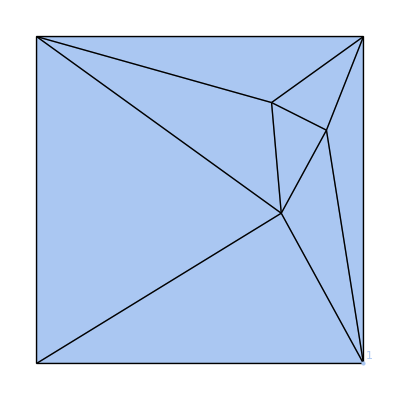

```mathematica
f=randomOrigami[3, MeshCellLabel->{Point[1]->"Index"}]
```

Select all the cells that are joined to vertex 1.

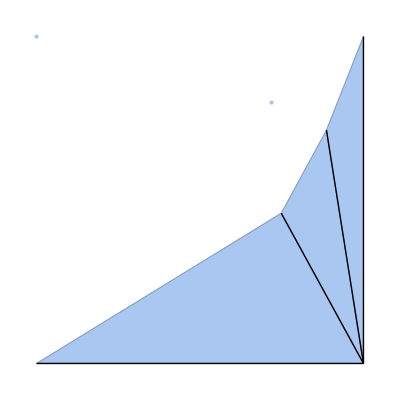

```mathematica
f2=selectCells[f, _[{___,1,___}]]
```

Keep all the rigid bars connected to vertex 1 but all the faces in the structure.

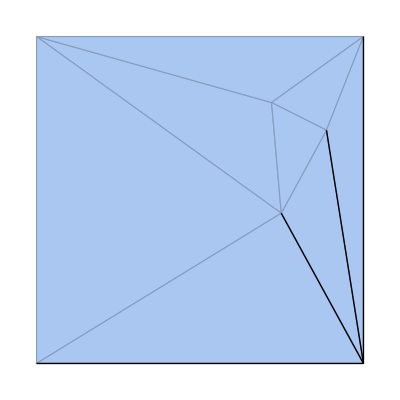

```mathematica
f2=selectCells[f,face[_]| rigidBar[{___,1,___}]]
```

Select cells with Automatic lengths.

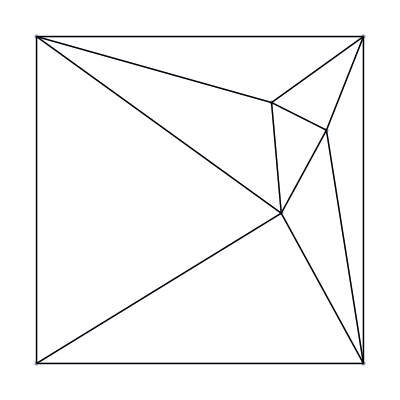

```mathematica
selectCells[ f, _[_], "length", #===Automatic& ]
```

#### changeCellData[]

```mathematica
?changeCellData
```

Make some random origami and extract the equilibrium lenths of all the edges.

```mathematica
cellData[
f=randomOrigami[3],
{rigidBar,"length"}
]
```

{{{4,6},{6,3},{3,4},{4,5},{5,6},{6,7},{7,3},{5,1},{1,7},{7,5},{4,1},{7,2},{2,3},{1,2}},{1.05534,0.505401,1.41421,1.03318,0.960424,0.660713,1.0503,0.544345,1.09546,0.671221,1.41421,0.611896,1.41421,1.41421}}

Set the equilibrium lengths with changeCellData[].

```mathematica
cellData[
f2=changeCellData[ f, rigidBar[_], {"length" -> 1/5} ],
{rigidBar, "length"}
]
```

{{{4,6},{6,3},{3,4},{4,5},{5,6},{6,7},{7,3},{5,1},{1,7},{7,5},{4,1},{7,2},{2,3},{1,2}},{1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5}}

Set the equilibrium lengths back to Automatic.

```mathematica
cellData[
changeCellData[ f2, rigidBar[_], {"length" -> Automatic} ],
{rigidBar, "length"}
]
```

{{{4,6},{6,3},{3,4},{4,5},{5,6},{6,7},{7,3},{5,1},{1,7},{7,5},{4,1},{7,2},{2,3},{1,2}},{1.05534,0.505401,1.41421,1.03318,0.960424,0.660713,1.0503,0.544345,1.09546,0.671221,1.41421,0.611896,1.41421,1.41421}}

#### highlightCells[]

```mathematica
?highlightCells
```

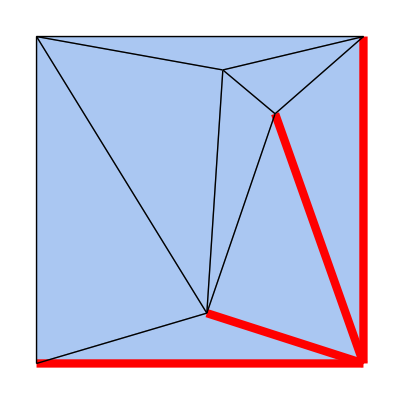

```mathematica
highlightCells[ f = randomOrigami[3], rigidBar[{1,_}], MeshCellStyle ->{Thickness[0.015], Red} ]
```

Go back to the default style.

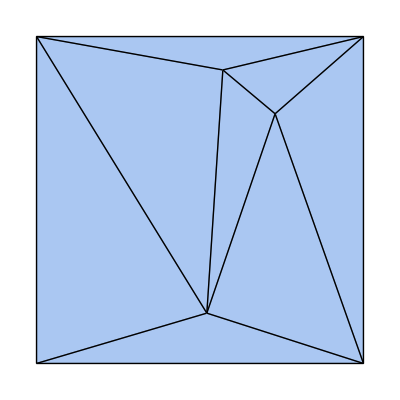

```mathematica
highlightCells[ f, rigidBar[_], MeshCellStyle -> {} ]
```

#### addCells[]

```mathematica
?addCells
```

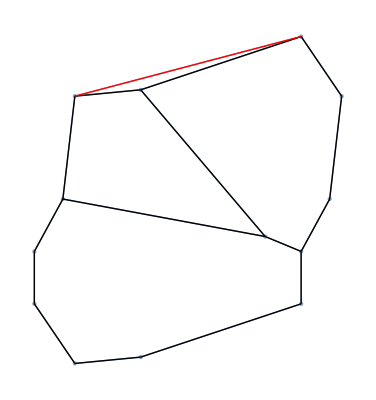

```mathematica
addCells[ randomCellNetwork[3], { Property[ rigidBar[{2,5}] , { MeshCellStyle -> Red } ]} ]
```

You can also write over existing cells to change their properties.

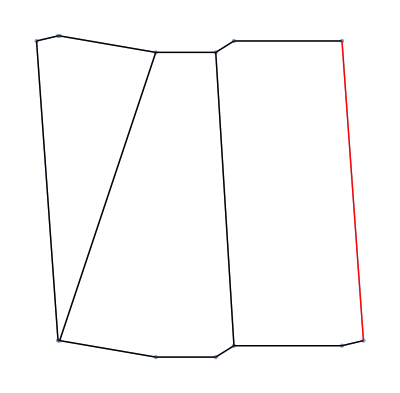

```mathematica
addCells[ randomCellNetwork[3], { Property[ rigidBar[{1,2}] , { MeshCellStyle -> Red } ]} ]
```

#### deleteCells[]

```mathematica
?deleteCells
```

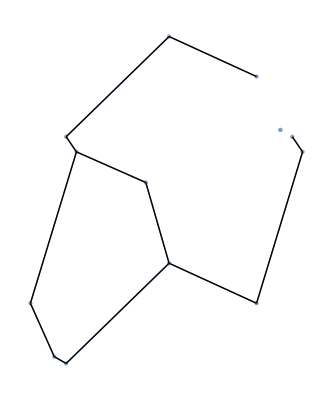

```mathematica
deleteCells[ randomCellNetwork[3], _[{1,_}]]
```

#### deleteVertices[]

```mathematica
?deleteVertices
```

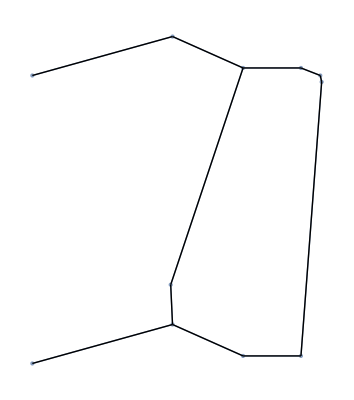
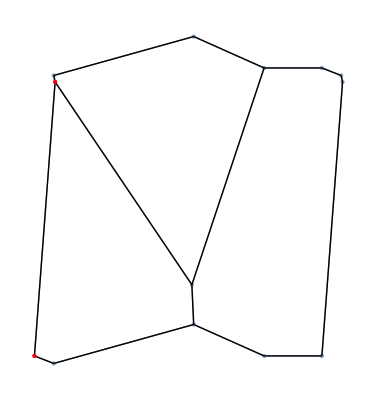

```mathematica
{
deleteVertices[ f=randomCellNetwork[3], {1,2}],
addCells[ f, Property[ Point[#],MeshCellStyle->Red]& /@ {1,2}]
}
```

#### displaceVertices[]

```mathematica
?displaceVertices
```

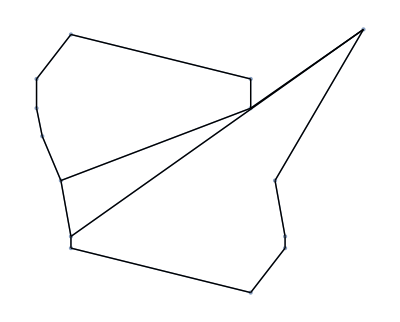
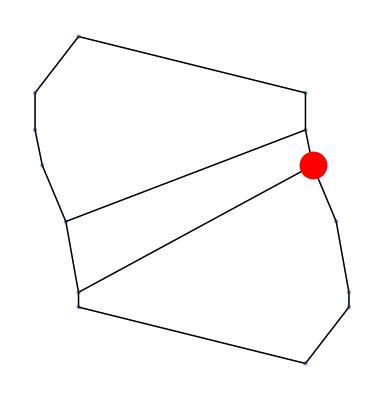

```mathematica
{
displaceVertices[ f=randomCellNetwork[3], {1->{0.5,0.5}} ],
addCells[ f, Property[ Point[1], MeshCellStyle -> {PointSize[0.05],Red} ] ]
}
```

```mathematica
displaceVertices[ randomOrigami[1], RandomReal[ {-0.1,0.1}, {5,3}]]
```

-Graphics3D-

#### splitEdge[]

```mathematica
?splitEdge
```

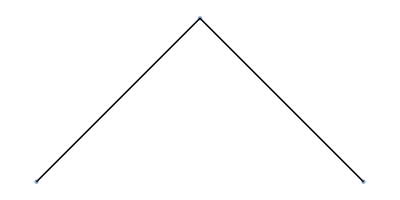

```mathematica
splitEdge[
framework[ {{0,0},{1,0}}, {rigidBar[{1,2}]}],
{1,2},
"a"->{1/2,1/2}
]
```

#### Henneberg[]

Henneberg operations acting on a 2D linkage preserve the number of degrees of freedom (generically).

```mathematica
?Henneberg
```

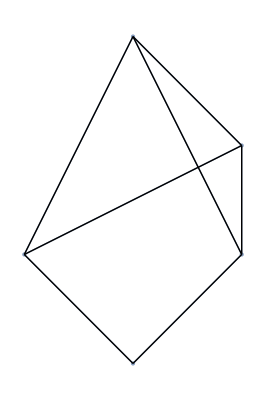

```mathematica
f2=Henneberg[2][ {1,2,"b"}, "a"->{1,1/2} ] @ Henneberg[1][ {1,2}, "c"->{1/2,-1/2} ] @ addCells[  { Point[ "b" -> {1/2,1}], rigidBar[{1,"b"}], rigidBar[{2,"b"}]} ] @ framework[{{0,0},{1,0}},{rigidBar[{1,2}]}]
```

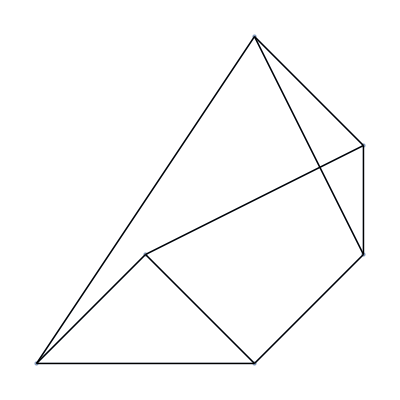

```mathematica
Henneberg[2][{-1/2,-1/2}] @ f2
```

#### joinMechanism[]

```mathematica
?joinMechanism
```

```mathematica
joinMechanism[ randomOrigami[2], #+{0,0,1}& /@ randomOrigami[3] ]
```

-Graphics3D-

Two vertices that are sufficiently close together will be merged. Use “overlapPrecision” to specify how close to operate this.

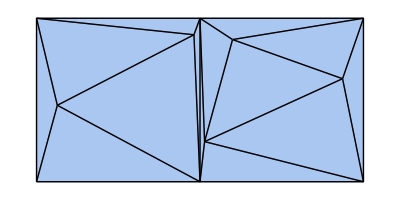

```mathematica
joinMechanism[ randomOrigami[2], #+{Sqrt[2],0,0}& /@ randomOrigami[3] ]
```

### topology

#### connectivity[], listFaces[], listEdges[], listVertices[]

```mathematica
?connectivity
```

```mathematica
connectivity["Methods"]
```

{{vertices,edges,faces}→{vertices,edges,faces,ordered faces,ordered edges}}

This function is used to work out what vertices, edges, and faces are connected to each other. It returns a list for each element of the left hand side of the rule and indicates all of the objects it is connected to on the right-hand side of the rule. To find all edges connected to each vertex, for example:

```mathematica
connectivity[ m=randomOrigami[3] , "vertices" -> "edges" ]
```

{{{1,2},{1,6},{1,4}},{{2,3},{2,6},{2,5},{2,1},{2,7}},{{3,4},{3,5},{3,2}},{{4,5},{4,7},{4,6},{4,1},{4,3}},{{5,3},{5,2},{5,4},{5,7}},{{6,1},{6,7},{6,2},{6,4}},{{7,5},{7,2},{7,4},{7,6}}}

If the object is oriented (see orientedQ[]) you can get the edges and faces in counterclockwise order.

```mathematica
connectivity[ m=randomOrigami[3] , "vertices" -> "ordered edges" ]
```

{{{1,2},{1,5},{1,7}},{{2,3},{2,6},{2,5}},{{3,4},{3,6}},{{4,1},{4,7},{4,6}},{{5,2},{5,6},{5,7},{5,1}},{{6,4},{6,7},{6,5},{6,2},{6,3}},{{7,1},{7,5},{7,6},{7,4}}}

We also have

```mathematica
listVertices[m]
```

{1,2,3,4,5,6,7}

```mathematica
listEdges[m]
```

{{4,6},{6,3},{3,4},{4,7},{7,6},{6,2},{2,3},{7,1},{1,5},{5,7},{4,1},{5,2},{6,5},{1,2}}

```mathematica
listFaces[m]
```

{{4,6,3},{6,4,7},{3,6,2},{7,1,5},{1,7,4},{5,2,6},{2,5,1},{7,5,6}}

## Examples

## basic examples

### basic principles to creating new frameworks and origami

The function framework is used to define a new framework in either 2 or 3 dimensions.

```mathematica
?framework
```

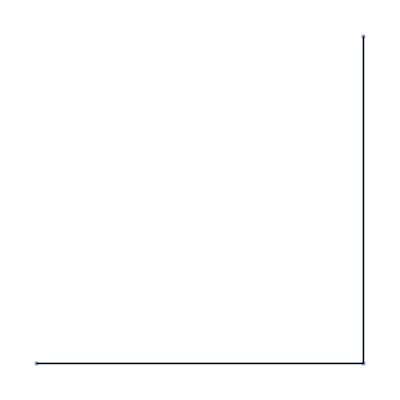

```mathematica
framework [ {{0,0},{1,0},{1,1}}, {rigidBar[{1,2}],rigidBar[{2,3}]} ]
```

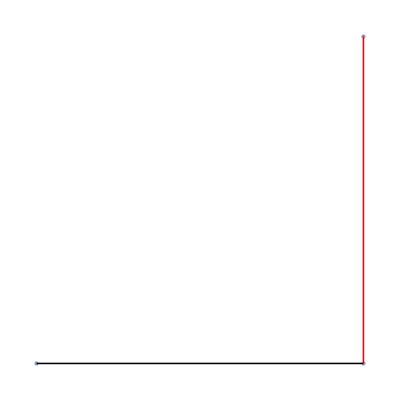

```mathematica
framework [ {{0,0},{1,0},{1,1}}, {rigidBar[{1,2}],Property[ rigidBar[{2,3}], MeshCellStyle->Red]} ]
```

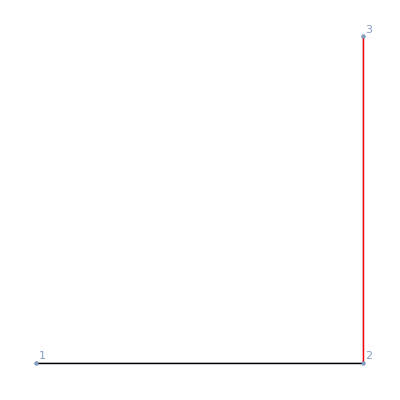

```mathematica
f=framework [ {{0,0},{1,0},{1,1}}, {rigidBar[{1,2}],Property[ rigidBar[{2,3}], MeshCellStyle->Red]}, MeshCellLabel->{0->"Index"} ]
```

```mathematica
f["Methods"]
```

{type,positions,mesh,components,labels,EmbeddingDimension,DisplayDimension,VertexNumber,edges,faces}

```mathematica
f["edges"]
```

{{1,2},{2,3}}

```mathematica
f["faces"]
```

{}

```mathematica
f["VertexNumber"]
```

3

```mathematica
RegionEmbeddingDimension[f]
```

2

```mathematica
RegionDimension[f]
```

1

```mathematica
f["DisplayDimension"]
```

2

### building new frameworks

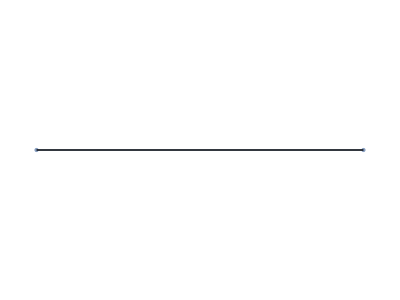

```mathematica
f=framework[{{0,0},{1,0}},{rigidBar[{1,2}]}]
```

There are two formats:

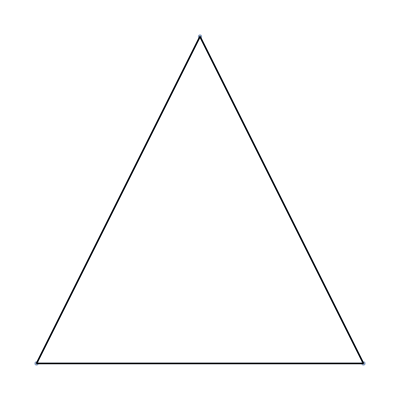

```mathematica
addCells[ f,  { Point[ "b" -> {1/2,1}], rigidBar[{1,"b"}], rigidBar[{2,"b"}]} ]
```

```mathematica
addCells[  { Point[ "b" -> {1/2,1}], rigidBar[{1,"b"}], rigidBar[{2,"b"}]} ] @ f
```

-Graphics-

This version allows constructions by sequential composition

#### Henneberg operations

```mathematica
?Henneberg
```

```mathematica
f2=Henneberg[2][ {1,2,"b"}, "a"->{1,1/2} ] @ Henneberg[1][ {1,2}, "c"->{1/2,-1/2} ] @ addCells[  { Point[ "b" -> {1/2,1}], rigidBar[{1,"b"}], rigidBar[{2,"b"}]} ] @ f
```

-Graphics-

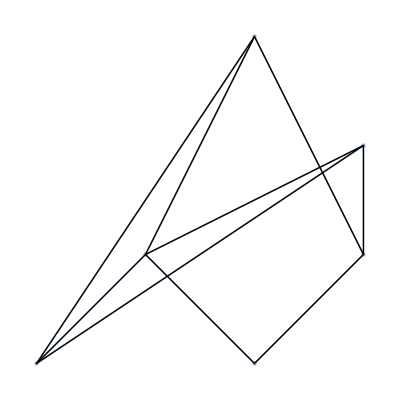

```mathematica
Henneberg[2][{-1/2,-1/2}] @ f2
```

### special mechanism examples

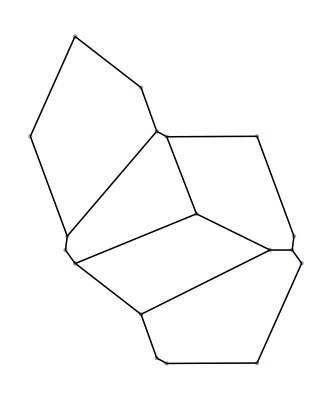

```mathematica
randomCellNetwork[5]
```

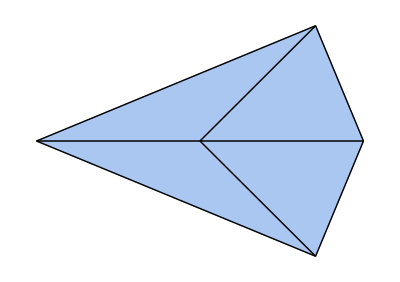

```mathematica
singleVertex[{Pi/4,3Pi/4,3Pi/4,Pi/4}]
```

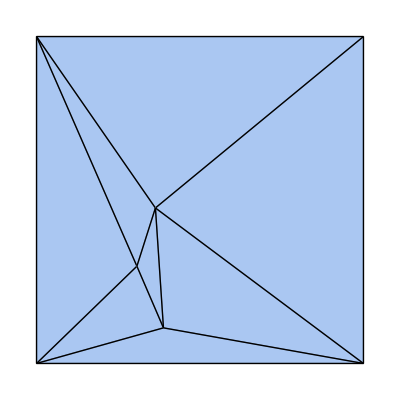

```mathematica
randomOrigami[3]
```

## mechanism examples

### Watt mechanism

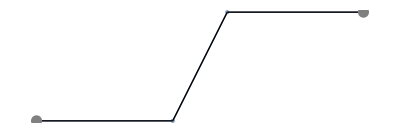

```mathematica
wattMechanism = framework[ {{0,0},{1+1/4,0},{2-1/4,1},{3,1}}, {rigidBar/@ {{1,2},{2,3},{3,4}}, joint[1],joint[4]} ]
```

```mathematica
im=infinitesimalMotions[ wattMechanism , "variables" -> v ]
```

{{{0,0},{0,v[1]/(√2)},{0,v[1]/(√2)},{0,0}},{}}

```mathematica
direction = D[im[[1]],v[1]]
```

{{0,0},{0,1/(√2)},{0,1/(√2)},{0,0}}

```mathematica
zeroModes[wattMechanism]
```

{{{0,0},{0,1},{0,1},{0,0}}}

```mathematica
trajectory = isometricTrajectory[ wattMechanism, direction, 100 ];
```

```mathematica
(*The center of the middle bar position *)
centerTrace = Mean /@ trajectory[[All, {2,3}]] ;
centerTrail = Table[ centerTrace[[1;;i]], {i,1,Length[centerTrace]}];
```

```mathematica
ListAnimate @ 
MapThread[
Show[#1,Graphics[{Blue,Point[#2]}]]&,
{
plotMechanism[ wattMechanism, trajectory ],
centerTrail
}
]
```

### origami bird’s foot vertex

```mathematica
o=addCells[ { Property[ fold[{1,2}] ,  "angle"-> Pi/2 ] } ] @ singleVertex[{Pi/4,3Pi/4,3Pi/4,Pi/4}]
```

-Graphics-

```mathematica
{en, pos } = minimizeEnergy[o]
```

{1.37547×10^-20,{{-0.0729825,0.00580439,-0.141497},{0.731324,0.588966,-0.255571},{-0.84149,-0.0217513,0.497751},{0.731972,-0.564696,-0.304523},{0.86539,-0.00832258,0.203841}}}

```mathematica
plotMechanism[o,pos]
```

-Graphics3D-

```mathematica
{ linear, quadratic} = FullSimplify[
infinitesimalMotions[o = singleVertex[{Pi/4,3Pi/4,3Pi/4,Pi/4}], "constraints" ->{vertexDisplacement[1,All[3]], vertexDisplacement[2,"z"], vertexDisplacement[3,{"y","z"}]} ,
"variables" -> v]
]
```

{{{0,0,0},{0,0,0},{0,0,0},{0,0,v[2]},{0,0,v[1]}},{(v[1] (v[1]-√2 v[2]))/(2 √3)}}

```mathematica
dir = D[ linear /. Solve[quadratic==0,{v[1],v[2]}] /. {v[1]->v,v[2]->v},v]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{{0,0,0},{0,0,0},{0,0,0},{0,0,1},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,1/(√2)},{0,0,1}}}

```mathematica
trajectory1 = Join[
Reverse @isometricTrajectory[ o, -dir[[1]],180,"constraints" -> {vertexDisplacement[1,All[3]], vertexDisplacement[2,"z"], vertexDisplacement[3,{"y","z"}]}, "stepsize" -> 0.02][[All,{4,5},3]]

,
 isometricTrajectory[ o, dir[[1]],180,"constraints" -> {vertexDisplacement[1,All[3]], vertexDisplacement[2,"z"], vertexDisplacement[3,{"y","z"}]}, "stepsize" -> 0.02][[All,{4,5},3]]
];

trajectory2 = Join[
Reverse @isometricTrajectory[ o, -dir[[2]],180,"constraints" -> {vertexDisplacement[1,All[3]], vertexDisplacement[2,"z"], vertexDisplacement[3,{"y","z"}]}, "stepsize" -> 0.02][[All,{4,5},3]]

,
 isometricTrajectory[ o, dir[[2]],180,"constraints" -> {vertexDisplacement[1,All[3]], vertexDisplacement[2,"z"], vertexDisplacement[3,{"y","z"}]}, "stepsize" -> 0.02][[All,{4,5},3]]
];
```

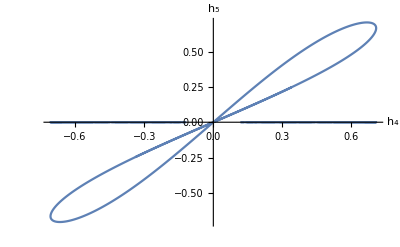

```mathematica
Show[
ListPlot[trajectory1,Joined->True],
ListPlot[trajectory2, Joined->True],

PlotRange->All,AxesLabel->{Subscript["h",4],Subscript["h",5]}
]
```

## graphics

### plotOrigami[]

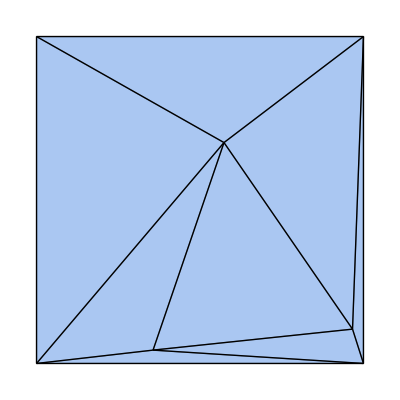

```mathematica
o=randomOrigami[3]
```

```mathematica
addCells[o,{ Point[ 1 -> ( vertexPosition[1,All[3]] +{0,0,0.1}) ] } ]
```

-Graphics3D-

```mathematica
{en , pos } = minimizeEnergy[ addCells[o, Property[ fold[First @ interiorEdges[o]], "angle" -> Pi/2 ] ], MaxIterations -> 10^5 ]
```

{2.50134×10^-23,{{0.533763,-0.596093,0.332497},{0.752749,0.694613,-0.202409},{-0.469993,0.411867,0.449479},{-0.66074,-0.687843,-0.418998},{0.122995,0.276538,-0.256254},{0.511835,-0.459106,0.261543},{-0.23005,-0.599532,-0.165857}}}

```mathematica
plotMechanism[o,pos]
```

-Graphics3D-

```mathematica
plotOrigami[ displayDimension[3]@o, pos ]
```

-Graphics3D-

## periodic mechanisms

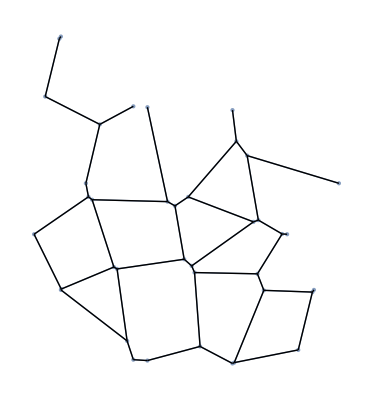

```mathematica
m=minimalMechanism[ m0=randomCellNetwork[15], {{1,0},{0,1}}]
```

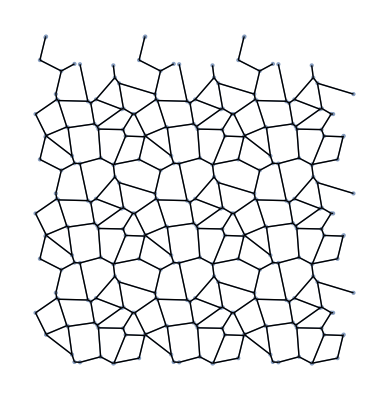

```mathematica
tesselateMechanism[ m , {{1,0},{0,1}},{3,3}]
```

```mathematica
pi=periodicIdentification[ m, {1,1}, {{1,0},{0,1}} ]
```

{vertexDisplacement[21,x]→vertexDisplacement[34,x],vertexDisplacement[21,y]→vertexDisplacement[34,y],vertexDisplacement[23,x]→vertexDisplacement[20,x],vertexDisplacement[23,y]→vertexDisplacement[20,y],vertexDisplacement[29,x]→vertexDisplacement[38,x],vertexDisplacement[29,y]→vertexDisplacement[38,y],vertexDisplacement[30,x]→vertexDisplacement[9,x],vertexDisplacement[30,y]→vertexDisplacement[9,y],vertexDisplacement[35,x]→vertexDisplacement[39,x],vertexDisplacement[35,y]→vertexDisplacement[39,y],vertexDisplacement[36,x]→vertexDisplacement[28,x],vertexDisplacement[36,y]→vertexDisplacement[28,y],vertexDisplacement[37,x]→vertexDisplacement[9,x],vertexDisplacement[37,y]→vertexDisplacement[9,y]}

```mathematica
constraintMatrix[m, "rules" -> pi ]
```

SparseArray[…]

```mathematica
m2=changeCellData[m, spring[_], {"length" -> 0.05}]
```

-Graphics-

```mathematica
{en, pos} = minimizeEnergy[m2, "constraints" -> Equal@@@pi]
```

{0.257285,{{0.392525,-0.526443},{0.470426,-0.473244},{0.361301,-0.472923},{0.314624,-0.579642},{-0.256703,-0.466353},{-0.177566,-0.303476},{-0.265834,-0.216486},{-0.371645,-0.285457},{-0.385439,-0.435864},{0.147138,-0.0267976},{0.192764,-0.138053},{0.320759,-0.111507},{0.375333,0.0238249},{0.246054,0.102429},{-0.0247567,-0.211729},{0.11332,-0.261485},{0.00354218,-0.0638033},{-0.248587,-0.0732832},{-0.389049,-0.0620757},{-0.46035,-0.189857},{0.545699,0.0743816},{0.389481,-0.227048},{0.53965,-0.189857},{0.168007,-0.423039},{0.30534,-0.367694},{-0.108551,0.0453705},{0.0993267,-0.621128},{0.221728,-0.705817},{-0.225692,0.347457},{-0.385439,0.564136},{-0.373394,0.45763},{-0.36135,0.351125},{-0.349305,0.24462},{-0.454301,0.0743816},{-0.0750621,0.255366},{0.221728,0.294183},{0.614561,-0.435864},{-0.225692,-0.652543},{-0.0750621,-0.744634}}}

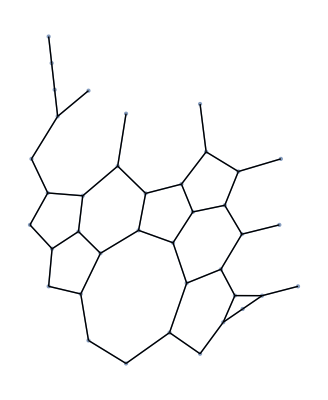

```mathematica
plotMechanism[ m, pos ]
```

```mathematica
cm=constraintMatrix[ m, "rules" -> periodicIdentification[ m, {zx,zy}, {{1,0},{0,1}} ] ]
```

SparseArray[…]